# New Fitting using an Attenuated Sine Wave

```mathematica
ClearAll["Global`*"]
```

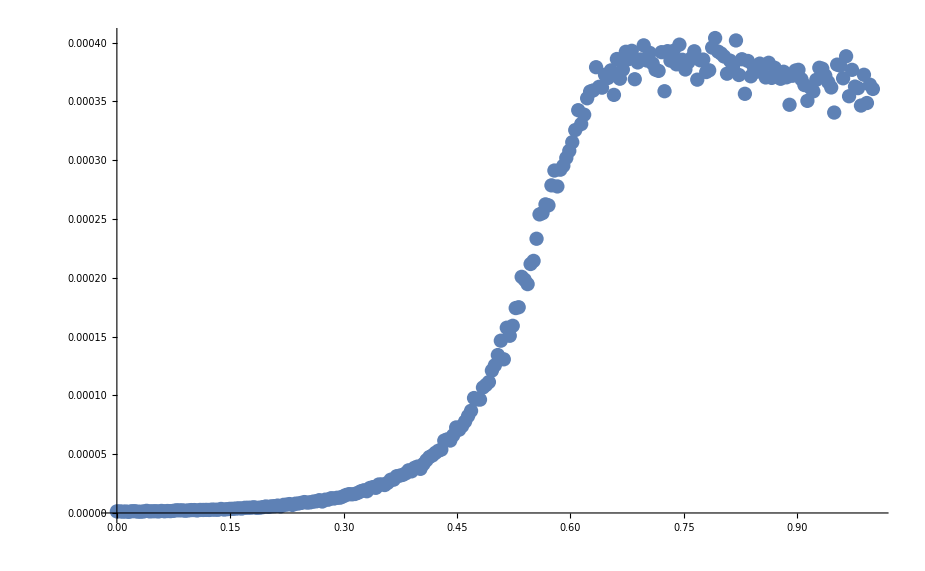

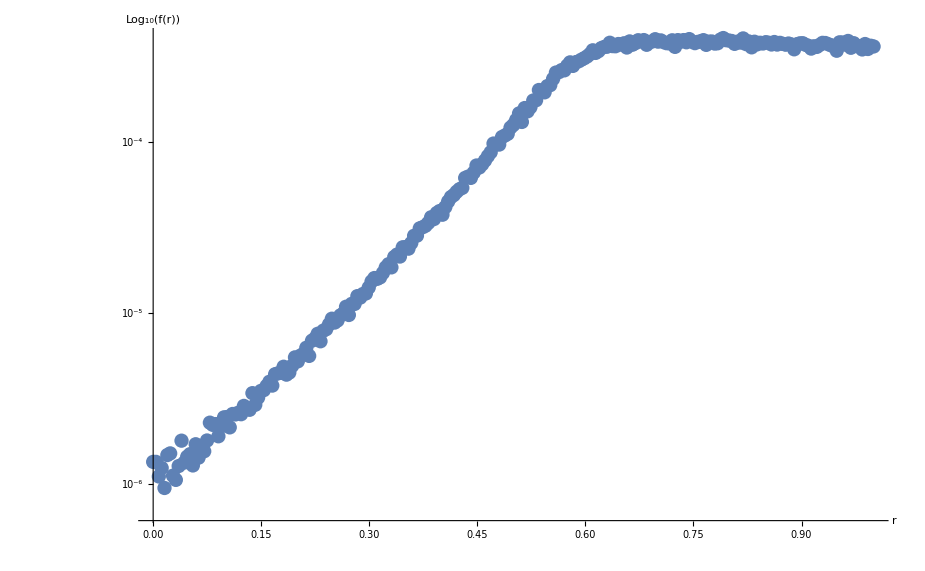

```mathematica
(* Import binary data as a 100x100 entry float3 array *)
SetDirectory[NotebookDirectory[]]; 
tableSize = 255;
rawArray= BinaryReadList["BlueNoiseRadialProfile255.complex", {"Real64","Real64"}];

radialProfileTable = Table[{i/(tableSize-1),rawArray[[Max[1,i]]][[1]]},{i,0,tableSize-1}];
logRadialProfileTable = Table[{i/(tableSize-1),Log10[rawArray[[Max[1,i]]][[1]]]},{i,0,tableSize-1}];

ListPlot[radialProfileTable]
ListPlot[logRadialProfileTable,AxesLabel->{"r","Log_10(f(r))"}];
ListLogPlot[radialProfileTable,AxesLabel->{"r","Log_10(f(r))"}]
```

## Attenuated Sine/Sigmoïd

```mathematica
cutProfile=Table[radialProfileTable[[i]],{i,140,tableSize-1}];
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→0.000391938,b→0.639495,c→8.01936,d→3.8855,e→-20.7106,f→0.0791527,g→-0.200022,h→-0.282977,i→0.165679,j→2.39823}

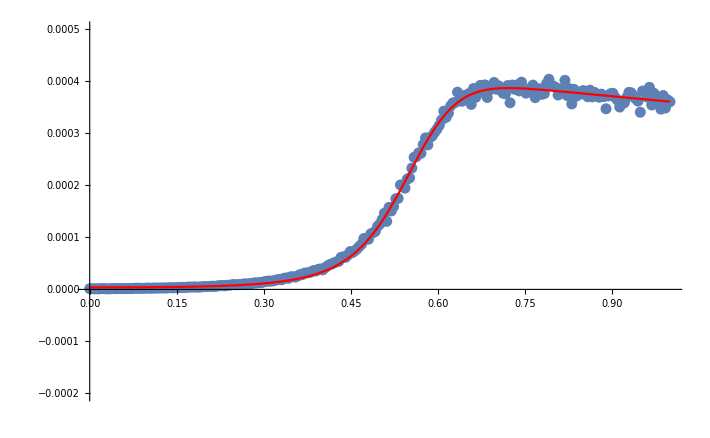

```mathematica
fittingMethod="Automatic";
model=Sin[c+d*x]/(e+f*x);
model= Exp[a+b*x]*Sin[c+d*x]/(e+f*x);
model=(a*Exp[g+h*(x+i)])/(b+c*Exp[d+e*(x^j+f)]);  (* Some sort of feng-shui sigmoïd... *)
modelFit=FindFit[cutProfile,model,{{a,0.0005},{b,1},{c,1 },{d,0},{e,-1},{f,3},{g,0},{h,-1},{i,0},{j,3}},{x},Method->fittingMethod]

model=Function[{x},Evaluate[model/.modelFit]];

Show[ 
ListPlot[radialProfileTable,PlotRange->{-0.0002,0.0005}],
 Plot[model[x],{x,0,1},PlotStyle->Red]
]
```

## Remapping Noise Distribution

1000

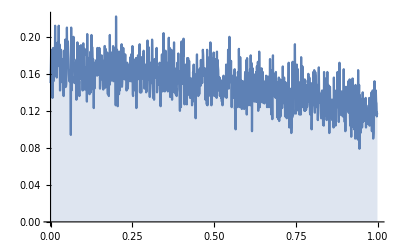

```mathematica
rawHistogramArray= BinaryReadList["noiseDistribution.float", "Real32"];
Length[rawHistogramArray]
distribTable = Table[{(i-1)/1000,rawHistogramArray[[i]]},{i,1,999}];
ListPlot[distribTable,Joined->True,Filling->Axis]
```

{a→0.168542,b→-0.0127432,c→-0.0384239,d→0.}

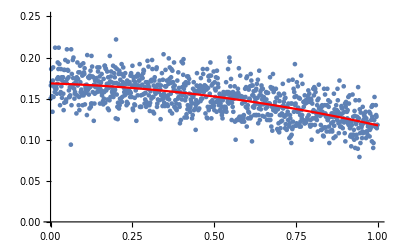

```mathematica
model=a+b*x+c*x^2;
modelFit=FindFit[distribTable,model,{{a,0},{b,1},{c,1 },{d,0}},{x},Method->fittingMethod]
model=Function[{x},Evaluate[model/.modelFit]];

Show[ 
ListPlot[distribTable,PlotRange->{0,0.25}],
 Plot[model[x],{x,0,1},PlotStyle->Red]
]
```

149.506

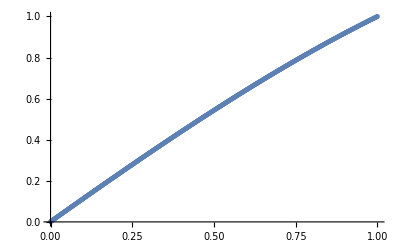

```mathematica
totalSum=Sum[model[i],{i,0,1,0.001}] 
partialSum=Table[{j,1/totalSum Sum[model[i],{i,0,j,0.001}]},{j,0,1,0.001}];
(*totalSum=Integrate[model[x],{x,0,1}] 
partialSum=Table[{j,1/totalSum Integrate[model[x],{x,0,j}]},{j,0,1,0.001}];*)
ListPlot[partialSum]
```

{a→0.,b→1.13574,c→-0.0596391,d→-0.0758194,e→0.}

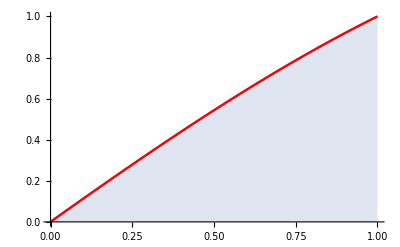

```mathematica
model=0*a+b*x+c*x^2+d*x^3+0*e*x^4;
modelFit=FindFit[partialSum,model,{{a,0.0},{b,1},{c,1 },{d,0},{e,0}},{x},Method->fittingMethod]
model=Function[{x},Evaluate[model/.modelFit]];

Show[ 
ListPlot[partialSum,PlotRange->{0,1}, Joined->True,Filling->Axis],
 Plot[model[x],{x,0,1},PlotStyle->Red]
]
```

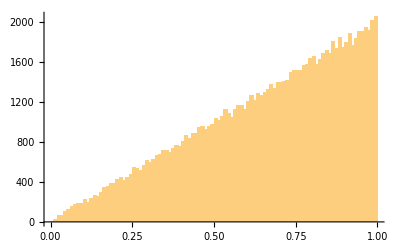

```mathematica
Histogram[Table[Sqrt[RandomReal[]],{i,0,100000}],100]
```

```mathematica
histo=HistogramDistribution[Table[Sqrt[RandomReal[]],{i,0,100000}],100];
DiscretePlot[PDF[histo[i]],{i,0,100}]
```

-Graphics-

## Something else entirely...

```mathematica
rawCDFArray= BinaryReadList["dickCDF.float", "Real32"];
Length[rawCDFArray];
CDFTable = Table[{(i-1)/256,rawCDFArray[[i]]},{i,1,256}];
ListPlot[CDFTable,Joined->True,Filling->Axis]
```

BinaryReadList::nffil: File not found during BinaryReadList["dickCDF.float", "Real32"].

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification $Failed ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification $Failed ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

-Graphics-

```mathematica
histoDistrib = HistogramDistribution[rawCDFArray,256];
DiscretePlot[InverseCDF[histoDistrib,x],{x,0,1,0.01},Filling->Axis];
DiscretePlot[CDF[histoDistrib,x],{x,0,1,0.01},Filling->Axis,Joined->True];
CDFTable = Table[{(i-1)/256,CDF[histoDistrib,i/256]},{i,1,256}];
ListPlot[CDFTable,Filling->Axis,Joined->True]
```

-Graphics-

```mathematica
CDFPart0=Table[CDFTable[[i]],{i,2,59}];
ListPlot[CDFPart0,Joined->True,Filling->Axis];
model=a+b*x+c*x^2+d*x^3+e*x^4;
model=a+b*x+c*x^2+d*x^3+0*e*x^4;
modelFit=FindFit[CDFPart0,model,{{a,0.0},{b,1},{c,1 },{d,0},{e,0}},{x},Method->fittingMethod]
modelBalls=Function[{x},Evaluate[model/.modelFit]];

Show[ 
ListPlot[CDFPart0,PlotRange->{0,1}, Joined->True,Filling->Axis],
 Plot[modelBalls[x],{x,0,1},PlotStyle->Red]
]
```

{a→0.131306 (2.1009 CDF[HistogramDistribution[$Failed,256],1/128]+1.82447 CDF[HistogramDistribution[$Failed,256],3/256]+1.56778 CDF[HistogramDistribution[$Failed,256],1/64]+1.33021 CDF[HistogramDistribution[$Failed,256],5/256]+1.11112 CDF[HistogramDistribution[$Failed,256],3/128]+0.909901 CDF[HistogramDistribution[$Failed,256],7/256]+0.72591 CDF[HistogramDistribution[$Failed,256],1/32]+0.558524 CDF[HistogramDistribution[$Failed,256],9/256]+0.407113 CDF[HistogramDistribution[$Failed,256],5/128]+0.27105 CDF[HistogramDistribution[$Failed,256],11/256]+0.149705 CDF[HistogramDistribution[$Failed,256],3/64]+0.0424525 CDF[HistogramDistribution[$Failed,256],13/256]-0.0513379 CDF[HistogramDistribution[$Failed,256],7/128]-0.132294 CDF[HistogramDistribution[$Failed,256],15/256]-0.201043 CDF[HistogramDistribution[$Failed,256],1/16]-0.258215 CDF[HistogramDistribution[$Failed,256],17/256]-0.304437 CDF[HistogramDistribution[$Failed,256],9/128]-0.340338 CDF[HistogramDistribution[$Failed,256],19/256]-0.366545 CDF[HistogramDistribution[$Failed,256],5/64]-0.383688 CDF[HistogramDistribution[$Failed,256],21/256]-0.392394 CDF[HistogramDistribution[$Failed,256],11/128]-0.393291 CDF[HistogramDistribution[$Failed,256],23/256]-0.387008 CDF[HistogramDistribution[$Failed,256],3/32]-0.374174 CDF[HistogramDistribution[$Failed,256],25/256]-0.355416 CDF[HistogramDistribution[$Failed,256],13/128]-0.331363 CDF[HistogramDistribution[$Failed,256],27/256]-0.302642 CDF[HistogramDistribution[$Failed,256],7/64]-0.269883 CDF[HistogramDistribution[$Failed,256],29/256]-0.233713 CDF[HistogramDistribution[$Failed,256],15/128]-0.194761 CDF[HistogramDistribution[$Failed,256],31/256]-0.153655 CDF[HistogramDistribution[$Failed,256],1/8]-0.111023 CDF[HistogramDistribution[$Failed,256],33/256]-0.0674931 CDF[HistogramDistribution[$Failed,256],17/128]-0.0236944 CDF[HistogramDistribution[$Failed,256],35/256]+0.0197453 CDF[HistogramDistribution[$Failed,256],9/64]+0.0621978 CDF[HistogramDistribution[$Failed,256],37/256]+0.103035 CDF[HistogramDistribution[$Failed,256],19/128]+0.141628 CDF[HistogramDistribution[$Failed,256],39/256]+0.177349 CDF[HistogramDistribution[$Failed,256],5/32]+0.20957 CDF[HistogramDistribution[$Failed,256],41/256]+0.237662 CDF[HistogramDistribution[$Failed,256],21/128]+0.260997 CDF[HistogramDistribution[$Failed,256],43/256]+0.278948 CDF[HistogramDistribution[$Failed,256],11/64]+0.290885 CDF[HistogramDistribution[$Failed,256],45/256]+0.29618 CDF[HistogramDistribution[$Failed,256],23/128]+0.294205 CDF[HistogramDistribution[$Failed,256],47/256]+0.284333 CDF[HistogramDistribution[$Failed,256],3/16]+0.265934 CDF[HistogramDistribution[$Failed,256],49/256]+0.23838 CDF[HistogramDistribution[$Failed,256],25/128]+0.201043 CDF[HistogramDistribution[$Failed,256],51/256]+0.153296 CDF[HistogramDistribution[$Failed,256],13/64]+0.0945083 CDF[HistogramDistribution[$Failed,256],53/256]+0.0240534 CDF[HistogramDistribution[$Failed,256],27/128]-0.0586975 CDF[HistogramDistribution[$Failed,256],55/256]-0.154373 CDF[HistogramDistribution[$Failed,256],7/32]-0.2636 CDF[HistogramDistribution[$Failed,256],57/256]-0.387008 CDF[HistogramDistribution[$Failed,256],29/128]-0.525226 CDF[HistogramDistribution[$Failed,256],59/256]),b→0.991021 (-8.76237 CDF[HistogramDistribution[$Failed,256],1/128]-7.23153 CDF[HistogramDistribution[$Failed,256],3/256]-5.8234 CDF[HistogramDistribution[$Failed,256],1/64]-4.53381 CDF[HistogramDistribution[$Failed,256],5/256]-3.35862 CDF[HistogramDistribution[$Failed,256],3/128]-2.29365 CDF[HistogramDistribution[$Failed,256],7/256]-1.33477 CDF[HistogramDistribution[$Failed,256],1/32]-0.477797 CDF[HistogramDistribution[$Failed,256],9/256]+0.281413 CDF[HistogramDistribution[$Failed,256],5/128]+0.947021 CDF[HistogramDistribution[$Failed,256],11/256]+1.52318 CDF[HistogramDistribution[$Failed,256],3/64]+2.01406 CDF[HistogramDistribution[$Failed,256],13/256]+2.42381 CDF[HistogramDistribution[$Failed,256],7/128]+2.75658 CDF[HistogramDistribution[$Failed,256],15/256]+3.01654 CDF[HistogramDistribution[$Failed,256],1/16]+3.20784 CDF[HistogramDistribution[$Failed,256],17/256]+3.33465 CDF[HistogramDistribution[$Failed,256],9/128]+3.40111 CDF[HistogramDistribution[$Failed,256],19/256]+3.41139 CDF[HistogramDistribution[$Failed,256],5/64]+3.36964 CDF[HistogramDistribution[$Failed,256],21/256]+3.28002 CDF[HistogramDistribution[$Failed,256],11/128]+3.1467 CDF[HistogramDistribution[$Failed,256],23/256]+2.97381 CDF[HistogramDistribution[$Failed,256],3/32]+2.76554 CDF[HistogramDistribution[$Failed,256],25/256]+2.52602 CDF[HistogramDistribution[$Failed,256],13/128]+2.25942 CDF[HistogramDistribution[$Failed,256],27/256]+1.9699 CDF[HistogramDistribution[$Failed,256],7/64]+1.66162 CDF[HistogramDistribution[$Failed,256],29/256]+1.33872 CDF[HistogramDistribution[$Failed,256],15/128]+1.00538 CDF[HistogramDistribution[$Failed,256],31/256]+0.665738 CDF[HistogramDistribution[$Failed,256],1/8]+0.323965 CDF[HistogramDistribution[$Failed,256],33/256]-0.0157867 CDF[HistogramDistribution[$Failed,256],17/128]-0.349358 CDF[HistogramDistribution[$Failed,256],35/256]-0.672593 CDF[HistogramDistribution[$Failed,256],9/64]-0.981332 CDF[HistogramDistribution[$Failed,256],37/256]-1.27142 CDF[HistogramDistribution[$Failed,256],19/128]-1.5387 CDF[HistogramDistribution[$Failed,256],39/256]-1.779 CDF[HistogramDistribution[$Failed,256],5/32]-1.98819 CDF[HistogramDistribution[$Failed,256],41/256]-2.16209 CDF[HistogramDistribution[$Failed,256],21/128]-2.29655 CDF[HistogramDistribution[$Failed,256],43/256]-2.38741 CDF[HistogramDistribution[$Failed,256],11/64]-2.43052 CDF[HistogramDistribution[$Failed,256],45/256]-2.42171 CDF[HistogramDistribution[$Failed,256],23/128]-2.35683 CDF[HistogramDistribution[$Failed,256],47/256]-2.23173 CDF[HistogramDistribution[$Failed,256],3/16]-2.04223 CDF[HistogramDistribution[$Failed,256],49/256]-1.7842 CDF[HistogramDistribution[$Failed,256],25/128]-1.45346 CDF[HistogramDistribution[$Failed,256],51/256]-1.04587 CDF[HistogramDistribution[$Failed,256],13/64]-0.557255 CDF[HistogramDistribution[$Failed,256],53/256]+0.0165311 CDF[HistogramDistribution[$Failed,256],27/128]+0.679648 CDF[HistogramDistribution[$Failed,256],55/256]+1.43625 CDF[HistogramDistribution[$Failed,256],7/32]+2.29051 CDF[HistogramDistribution[$Failed,256],57/256]+3.24657 CDF[HistogramDistribution[$Failed,256],29/128]+4.30858 CDF[HistogramDistribution[$Failed,256],59/256]),c→5.59923 (13.2889 CDF[HistogramDistribution[$Failed,256],1/128]+10.6713 CDF[HistogramDistribution[$Failed,256],3/256]+8.27771 CDF[HistogramDistribution[$Failed,256],1/64]+6.10029 CDF[HistogramDistribution[$Failed,256],5/256]+4.13112 CDF[HistogramDistribution[$Failed,256],3/128]+2.36228 CDF[HistogramDistribution[$Failed,256],7/256]+0.785863 CDF[HistogramDistribution[$Failed,256],1/32]-0.606055 CDF[HistogramDistribution[$Failed,256],9/256]-1.82138 CDF[HistogramDistribution[$Failed,256],5/128]-2.86804 CDF[HistogramDistribution[$Failed,256],11/256]-3.75393 CDF[HistogramDistribution[$Failed,256],3/64]-4.48698 CDF[HistogramDistribution[$Failed,256],13/256]-5.0751 CDF[HistogramDistribution[$Failed,256],7/128]-5.5262 CDF[HistogramDistribution[$Failed,256],15/256]-5.8482 CDF[HistogramDistribution[$Failed,256],1/16]-6.04901 CDF[HistogramDistribution[$Failed,256],17/256]-6.13655 CDF[HistogramDistribution[$Failed,256],9/128]-6.11873 CDF[HistogramDistribution[$Failed,256],19/256]-6.00346 CDF[HistogramDistribution[$Failed,256],5/64]-5.79866 CDF[HistogramDistribution[$Failed,256],21/256]-5.51225 CDF[HistogramDistribution[$Failed,256],11/128]-5.15214 CDF[HistogramDistribution[$Failed,256],23/256]-4.72623 CDF[HistogramDistribution[$Failed,256],3/32]-4.24246 CDF[HistogramDistribution[$Failed,256],25/256]-3.70873 CDF[HistogramDistribution[$Failed,256],13/128]-3.13295 CDF[HistogramDistribution[$Failed,256],27/256]-2.52304 CDF[HistogramDistribution[$Failed,256],7/64]-1.88692 CDF[HistogramDistribution[$Failed,256],29/256]-1.2325 CDF[HistogramDistribution[$Failed,256],15/128]-0.56769 CDF[HistogramDistribution[$Failed,256],31/256]+0.0995911 CDF[HistogramDistribution[$Failed,256],1/8]+0.76143 CDF[HistogramDistribution[$Failed,256],33/256]+1.40991 CDF[HistogramDistribution[$Failed,256],17/128]+2.03712 CDF[HistogramDistribution[$Failed,256],35/256]+2.63515 CDF[HistogramDistribution[$Failed,256],9/64]+3.19607 CDF[HistogramDistribution[$Failed,256],37/256]+3.71198 CDF[HistogramDistribution[$Failed,256],19/128]+4.17497 CDF[HistogramDistribution[$Failed,256],39/256]+4.57711 CDF[HistogramDistribution[$Failed,256],5/32]+4.91049 CDF[HistogramDistribution[$Failed,256],41/256]+5.1672 CDF[HistogramDistribution[$Failed,256],21/128]+5.33932 CDF[HistogramDistribution[$Failed,256],43/256]+5.41895 CDF[HistogramDistribution[$Failed,256],11/64]+5.39815 CDF[HistogramDistribution[$Failed,256],45/256]+5.26903 CDF[HistogramDistribution[$Failed,256],23/128]+5.02367 CDF[HistogramDistribution[$Failed,256],47/256]+4.65414 CDF[HistogramDistribution[$Failed,256],3/16]+4.15255 CDF[HistogramDistribution[$Failed,256],49/256]+3.51096 CDF[HistogramDistribution[$Failed,256],25/128]+2.72148 CDF[HistogramDistribution[$Failed,256],51/256]+1.77618 CDF[HistogramDistribution[$Failed,256],13/64]+0.667147 CDF[HistogramDistribution[$Failed,256],53/256]-0.613528 CDF[HistogramDistribution[$Failed,256],27/128]-2.07376 CDF[HistogramDistribution[$Failed,256],55/256]-3.72147 CDF[HistogramDistribution[$Failed,256],7/32]-5.56457 CDF[HistogramDistribution[$Failed,256],57/256]-7.61096 CDF[HistogramDistribution[$Failed,256],29/128]-9.86858 CDF[HistogramDistribution[$Failed,256],59/256]),d→28.9958 (-6.46774 CDF[HistogramDistribution[$Failed,256],1/128]-5.10611 CDF[HistogramDistribution[$Failed,256],3/256]-3.86605 CDF[HistogramDistribution[$Failed,256],1/64]-2.74315 CDF[HistogramDistribution[$Failed,256],5/256]-1.73298 CDF[HistogramDistribution[$Failed,256],3/128]-0.831124 CDF[HistogramDistribution[$Failed,256],7/256]-0.0331566 CDF[HistogramDistribution[$Failed,256],1/32]+0.665341 CDF[HistogramDistribution[$Failed,256],9/256]+1.26879 CDF[HistogramDistribution[$Failed,256],5/128]+1.78161 CDF[HistogramDistribution[$Failed,256],11/256]+2.20823 CDF[HistogramDistribution[$Failed,256],3/64]+2.55305 CDF[HistogramDistribution[$Failed,256],13/256]+2.82052 CDF[HistogramDistribution[$Failed,256],7/128]+3.01504 CDF[HistogramDistribution[$Failed,256],15/256]+3.14103 CDF[HistogramDistribution[$Failed,256],1/16]+3.20292 CDF[HistogramDistribution[$Failed,256],17/256]+3.20513 CDF[HistogramDistribution[$Failed,256],9/128]+3.15208 CDF[HistogramDistribution[$Failed,256],19/256]+3.04819 CDF[HistogramDistribution[$Failed,256],5/64]+2.89788 CDF[HistogramDistribution[$Failed,256],21/256]+2.70557 CDF[HistogramDistribution[$Failed,256],11/128]+2.47569 CDF[HistogramDistribution[$Failed,256],23/256]+2.21265 CDF[HistogramDistribution[$Failed,256],3/32]+1.92087 CDF[HistogramDistribution[$Failed,256],25/256]+1.60478 CDF[HistogramDistribution[$Failed,256],13/128]+1.26879 CDF[HistogramDistribution[$Failed,256],27/256]+0.917331 CDF[HistogramDistribution[$Failed,256],7/64]+0.55482 CDF[HistogramDistribution[$Failed,256],29/256]+0.185677 CDF[HistogramDistribution[$Failed,256],15/128]-0.185677 CDF[HistogramDistribution[$Failed,256],31/256]-0.55482 CDF[HistogramDistribution[$Failed,256],1/8]-0.917331 CDF[HistogramDistribution[$Failed,256],33/256]-1.26879 CDF[HistogramDistribution[$Failed,256],17/128]-1.60478 CDF[HistogramDistribution[$Failed,256],35/256]-1.92087 CDF[HistogramDistribution[$Failed,256],9/64]-2.21265 CDF[HistogramDistribution[$Failed,256],37/256]-2.47569 CDF[HistogramDistribution[$Failed,256],19/128]-2.70557 CDF[HistogramDistribution[$Failed,256],39/256]-2.89788 CDF[HistogramDistribution[$Failed,256],5/32]-3.04819 CDF[HistogramDistribution[$Failed,256],41/256]-3.15208 CDF[HistogramDistribution[$Failed,256],21/128]-3.20513 CDF[HistogramDistribution[$Failed,256],43/256]-3.20292 CDF[HistogramDistribution[$Failed,256],11/64]-3.14103 CDF[HistogramDistribution[$Failed,256],45/256]-3.01504 CDF[HistogramDistribution[$Failed,256],23/128]-2.82052 CDF[HistogramDistribution[$Failed,256],47/256]-2.55305 CDF[HistogramDistribution[$Failed,256],3/16]-2.20823 CDF[HistogramDistribution[$Failed,256],49/256]-1.78161 CDF[HistogramDistribution[$Failed,256],25/128]-1.26879 CDF[HistogramDistribution[$Failed,256],51/256]-0.665341 CDF[HistogramDistribution[$Failed,256],13/64]+0.0331566 CDF[HistogramDistribution[$Failed,256],53/256]+0.831124 CDF[HistogramDistribution[$Failed,256],27/128]+1.73298 CDF[HistogramDistribution[$Failed,256],55/256]+2.74315 CDF[HistogramDistribution[$Failed,256],7/32]+3.86605 CDF[HistogramDistribution[$Failed,256],57/256]+5.10611 CDF[HistogramDistribution[$Failed,256],29/128]+6.46774 CDF[HistogramDistribution[$Failed,256],59/256]),e→0.}

-Graphics-

```mathematica
CDFPart1=Table[CDFTable[[i]],{i,60,255}];
ListPlot[CDFPart1,Joined->True,Filling->Axis];
model=a+b*x+c*x^2+d*x^3+e*x^4;
model=a+b*x+c*x^2;
modelFit=FindFit[CDFPart1,model,{{a,0.0},{b,1},{c,1 },{d,0},{e,0}},{x},Method->fittingMethod]
modelTip=Function[{x},Evaluate[ model/.modelFit]];

Show[ 
ListPlot[CDFPart1,PlotRange->{0,1},Joined->True,Filling->Axis],
Plot[modelTip[x],{x,0,1},PlotStyle->Red]
 ]
```

{a→0.0714286 (1.58155 CDF[HistogramDistribution[$Failed,256],15/64]+1.54207 CDF[HistogramDistribution[$Failed,256],61/256]+1.50296 CDF[HistogramDistribution[$Failed,256],31/128]+1.46422 CDF[HistogramDistribution[$Failed,256],63/256]+1.42585 CDF[HistogramDistribution[$Failed,256],1/4]+1.38785 CDF[HistogramDistribution[$Failed,256],65/256]+1.35023 CDF[HistogramDistribution[$Failed,256],33/128]+1.31297 CDF[HistogramDistribution[$Failed,256],67/256]+1.27609 CDF[HistogramDistribution[$Failed,256],17/64]+1.23957 CDF[HistogramDistribution[$Failed,256],69/256]+1.20343 CDF[HistogramDistribution[$Failed,256],35/128]+1.16766 CDF[HistogramDistribution[$Failed,256],71/256]+1.13226 CDF[HistogramDistribution[$Failed,256],9/32]+1.09723 CDF[HistogramDistribution[$Failed,256],73/256]+1.06257 CDF[HistogramDistribution[$Failed,256],37/128]+1.02829 CDF[HistogramDistribution[$Failed,256],75/256]+0.99437 CDF[HistogramDistribution[$Failed,256],19/64]+0.960825 CDF[HistogramDistribution[$Failed,256],77/256]+0.927651 CDF[HistogramDistribution[$Failed,256],39/128]+0.894848 CDF[HistogramDistribution[$Failed,256],79/256]+0.862416 CDF[HistogramDistribution[$Failed,256],5/16]+0.830355 CDF[HistogramDistribution[$Failed,256],81/256]+0.798665 CDF[HistogramDistribution[$Failed,256],41/128]+0.767347 CDF[HistogramDistribution[$Failed,256],83/256]+0.736399 CDF[HistogramDistribution[$Failed,256],21/64]+0.705822 CDF[HistogramDistribution[$Failed,256],85/256]+0.675616 CDF[HistogramDistribution[$Failed,256],43/128]+0.645782 CDF[HistogramDistribution[$Failed,256],87/256]+0.616318 CDF[HistogramDistribution[$Failed,256],11/32]+0.587225 CDF[HistogramDistribution[$Failed,256],89/256]+0.558504 CDF[HistogramDistribution[$Failed,256],45/128]+0.530153 CDF[HistogramDistribution[$Failed,256],91/256]+0.502174 CDF[HistogramDistribution[$Failed,256],23/64]+0.474565 CDF[HistogramDistribution[$Failed,256],93/256]+0.447327 CDF[HistogramDistribution[$Failed,256],47/128]+0.420461 CDF[HistogramDistribution[$Failed,256],95/256]+0.393966 CDF[HistogramDistribution[$Failed,256],3/8]+0.367841 CDF[HistogramDistribution[$Failed,256],97/256]+0.342088 CDF[HistogramDistribution[$Failed,256],49/128]+0.316705 CDF[HistogramDistribution[$Failed,256],99/256]+0.291694 CDF[HistogramDistribution[$Failed,256],25/64]+0.267054 CDF[HistogramDistribution[$Failed,256],101/256]+0.242784 CDF[HistogramDistribution[$Failed,256],51/128]+0.218886 CDF[HistogramDistribution[$Failed,256],103/256]+0.195359 CDF[HistogramDistribution[$Failed,256],13/32]+0.172202 CDF[HistogramDistribution[$Failed,256],105/256]+0.149417 CDF[HistogramDistribution[$Failed,256],53/128]+0.127003 CDF[HistogramDistribution[$Failed,256],107/256]+0.10496 CDF[HistogramDistribution[$Failed,256],27/64]+0.0832877 CDF[HistogramDistribution[$Failed,256],109/256]+0.0619866 CDF[HistogramDistribution[$Failed,256],55/128]+0.0410565 CDF[HistogramDistribution[$Failed,256],111/256]+0.0204974 CDF[HistogramDistribution[$Failed,256],7/16]+0.00030933 CDF[HistogramDistribution[$Failed,256],113/256]-0.0195077 CDF[HistogramDistribution[$Failed,256],57/128]-0.0389537 CDF[HistogramDistribution[$Failed,256],115/256]-0.0580287 CDF[HistogramDistribution[$Failed,256],29/64]-0.0767326 CDF[HistogramDistribution[$Failed,256],117/256]-0.0950655 CDF[HistogramDistribution[$Failed,256],59/128]-0.113027 CDF[HistogramDistribution[$Failed,256],119/256]-0.130618 CDF[HistogramDistribution[$Failed,256],15/32]-0.147838 CDF[HistogramDistribution[$Failed,256],121/256]-0.164687 CDF[HistogramDistribution[$Failed,256],61/128]-0.181165 CDF[HistogramDistribution[$Failed,256],123/256]-0.197272 CDF[HistogramDistribution[$Failed,256],31/64]-0.213007 CDF[HistogramDistribution[$Failed,256],125/256]-0.228372 CDF[HistogramDistribution[$Failed,256],63/128]-0.243366 CDF[HistogramDistribution[$Failed,256],127/256]-0.257988 CDF[HistogramDistribution[$Failed,256],1/2]-0.27224 CDF[HistogramDistribution[$Failed,256],129/256]-0.286121 CDF[HistogramDistribution[$Failed,256],65/128]-0.29963 CDF[HistogramDistribution[$Failed,256],131/256]-0.312769 CDF[HistogramDistribution[$Failed,256],33/64]-0.325536 CDF[HistogramDistribution[$Failed,256],133/256]-0.337933 CDF[HistogramDistribution[$Failed,256],67/128]-0.349959 CDF[HistogramDistribution[$Failed,256],135/256]-0.361613 CDF[HistogramDistribution[$Failed,256],17/32]-0.372896 CDF[HistogramDistribution[$Failed,256],137/256]-0.383809 CDF[HistogramDistribution[$Failed,256],69/128]-0.39435 CDF[HistogramDistribution[$Failed,256],139/256]-0.404521 CDF[HistogramDistribution[$Failed,256],35/64]-0.41432 CDF[HistogramDistribution[$Failed,256],141/256]-0.423748 CDF[HistogramDistribution[$Failed,256],71/128]-0.432806 CDF[HistogramDistribution[$Failed,256],143/256]-0.441492 CDF[HistogramDistribution[$Failed,256],9/16]-0.449807 CDF[HistogramDistribution[$Failed,256],145/256]-0.457751 CDF[HistogramDistribution[$Failed,256],73/128]-0.465325 CDF[HistogramDistribution[$Failed,256],147/256]-0.472527 CDF[HistogramDistribution[$Failed,256],37/64]-0.479358 CDF[HistogramDistribution[$Failed,256],149/256]-0.485818 CDF[HistogramDistribution[$Failed,256],75/128]-0.491907 CDF[HistogramDistribution[$Failed,256],151/256]-0.497625 CDF[HistogramDistribution[$Failed,256],19/32]-0.502972 CDF[HistogramDistribution[$Failed,256],153/256]-0.507948 CDF[HistogramDistribution[$Failed,256],77/128]-0.512553 CDF[HistogramDistribution[$Failed,256],155/256]-0.516787 CDF[HistogramDistribution[$Failed,256],39/64]-0.52065 CDF[HistogramDistribution[$Failed,256],157/256]-0.524142 CDF[HistogramDistribution[$Failed,256],79/128]-0.527263 CDF[HistogramDistribution[$Failed,256],159/256]-0.530013 CDF[HistogramDistribution[$Failed,256],5/8]-0.532392 CDF[HistogramDistribution[$Failed,256],161/256]-0.5344 CDF[HistogramDistribution[$Failed,256],81/128]-0.536037 CDF[HistogramDistribution[$Failed,256],163/256]-0.537302 CDF[HistogramDistribution[$Failed,256],41/64]-0.538197 CDF[HistogramDistribution[$Failed,256],165/256]-0.538721 CDF[HistogramDistribution[$Failed,256],83/128]-0.538874 CDF[HistogramDistribution[$Failed,256],167/256]-0.538655 CDF[HistogramDistribution[$Failed,256],21/32]-0.538066 CDF[HistogramDistribution[$Failed,256],169/256]-0.537106 CDF[HistogramDistribution[$Failed,256],85/128]-0.535774 CDF[HistogramDistribution[$Failed,256],171/256]-0.534072 CDF[HistogramDistribution[$Failed,256],43/64]-0.531998 CDF[HistogramDistribution[$Failed,256],173/256]-0.529554 CDF[HistogramDistribution[$Failed,256],87/128]-0.526739 CDF[HistogramDistribution[$Failed,256],175/256]-0.523552 CDF[HistogramDistribution[$Failed,256],11/16]-0.519995 CDF[HistogramDistribution[$Failed,256],177/256]-0.516066 CDF[HistogramDistribution[$Failed,256],89/128]-0.511766 CDF[HistogramDistribution[$Failed,256],179/256]-0.507096 CDF[HistogramDistribution[$Failed,256],45/64]-0.502054 CDF[HistogramDistribution[$Failed,256],181/256]-0.496642 CDF[HistogramDistribution[$Failed,256],91/128]-0.490858 CDF[HistogramDistribution[$Failed,256],183/256]-0.484703 CDF[HistogramDistribution[$Failed,256],23/32]-0.478177 CDF[HistogramDistribution[$Failed,256],185/256]-0.471281 CDF[HistogramDistribution[$Failed,256],93/128]-0.464013 CDF[HistogramDistribution[$Failed,256],187/256]-0.456374 CDF[HistogramDistribution[$Failed,256],47/64]-0.448364 CDF[HistogramDistribution[$Failed,256],189/256]-0.439983 CDF[HistogramDistribution[$Failed,256],95/128]-0.431232 CDF[HistogramDistribution[$Failed,256],191/256]-0.422109 CDF[HistogramDistribution[$Failed,256],3/4]-0.412615 CDF[HistogramDistribution[$Failed,256],193/256]-0.40275 CDF[HistogramDistribution[$Failed,256],97/128]-0.392514 CDF[HistogramDistribution[$Failed,256],195/256]-0.381907 CDF[HistogramDistribution[$Failed,256],49/64]-0.370929 CDF[HistogramDistribution[$Failed,256],197/256]-0.35958 CDF[HistogramDistribution[$Failed,256],99/128]-0.34786 CDF[HistogramDistribution[$Failed,256],199/256]-0.335769 CDF[HistogramDistribution[$Failed,256],25/32]-0.323306 CDF[HistogramDistribution[$Failed,256],201/256]-0.310473 CDF[HistogramDistribution[$Failed,256],101/128]-0.297269 CDF[HistogramDistribution[$Failed,256],203/256]-0.283694 CDF[HistogramDistribution[$Failed,256],51/64]-0.269748 CDF[HistogramDistribution[$Failed,256],205/256]-0.25543 CDF[HistogramDistribution[$Failed,256],103/128]-0.240742 CDF[HistogramDistribution[$Failed,256],207/256]-0.225683 CDF[HistogramDistribution[$Failed,256],13/16]-0.210253 CDF[HistogramDistribution[$Failed,256],209/256]-0.194451 CDF[HistogramDistribution[$Failed,256],105/128]-0.178279 CDF[HistogramDistribution[$Failed,256],211/256]-0.161735 CDF[HistogramDistribution[$Failed,256],53/64]-0.144821 CDF[HistogramDistribution[$Failed,256],213/256]-0.127536 CDF[HistogramDistribution[$Failed,256],107/128]-0.109879 CDF[HistogramDistribution[$Failed,256],215/256]-0.0918517 CDF[HistogramDistribution[$Failed,256],27/32]-0.0734532 CDF[HistogramDistribution[$Failed,256],217/256]-0.0546836 CDF[HistogramDistribution[$Failed,256],109/128]-0.035543 CDF[HistogramDistribution[$Failed,256],219/256]-0.0160315 CDF[HistogramDistribution[$Failed,256],55/64]+0.00385115 CDF[HistogramDistribution[$Failed,256],221/256]+0.0241048 CDF[HistogramDistribution[$Failed,256],111/128]+0.0447295 CDF[HistogramDistribution[$Failed,256],223/256]+0.0657251 CDF[HistogramDistribution[$Failed,256],7/8]+0.0870919 CDF[HistogramDistribution[$Failed,256],225/256]+0.10883 CDF[HistogramDistribution[$Failed,256],113/128]+0.130938 CDF[HistogramDistribution[$Failed,256],227/256]+0.153418 CDF[HistogramDistribution[$Failed,256],57/64]+0.176269 CDF[HistogramDistribution[$Failed,256],229/256]+0.199491 CDF[HistogramDistribution[$Failed,256],115/128]+0.223084 CDF[HistogramDistribution[$Failed,256],231/256]+0.247048 CDF[HistogramDistribution[$Failed,256],29/32]+0.271382 CDF[HistogramDistribution[$Failed,256],233/256]+0.296088 CDF[HistogramDistribution[$Failed,256],117/128]+0.321165 CDF[HistogramDistribution[$Failed,256],235/256]+0.346613 CDF[HistogramDistribution[$Failed,256],59/64]+0.372432 CDF[HistogramDistribution[$Failed,256],237/256]+0.398622 CDF[HistogramDistribution[$Failed,256],119/128]+0.425183 CDF[HistogramDistribution[$Failed,256],239/256]+0.452115 CDF[HistogramDistribution[$Failed,256],15/16]+0.479419 CDF[HistogramDistribution[$Failed,256],241/256]+0.507093 CDF[HistogramDistribution[$Failed,256],121/128]+0.535138 CDF[HistogramDistribution[$Failed,256],243/256]+0.563554 CDF[HistogramDistribution[$Failed,256],61/64]+0.592341 CDF[HistogramDistribution[$Failed,256],245/256]+0.6215 CDF[HistogramDistribution[$Failed,256],123/128]+0.651029 CDF[HistogramDistribution[$Failed,256],247/256]+0.680929 CDF[HistogramDistribution[$Failed,256],31/32]+0.7112 CDF[HistogramDistribution[$Failed,256],249/256]+0.741843 CDF[HistogramDistribution[$Failed,256],125/128]+0.772856 CDF[HistogramDistribution[$Failed,256],251/256]+0.80424 CDF[HistogramDistribution[$Failed,256],63/64]+0.835996 CDF[HistogramDistribution[$Failed,256],253/256]+0.868122 CDF[HistogramDistribution[$Failed,256],127/128]+0.90062 CDF[HistogramDistribution[$Failed,256],255/256]),b→0.109881 (-3.22354 CDF[HistogramDistribution[$Failed,256],15/64]-3.13178 CDF[HistogramDistribution[$Failed,256],61/256]-3.04093 CDF[HistogramDistribution[$Failed,256],31/128]-2.95098 CDF[HistogramDistribution[$Failed,256],63/256]-2.86195 CDF[HistogramDistribution[$Failed,256],1/4]-2.77382 CDF[HistogramDistribution[$Failed,256],65/256]-2.6866 CDF[HistogramDistribution[$Failed,256],33/128]-2.60028 CDF[HistogramDistribution[$Failed,256],67/256]-2.51488 CDF[HistogramDistribution[$Failed,256],17/64]-2.43038 CDF[HistogramDistribution[$Failed,256],69/256]-2.34679 CDF[HistogramDistribution[$Failed,256],35/128]-2.26411 CDF[HistogramDistribution[$Failed,256],71/256]-2.18233 CDF[HistogramDistribution[$Failed,256],9/32]-2.10147 CDF[HistogramDistribution[$Failed,256],73/256]-2.02151 CDF[HistogramDistribution[$Failed,256],37/128]-1.94245 CDF[HistogramDistribution[$Failed,256],75/256]-1.86431 CDF[HistogramDistribution[$Failed,256],19/64]-1.78707 CDF[HistogramDistribution[$Failed,256],77/256]-1.71075 CDF[HistogramDistribution[$Failed,256],39/128]-1.63532 CDF[HistogramDistribution[$Failed,256],79/256]-1.56081 CDF[HistogramDistribution[$Failed,256],5/16]-1.4872 CDF[HistogramDistribution[$Failed,256],81/256]-1.41451 CDF[HistogramDistribution[$Failed,256],41/128]-1.34272 CDF[HistogramDistribution[$Failed,256],83/256]-1.27183 CDF[HistogramDistribution[$Failed,256],21/64]-1.20186 CDF[HistogramDistribution[$Failed,256],85/256]-1.13279 CDF[HistogramDistribution[$Failed,256],43/128]-1.06463 CDF[HistogramDistribution[$Failed,256],87/256]-0.997381 CDF[HistogramDistribution[$Failed,256],11/32]-0.931037 CDF[HistogramDistribution[$Failed,256],89/256]-0.8656 CDF[HistogramDistribution[$Failed,256],45/128]-0.801072 CDF[HistogramDistribution[$Failed,256],91/256]-0.737451 CDF[HistogramDistribution[$Failed,256],23/64]-0.674737 CDF[HistogramDistribution[$Failed,256],93/256]-0.612932 CDF[HistogramDistribution[$Failed,256],47/128]-0.552034 CDF[HistogramDistribution[$Failed,256],95/256]-0.492044 CDF[HistogramDistribution[$Failed,256],3/8]-0.432961 CDF[HistogramDistribution[$Failed,256],97/256]-0.374786 CDF[HistogramDistribution[$Failed,256],49/128]-0.317519 CDF[HistogramDistribution[$Failed,256],99/256]-0.26116 CDF[HistogramDistribution[$Failed,256],25/64]-0.205708 CDF[HistogramDistribution[$Failed,256],101/256]-0.151164 CDF[HistogramDistribution[$Failed,256],51/128]-0.0975273 CDF[HistogramDistribution[$Failed,256],103/256]-0.0447987 CDF[HistogramDistribution[$Failed,256],13/32]+0.00702231 CDF[HistogramDistribution[$Failed,256],105/256]+0.0579356 CDF[HistogramDistribution[$Failed,256],53/128]+0.107941 CDF[HistogramDistribution[$Failed,256],107/256]+0.157039 CDF[HistogramDistribution[$Failed,256],27/64]+0.205229 CDF[HistogramDistribution[$Failed,256],109/256]+0.252512 CDF[HistogramDistribution[$Failed,256],55/128]+0.298887 CDF[HistogramDistribution[$Failed,256],111/256]+0.344354 CDF[HistogramDistribution[$Failed,256],7/16]+0.388913 CDF[HistogramDistribution[$Failed,256],113/256]+0.432565 CDF[HistogramDistribution[$Failed,256],57/128]+0.475309 CDF[HistogramDistribution[$Failed,256],115/256]+0.517145 CDF[HistogramDistribution[$Failed,256],29/64]+0.558074 CDF[HistogramDistribution[$Failed,256],117/256]+0.598095 CDF[HistogramDistribution[$Failed,256],59/128]+0.637208 CDF[HistogramDistribution[$Failed,256],119/256]+0.675414 CDF[HistogramDistribution[$Failed,256],15/32]+0.712711 CDF[HistogramDistribution[$Failed,256],121/256]+0.749102 CDF[HistogramDistribution[$Failed,256],61/128]+0.784584 CDF[HistogramDistribution[$Failed,256],123/256]+0.819159 CDF[HistogramDistribution[$Failed,256],31/64]+0.852826 CDF[HistogramDistribution[$Failed,256],125/256]+0.885585 CDF[HistogramDistribution[$Failed,256],63/128]+0.917437 CDF[HistogramDistribution[$Failed,256],127/256]+0.948381 CDF[HistogramDistribution[$Failed,256],1/2]+0.978417 CDF[HistogramDistribution[$Failed,256],129/256]+1.00755 CDF[HistogramDistribution[$Failed,256],65/128]+1.03577 CDF[HistogramDistribution[$Failed,256],131/256]+1.06308 CDF[HistogramDistribution[$Failed,256],33/64]+1.08949 CDF[HistogramDistribution[$Failed,256],133/256]+1.11498 CDF[HistogramDistribution[$Failed,256],67/128]+1.13957 CDF[HistogramDistribution[$Failed,256],135/256]+1.16326 CDF[HistogramDistribution[$Failed,256],17/32]+1.18603 CDF[HistogramDistribution[$Failed,256],137/256]+1.2079 CDF[HistogramDistribution[$Failed,256],69/128]+1.22886 CDF[HistogramDistribution[$Failed,256],139/256]+1.24891 CDF[HistogramDistribution[$Failed,256],35/64]+1.26805 CDF[HistogramDistribution[$Failed,256],141/256]+1.28629 CDF[HistogramDistribution[$Failed,256],71/128]+1.30362 CDF[HistogramDistribution[$Failed,256],143/256]+1.32004 CDF[HistogramDistribution[$Failed,256],9/16]+1.33555 CDF[HistogramDistribution[$Failed,256],145/256]+1.35016 CDF[HistogramDistribution[$Failed,256],73/128]+1.36385 CDF[HistogramDistribution[$Failed,256],147/256]+1.37664 CDF[HistogramDistribution[$Failed,256],37/64]+1.38853 CDF[HistogramDistribution[$Failed,256],149/256]+1.3995 CDF[HistogramDistribution[$Failed,256],75/128]+1.40957 CDF[HistogramDistribution[$Failed,256],151/256]+1.41873 CDF[HistogramDistribution[$Failed,256],19/32]+1.42698 CDF[HistogramDistribution[$Failed,256],153/256]+1.43432 CDF[HistogramDistribution[$Failed,256],77/128]+1.44076 CDF[HistogramDistribution[$Failed,256],155/256]+1.44629 CDF[HistogramDistribution[$Failed,256],39/64]+1.45091 CDF[HistogramDistribution[$Failed,256],157/256]+1.45462 CDF[HistogramDistribution[$Failed,256],79/128]+1.45743 CDF[HistogramDistribution[$Failed,256],159/256]+1.45933 CDF[HistogramDistribution[$Failed,256],5/8]+1.46032 CDF[HistogramDistribution[$Failed,256],161/256]+1.4604 CDF[HistogramDistribution[$Failed,256],81/128]+1.45957 CDF[HistogramDistribution[$Failed,256],163/256]+1.45784 CDF[HistogramDistribution[$Failed,256],41/64]+1.4552 CDF[HistogramDistribution[$Failed,256],165/256]+1.45165 CDF[HistogramDistribution[$Failed,256],83/128]+1.44719 CDF[HistogramDistribution[$Failed,256],167/256]+1.44183 CDF[HistogramDistribution[$Failed,256],21/32]+1.43556 CDF[HistogramDistribution[$Failed,256],169/256]+1.42838 CDF[HistogramDistribution[$Failed,256],85/128]+1.42029 CDF[HistogramDistribution[$Failed,256],171/256]+1.4113 CDF[HistogramDistribution[$Failed,256],43/64]+1.4014 CDF[HistogramDistribution[$Failed,256],173/256]+1.39059 CDF[HistogramDistribution[$Failed,256],87/128]+1.37887 CDF[HistogramDistribution[$Failed,256],175/256]+1.36624 CDF[HistogramDistribution[$Failed,256],11/16]+1.35271 CDF[HistogramDistribution[$Failed,256],177/256]+1.33827 CDF[HistogramDistribution[$Failed,256],89/128]+1.32292 CDF[HistogramDistribution[$Failed,256],179/256]+1.30666 CDF[HistogramDistribution[$Failed,256],45/64]+1.2895 CDF[HistogramDistribution[$Failed,256],181/256]+1.27143 CDF[HistogramDistribution[$Failed,256],91/128]+1.25245 CDF[HistogramDistribution[$Failed,256],183/256]+1.23256 CDF[HistogramDistribution[$Failed,256],23/32]+1.21177 CDF[HistogramDistribution[$Failed,256],185/256]+1.19007 CDF[HistogramDistribution[$Failed,256],93/128]+1.16746 CDF[HistogramDistribution[$Failed,256],187/256]+1.14394 CDF[HistogramDistribution[$Failed,256],47/64]+1.11951 CDF[HistogramDistribution[$Failed,256],189/256]+1.09418 CDF[HistogramDistribution[$Failed,256],95/128]+1.06794 CDF[HistogramDistribution[$Failed,256],191/256]+1.04079 CDF[HistogramDistribution[$Failed,256],3/4]+1.01273 CDF[HistogramDistribution[$Failed,256],193/256]+0.983771 CDF[HistogramDistribution[$Failed,256],97/128]+0.953899 CDF[HistogramDistribution[$Failed,256],195/256]+0.92312 CDF[HistogramDistribution[$Failed,256],49/64]+0.891433 CDF[HistogramDistribution[$Failed,256],197/256]+0.858838 CDF[HistogramDistribution[$Failed,256],99/128]+0.825336 CDF[HistogramDistribution[$Failed,256],199/256]+0.790926 CDF[HistogramDistribution[$Failed,256],25/32]+0.755608 CDF[HistogramDistribution[$Failed,256],201/256]+0.719383 CDF[HistogramDistribution[$Failed,256],101/128]+0.682249 CDF[HistogramDistribution[$Failed,256],203/256]+0.644209 CDF[HistogramDistribution[$Failed,256],51/64]+0.60526 CDF[HistogramDistribution[$Failed,256],205/256]+0.565404 CDF[HistogramDistribution[$Failed,256],103/128]+0.52464 CDF[HistogramDistribution[$Failed,256],207/256]+0.482968 CDF[HistogramDistribution[$Failed,256],13/16]+0.440389 CDF[HistogramDistribution[$Failed,256],209/256]+0.396902 CDF[HistogramDistribution[$Failed,256],105/128]+0.352507 CDF[HistogramDistribution[$Failed,256],211/256]+0.307205 CDF[HistogramDistribution[$Failed,256],53/64]+0.260995 CDF[HistogramDistribution[$Failed,256],213/256]+0.213877 CDF[HistogramDistribution[$Failed,256],107/128]+0.165852 CDF[HistogramDistribution[$Failed,256],215/256]+0.116918 CDF[HistogramDistribution[$Failed,256],27/32]+0.0670775 CDF[HistogramDistribution[$Failed,256],217/256]+0.0163289 CDF[HistogramDistribution[$Failed,256],109/128]-0.0353273 CDF[HistogramDistribution[$Failed,256],219/256]-0.0878913 CDF[HistogramDistribution[$Failed,256],55/64]-0.141363 CDF[HistogramDistribution[$Failed,256],221/256]-0.195742 CDF[HistogramDistribution[$Failed,256],111/128]-0.251029 CDF[HistogramDistribution[$Failed,256],223/256]-0.307224 CDF[HistogramDistribution[$Failed,256],7/8]-0.364326 CDF[HistogramDistribution[$Failed,256],225/256]-0.422337 CDF[HistogramDistribution[$Failed,256],113/128]-0.481254 CDF[HistogramDistribution[$Failed,256],227/256]-0.54108 CDF[HistogramDistribution[$Failed,256],57/64]-0.601813 CDF[HistogramDistribution[$Failed,256],229/256]-0.663454 CDF[HistogramDistribution[$Failed,256],115/128]-0.726003 CDF[HistogramDistribution[$Failed,256],231/256]-0.789459 CDF[HistogramDistribution[$Failed,256],29/32]-0.853823 CDF[HistogramDistribution[$Failed,256],233/256]-0.919095 CDF[HistogramDistribution[$Failed,256],117/128]-0.985274 CDF[HistogramDistribution[$Failed,256],235/256]-1.05236 CDF[HistogramDistribution[$Failed,256],59/64]-1.12036 CDF[HistogramDistribution[$Failed,256],237/256]-1.18926 CDF[HistogramDistribution[$Failed,256],119/128]-1.25907 CDF[HistogramDistribution[$Failed,256],239/256]-1.32979 CDF[HistogramDistribution[$Failed,256],15/16]-1.40141 CDF[HistogramDistribution[$Failed,256],241/256]-1.47395 CDF[HistogramDistribution[$Failed,256],121/128]-1.54739 CDF[HistogramDistribution[$Failed,256],243/256]-1.62173 CDF[HistogramDistribution[$Failed,256],61/64]-1.69699 CDF[HistogramDistribution[$Failed,256],245/256]-1.77316 CDF[HistogramDistribution[$Failed,256],123/128]-1.85023 CDF[HistogramDistribution[$Failed,256],247/256]-1.92821 CDF[HistogramDistribution[$Failed,256],31/32]-2.00709 CDF[HistogramDistribution[$Failed,256],249/256]-2.08689 CDF[HistogramDistribution[$Failed,256],125/128]-2.16759 CDF[HistogramDistribution[$Failed,256],251/256]-2.2492 CDF[HistogramDistribution[$Failed,256],63/64]-2.33172 CDF[HistogramDistribution[$Failed,256],253/256]-2.41514 CDF[HistogramDistribution[$Failed,256],127/128]-2.49948 CDF[HistogramDistribution[$Failed,256],255/256]),c→0.141869 (1.8127 CDF[HistogramDistribution[$Failed,256],15/64]+1.75693 CDF[HistogramDistribution[$Failed,256],61/256]+1.70172 CDF[HistogramDistribution[$Failed,256],31/128]+1.6471 CDF[HistogramDistribution[$Failed,256],63/256]+1.59305 CDF[HistogramDistribution[$Failed,256],1/4]+1.53957 CDF[HistogramDistribution[$Failed,256],65/256]+1.48667 CDF[HistogramDistribution[$Failed,256],33/128]+1.43435 CDF[HistogramDistribution[$Failed,256],67/256]+1.3826 CDF[HistogramDistribution[$Failed,256],17/64]+1.33142 CDF[HistogramDistribution[$Failed,256],69/256]+1.28082 CDF[HistogramDistribution[$Failed,256],35/128]+1.2308 CDF[HistogramDistribution[$Failed,256],71/256]+1.18135 CDF[HistogramDistribution[$Failed,256],9/32]+1.13247 CDF[HistogramDistribution[$Failed,256],73/256]+1.08417 CDF[HistogramDistribution[$Failed,256],37/128]+1.03644 CDF[HistogramDistribution[$Failed,256],75/256]+0.989295 CDF[HistogramDistribution[$Failed,256],19/64]+0.942719 CDF[HistogramDistribution[$Failed,256],77/256]+0.896719 CDF[HistogramDistribution[$Failed,256],39/128]+0.851294 CDF[HistogramDistribution[$Failed,256],79/256]+0.806443 CDF[HistogramDistribution[$Failed,256],5/16]+0.762168 CDF[HistogramDistribution[$Failed,256],81/256]+0.718468 CDF[HistogramDistribution[$Failed,256],41/128]+0.675342 CDF[HistogramDistribution[$Failed,256],83/256]+0.632792 CDF[HistogramDistribution[$Failed,256],21/64]+0.590817 CDF[HistogramDistribution[$Failed,256],85/256]+0.549416 CDF[HistogramDistribution[$Failed,256],43/128]+0.508591 CDF[HistogramDistribution[$Failed,256],87/256]+0.468341 CDF[HistogramDistribution[$Failed,256],11/32]+0.428666 CDF[HistogramDistribution[$Failed,256],89/256]+0.389565 CDF[HistogramDistribution[$Failed,256],45/128]+0.35104 CDF[HistogramDistribution[$Failed,256],91/256]+0.31309 CDF[HistogramDistribution[$Failed,256],23/64]+0.275714 CDF[HistogramDistribution[$Failed,256],93/256]+0.238914 CDF[HistogramDistribution[$Failed,256],47/128]+0.202689 CDF[HistogramDistribution[$Failed,256],95/256]+0.167039 CDF[HistogramDistribution[$Failed,256],3/8]+0.131963 CDF[HistogramDistribution[$Failed,256],97/256]+0.0974632 CDF[HistogramDistribution[$Failed,256],49/128]+0.063538 CDF[HistogramDistribution[$Failed,256],99/256]+0.0301877 CDF[HistogramDistribution[$Failed,256],25/64]-0.00258752 CDF[HistogramDistribution[$Failed,256],101/256]-0.0347878 CDF[HistogramDistribution[$Failed,256],51/128]-0.066413 CDF[HistogramDistribution[$Failed,256],103/256]-0.0974632 CDF[HistogramDistribution[$Failed,256],13/32]-0.127938 CDF[HistogramDistribution[$Failed,256],105/256]-0.157839 CDF[HistogramDistribution[$Failed,256],53/128]-0.187164 CDF[HistogramDistribution[$Failed,256],107/256]-0.215914 CDF[HistogramDistribution[$Failed,256],27/64]-0.244089 CDF[HistogramDistribution[$Failed,256],109/256]-0.271689 CDF[HistogramDistribution[$Failed,256],55/128]-0.298715 CDF[HistogramDistribution[$Failed,256],111/256]-0.325165 CDF[HistogramDistribution[$Failed,256],7/16]-0.35104 CDF[HistogramDistribution[$Failed,256],113/256]-0.37634 CDF[HistogramDistribution[$Failed,256],57/128]-0.401065 CDF[HistogramDistribution[$Failed,256],115/256]-0.425216 CDF[HistogramDistribution[$Failed,256],29/64]-0.448791 CDF[HistogramDistribution[$Failed,256],117/256]-0.471791 CDF[HistogramDistribution[$Failed,256],59/128]-0.494216 CDF[HistogramDistribution[$Failed,256],119/256]-0.516066 CDF[HistogramDistribution[$Failed,256],15/32]-0.537341 CDF[HistogramDistribution[$Failed,256],121/256]-0.558042 CDF[HistogramDistribution[$Failed,256],61/128]-0.578167 CDF[HistogramDistribution[$Failed,256],123/256]-0.597717 CDF[HistogramDistribution[$Failed,256],31/64]-0.616692 CDF[HistogramDistribution[$Failed,256],125/256]-0.635092 CDF[HistogramDistribution[$Failed,256],63/128]-0.652917 CDF[HistogramDistribution[$Failed,256],127/256]-0.670167 CDF[HistogramDistribution[$Failed,256],1/2]-0.686842 CDF[HistogramDistribution[$Failed,256],129/256]-0.702943 CDF[HistogramDistribution[$Failed,256],65/128]-0.718468 CDF[HistogramDistribution[$Failed,256],131/256]-0.733418 CDF[HistogramDistribution[$Failed,256],33/64]-0.747793 CDF[HistogramDistribution[$Failed,256],133/256]-0.761593 CDF[HistogramDistribution[$Failed,256],67/128]-0.774818 CDF[HistogramDistribution[$Failed,256],135/256]-0.787468 CDF[HistogramDistribution[$Failed,256],17/32]-0.799543 CDF[HistogramDistribution[$Failed,256],137/256]-0.811043 CDF[HistogramDistribution[$Failed,256],69/128]-0.821968 CDF[HistogramDistribution[$Failed,256],139/256]-0.832319 CDF[HistogramDistribution[$Failed,256],35/64]-0.842094 CDF[HistogramDistribution[$Failed,256],141/256]-0.851294 CDF[HistogramDistribution[$Failed,256],71/128]-0.859919 CDF[HistogramDistribution[$Failed,256],143/256]-0.867969 CDF[HistogramDistribution[$Failed,256],9/16]-0.875444 CDF[HistogramDistribution[$Failed,256],145/256]-0.882344 CDF[HistogramDistribution[$Failed,256],73/128]-0.888669 CDF[HistogramDistribution[$Failed,256],147/256]-0.894419 CDF[HistogramDistribution[$Failed,256],37/64]-0.899594 CDF[HistogramDistribution[$Failed,256],149/256]-0.904194 CDF[HistogramDistribution[$Failed,256],75/128]-0.908219 CDF[HistogramDistribution[$Failed,256],151/256]-0.911669 CDF[HistogramDistribution[$Failed,256],19/32]-0.914544 CDF[HistogramDistribution[$Failed,256],153/256]-0.916844 CDF[HistogramDistribution[$Failed,256],77/128]-0.918569 CDF[HistogramDistribution[$Failed,256],155/256]-0.919719 CDF[HistogramDistribution[$Failed,256],39/64]-0.920294 CDF[HistogramDistribution[$Failed,256],157/256]-0.920294 CDF[HistogramDistribution[$Failed,256],79/128]-0.919719 CDF[HistogramDistribution[$Failed,256],159/256]-0.918569 CDF[HistogramDistribution[$Failed,256],5/8]-0.916844 CDF[HistogramDistribution[$Failed,256],161/256]-0.914544 CDF[HistogramDistribution[$Failed,256],81/128]-0.911669 CDF[HistogramDistribution[$Failed,256],163/256]-0.908219 CDF[HistogramDistribution[$Failed,256],41/64]-0.904194 CDF[HistogramDistribution[$Failed,256],165/256]-0.899594 CDF[HistogramDistribution[$Failed,256],83/128]-0.894419 CDF[HistogramDistribution[$Failed,256],167/256]-0.888669 CDF[HistogramDistribution[$Failed,256],21/32]-0.882344 CDF[HistogramDistribution[$Failed,256],169/256]-0.875444 CDF[HistogramDistribution[$Failed,256],85/128]-0.867969 CDF[HistogramDistribution[$Failed,256],171/256]-0.859919 CDF[HistogramDistribution[$Failed,256],43/64]-0.851294 CDF[HistogramDistribution[$Failed,256],173/256]-0.842094 CDF[HistogramDistribution[$Failed,256],87/128]-0.832319 CDF[HistogramDistribution[$Failed,256],175/256]-0.821968 CDF[HistogramDistribution[$Failed,256],11/16]-0.811043 CDF[HistogramDistribution[$Failed,256],177/256]-0.799543 CDF[HistogramDistribution[$Failed,256],89/128]-0.787468 CDF[HistogramDistribution[$Failed,256],179/256]-0.774818 CDF[HistogramDistribution[$Failed,256],45/64]-0.761593 CDF[HistogramDistribution[$Failed,256],181/256]-0.747793 CDF[HistogramDistribution[$Failed,256],91/128]-0.733418 CDF[HistogramDistribution[$Failed,256],183/256]-0.718468 CDF[HistogramDistribution[$Failed,256],23/32]-0.702943 CDF[HistogramDistribution[$Failed,256],185/256]-0.686842 CDF[HistogramDistribution[$Failed,256],93/128]-0.670167 CDF[HistogramDistribution[$Failed,256],187/256]-0.652917 CDF[HistogramDistribution[$Failed,256],47/64]-0.635092 CDF[HistogramDistribution[$Failed,256],189/256]-0.616692 CDF[HistogramDistribution[$Failed,256],95/128]-0.597717 CDF[HistogramDistribution[$Failed,256],191/256]-0.578167 CDF[HistogramDistribution[$Failed,256],3/4]-0.558042 CDF[HistogramDistribution[$Failed,256],193/256]-0.537341 CDF[HistogramDistribution[$Failed,256],97/128]-0.516066 CDF[HistogramDistribution[$Failed,256],195/256]-0.494216 CDF[HistogramDistribution[$Failed,256],49/64]-0.471791 CDF[HistogramDistribution[$Failed,256],197/256]-0.448791 CDF[HistogramDistribution[$Failed,256],99/128]-0.425216 CDF[HistogramDistribution[$Failed,256],199/256]-0.401065 CDF[HistogramDistribution[$Failed,256],25/32]-0.37634 CDF[HistogramDistribution[$Failed,256],201/256]-0.35104 CDF[HistogramDistribution[$Failed,256],101/128]-0.325165 CDF[HistogramDistribution[$Failed,256],203/256]-0.298715 CDF[HistogramDistribution[$Failed,256],51/64]-0.271689 CDF[HistogramDistribution[$Failed,256],205/256]-0.244089 CDF[HistogramDistribution[$Failed,256],103/128]-0.215914 CDF[HistogramDistribution[$Failed,256],207/256]-0.187164 CDF[HistogramDistribution[$Failed,256],13/16]-0.157839 CDF[HistogramDistribution[$Failed,256],209/256]-0.127938 CDF[HistogramDistribution[$Failed,256],105/128]-0.0974632 CDF[HistogramDistribution[$Failed,256],211/256]-0.066413 CDF[HistogramDistribution[$Failed,256],53/64]-0.0347878 CDF[HistogramDistribution[$Failed,256],213/256]-0.00258752 CDF[HistogramDistribution[$Failed,256],107/128]+0.0301877 CDF[HistogramDistribution[$Failed,256],215/256]+0.063538 CDF[HistogramDistribution[$Failed,256],27/32]+0.0974632 CDF[HistogramDistribution[$Failed,256],217/256]+0.131963 CDF[HistogramDistribution[$Failed,256],109/128]+0.167039 CDF[HistogramDistribution[$Failed,256],219/256]+0.202689 CDF[HistogramDistribution[$Failed,256],55/64]+0.238914 CDF[HistogramDistribution[$Failed,256],221/256]+0.275714 CDF[HistogramDistribution[$Failed,256],111/128]+0.31309 CDF[HistogramDistribution[$Failed,256],223/256]+0.35104 CDF[HistogramDistribution[$Failed,256],7/8]+0.389565 CDF[HistogramDistribution[$Failed,256],225/256]+0.428666 CDF[HistogramDistribution[$Failed,256],113/128]+0.468341 CDF[HistogramDistribution[$Failed,256],227/256]+0.508591 CDF[HistogramDistribution[$Failed,256],57/64]+0.549416 CDF[HistogramDistribution[$Failed,256],229/256]+0.590817 CDF[HistogramDistribution[$Failed,256],115/128]+0.632792 CDF[HistogramDistribution[$Failed,256],231/256]+0.675342 CDF[HistogramDistribution[$Failed,256],29/32]+0.718468 CDF[HistogramDistribution[$Failed,256],233/256]+0.762168 CDF[HistogramDistribution[$Failed,256],117/128]+0.806443 CDF[HistogramDistribution[$Failed,256],235/256]+0.851294 CDF[HistogramDistribution[$Failed,256],59/64]+0.896719 CDF[HistogramDistribution[$Failed,256],237/256]+0.942719 CDF[HistogramDistribution[$Failed,256],119/128]+0.989295 CDF[HistogramDistribution[$Failed,256],239/256]+1.03644 CDF[HistogramDistribution[$Failed,256],15/16]+1.08417 CDF[HistogramDistribution[$Failed,256],241/256]+1.13247 CDF[HistogramDistribution[$Failed,256],121/128]+1.18135 CDF[HistogramDistribution[$Failed,256],243/256]+1.2308 CDF[HistogramDistribution[$Failed,256],61/64]+1.28082 CDF[HistogramDistribution[$Failed,256],245/256]+1.33142 CDF[HistogramDistribution[$Failed,256],123/128]+1.3826 CDF[HistogramDistribution[$Failed,256],247/256]+1.43435 CDF[HistogramDistribution[$Failed,256],31/32]+1.48667 CDF[HistogramDistribution[$Failed,256],249/256]+1.53957 CDF[HistogramDistribution[$Failed,256],125/128]+1.59305 CDF[HistogramDistribution[$Failed,256],251/256]+1.6471 CDF[HistogramDistribution[$Failed,256],63/64]+1.70172 CDF[HistogramDistribution[$Failed,256],253/256]+1.75693 CDF[HistogramDistribution[$Failed,256],127/128]+1.8127 CDF[HistogramDistribution[$Failed,256],255/256]),d→0.,e→0.}

-Graphics-

```mathematica
finalModel=Piecewise[{{modelBalls[x], x<59/256}, {modelTip[x], x≥ 59/256}}]
Plot[finalModel,{x,0,1},PlotRange->{0,1}]
```

{ | 1
 |  |  |  |

-Graphics-

```mathematica
rawHistoArray= BinaryReadList["dickHisto.float", "Real32"];
Length[rawHistoArray];
histoDistrib = HistogramDistribution[rawHistoArray,256];
ListPlot[histoTable,Joined->True,Filling->Axis]
DiscretePlot[PDF[histoDistrib,x],{x,0,1,0.01}];
DiscretePlot[InverseCDF[histoDistrib,x],{x,0,1,0.01},Filling->Axis];
DiscretePlot[CDF[histoDistrib,x],{x,0,1,0.01},Filling->Axis];
```

BinaryReadList::nffil: File not found during BinaryReadList["dickHisto.float", "Real32"].

Union::normal: Nonatomic expression expected at position 1 in Union[histoTable].

ListPlot::lpn: histoTable is not a list of numbers or pairs of numbers.

Union::normal: Nonatomic expression expected at position 1 in Union[histoTable].

ListPlot::lpn: histoTable is not a list of numbers or pairs of numbers.

Union::normal: Nonatomic expression expected at position 1 in Union[histoTable].

General::stop: Further output of Union :: normal will be suppressed during this calculation.

ListPlot::lpn: histoTable is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot[histoTable,Joined→True,Filling→Axis]

```mathematica
CDFTable = Table[{x/256,InverseCDF[histoDistrib,x/256]},{x,0,256}];
ListPlot[CDFTable]
```

-Graphics-

```mathematica
CDFPart0=Table[CDFTable[[i]],{i,4,67}];
ListPlot[CDFPart0,PlotRange->{{0,1},{0,1}}, Joined->True,Filling->Axis];
model=a+b*x+c*x^2+d*x^3+e*x^4;
model=a+b*x+c*x^2;
model=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5;
model=Max[0.4,0.4/Tanh[b*(x+0*c)]];
model=0.4+Exp[b*x+c]+d*x;
modelFit=FindFit[CDFPart0,model,{{a,1},{b,1},{c,1 },{d,2},{e,0},{f,0}},{x},Method->fittingMethod]
modelBalls=Function[{x},Evaluate[ model/.modelFit]];

Show[ 
ListPlot[CDFPart0,PlotRange->{{0,0.3},{0,1}},Joined->True,Filling->Axis],
 Plot[modelBalls[x],{x,0,1},PlotStyle->Red]
]
```

FindFit::nrlnum: The function value {3.17376  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.0117188], 3.19234  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.015625], 3.21096  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.0195313], 3.22962  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.0234375], 3.24832  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.0273438], « 41 », 4.07452  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.191406], 4.09522  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.195313], 4.11596  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.199219], 4.13676  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.203125], « 14 »} is not a list of real numbers with dimensions {64} at {a, b, c, d, e, f} = {1., 1., 1., 2., 0., 0.}.

FindFit[{{3/256,InverseCDF[HistogramDistribution[$Failed,256],3/256]},{1/64,InverseCDF[HistogramDistribution[$Failed,256],1/64]},{5/256,InverseCDF[HistogramDistribution[$Failed,256],5/256]},{3/128,InverseCDF[HistogramDistribution[$Failed,256],3/128]},{7/256,InverseCDF[HistogramDistribution[$Failed,256],7/256]},{1/32,InverseCDF[HistogramDistribution[$Failed,256],1/32]},{9/256,InverseCDF[HistogramDistribution[$Failed,256],9/256]},{5/128,InverseCDF[HistogramDistribution[$Failed,256],5/128]},{11/256,InverseCDF[HistogramDistribution[$Failed,256],11/256]},{3/64,InverseCDF[HistogramDistribution[$Failed,256],3/64]},{13/256,InverseCDF[HistogramDistribution[$Failed,256],13/256]},{7/128,InverseCDF[HistogramDistribution[$Failed,256],7/128]},{15/256,InverseCDF[HistogramDistribution[$Failed,256],15/256]},{1/16,InverseCDF[HistogramDistribution[$Failed,256],1/16]},{17/256,InverseCDF[HistogramDistribution[$Failed,256],17/256]},{9/128,InverseCDF[HistogramDistribution[$Failed,256],9/128]},{19/256,InverseCDF[HistogramDistribution[$Failed,256],19/256]},{5/64,InverseCDF[HistogramDistribution[$Failed,256],5/64]},{21/256,InverseCDF[HistogramDistribution[$Failed,256],21/256]},{11/128,InverseCDF[HistogramDistribution[$Failed,256],11/128]},{23/256,InverseCDF[HistogramDistribution[$Failed,256],23/256]},{3/32,InverseCDF[HistogramDistribution[$Failed,256],3/32]},{25/256,InverseCDF[HistogramDistribution[$Failed,256],25/256]},{13/128,InverseCDF[HistogramDistribution[$Failed,256],13/128]},{27/256,InverseCDF[HistogramDistribution[$Failed,256],27/256]},{7/64,InverseCDF[HistogramDistribution[$Failed,256],7/64]},{29/256,InverseCDF[HistogramDistribution[$Failed,256],29/256]},{15/128,InverseCDF[HistogramDistribution[$Failed,256],15/128]},{31/256,InverseCDF[HistogramDistribution[$Failed,256],31/256]},{1/8,InverseCDF[HistogramDistribution[$Failed,256],1/8]},{33/256,InverseCDF[HistogramDistribution[$Failed,256],33/256]},{17/128,InverseCDF[HistogramDistribution[$Failed,256],17/128]},{35/256,InverseCDF[HistogramDistribution[$Failed,256],35/256]},{9/64,InverseCDF[HistogramDistribution[$Failed,256],9/64]},{37/256,InverseCDF[HistogramDistribution[$Failed,256],37/256]},{19/128,InverseCDF[HistogramDistribution[$Failed,256],19/128]},{39/256,InverseCDF[HistogramDistribution[$Failed,256],39/256]},{5/32,InverseCDF[HistogramDistribution[$Failed,256],5/32]},{41/256,InverseCDF[HistogramDistribution[$Failed,256],41/256]},{21/128,InverseCDF[HistogramDistribution[$Failed,256],21/128]},{43/256,InverseCDF[HistogramDistribution[$Failed,256],43/256]},{11/64,InverseCDF[HistogramDistribution[$Failed,256],11/64]},{45/256,InverseCDF[HistogramDistribution[$Failed,256],45/256]},{23/128,InverseCDF[HistogramDistribution[$Failed,256],23/128]},{47/256,InverseCDF[HistogramDistribution[$Failed,256],47/256]},{3/16,InverseCDF[HistogramDistribution[$Failed,256],3/16]},{49/256,InverseCDF[HistogramDistribution[$Failed,256],49/256]},{25/128,InverseCDF[HistogramDistribution[$Failed,256],25/128]},{51/256,InverseCDF[HistogramDistribution[$Failed,256],51/256]},{13/64,InverseCDF[HistogramDistribution[$Failed,256],13/64]},{53/256,InverseCDF[HistogramDistribution[$Failed,256],53/256]},{27/128,InverseCDF[HistogramDistribution[$Failed,256],27/128]},{55/256,InverseCDF[HistogramDistribution[$Failed,256],55/256]},{7/32,InverseCDF[HistogramDistribution[$Failed,256],7/32]},{57/256,InverseCDF[HistogramDistribution[$Failed,256],57/256]},{29/128,InverseCDF[HistogramDistribution[$Failed,256],29/128]},{59/256,InverseCDF[HistogramDistribution[$Failed,256],59/256]},{15/64,InverseCDF[HistogramDistribution[$Failed,256],15/64]},{61/256,InverseCDF[HistogramDistribution[$Failed,256],61/256]},{31/128,InverseCDF[HistogramDistribution[$Failed,256],31/128]},{63/256,InverseCDF[HistogramDistribution[$Failed,256],63/256]},{1/4,InverseCDF[HistogramDistribution[$Failed,256],1/4]},{65/256,InverseCDF[HistogramDistribution[$Failed,256],65/256]},{33/128,InverseCDF[HistogramDistribution[$Failed,256],33/128]}},0.4+ⅇ^(c+b x)+d x,{{a,1},{b,1},{c,1},{d,2},{e,0},{f,0}},{x},Method→Automatic]

FindFit::nrlnum: The function value {3.17376  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.0117188], 3.19234  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.015625], 3.21096  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.0195313], 3.22962  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.0234375], 3.24832  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.0273438], « 41 », 4.07452  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.191406], 4.09522  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.195313], 4.11596  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.199219], 4.13676  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.203125], « 14 »} is not a list of real numbers with dimensions {64} at {a, b, c, d, e, f} = {1., 1., 1., 2., 0., 0.}.

ReplaceAll::reps: {FindFit[{{3/256, InverseCDF[HistogramDistribution[$Failed, 256], 3/256]}, {1/64, InverseCDF[HistogramDistribution[$Failed, 256], 1/64]}, {5/256, InverseCDF[HistogramDistribution[$Failed, 256], 5/256]}, {3/128, InverseCDF[HistogramDistribution[$Failed, 256], 3/128]}, {7/256, InverseCDF[HistogramDistribution[$Failed, 256], 7/256]}, {1/32, InverseCDF[HistogramDistribution[$Failed, 256], 1/32]}, {9/256, InverseCDF[HistogramDistribution[$Failed, 256], 9/256]}, « 37 », {47/256, InverseCDF[HistogramDistribution[$Failed, 256], 47/256]}, {3/16, InverseCDF[HistogramDistribution[$Failed, 256], 3/16]}, {49/256, InverseCDF[HistogramDistribution[$Failed, 256], 49/256]}, {25/128, InverseCDF[HistogramDistribution[$Failed, 256], 25/128]}, {51/256, InverseCDF[HistogramDistribution[$Failed, 256], 51/256]}, {13/64, InverseCDF[HistogramDistribution[$Failed, 256], 13/64]}, « 14 »}, « 3 », Method → "Automatic"]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0 is not a valid variable.

ReplaceAll::reps: {FindFit[{{3/256, InverseCDF[HistogramDistribution[$Failed, 256], 3/256]}, {1/64, InverseCDF[HistogramDistribution[$Failed, 256], 1/64]}, {5/256, InverseCDF[HistogramDistribution[$Failed, 256], 5/256]}, {3/128, InverseCDF[HistogramDistribution[$Failed, 256], 3/128]}, {7/256, InverseCDF[HistogramDistribution[$Failed, 256], 7/256]}, {1/32, InverseCDF[HistogramDistribution[$Failed, 256], 1/32]}, {9/256, InverseCDF[HistogramDistribution[$Failed, 256], 9/256]}, « 37 », {47/256, InverseCDF[HistogramDistribution[$Failed, 256], 47/256]}, {3/16, InverseCDF[HistogramDistribution[$Failed, 256], 3/16]}, {49/256, InverseCDF[HistogramDistribution[$Failed, 256], 49/256]}, {25/128, InverseCDF[HistogramDistribution[$Failed, 256], 25/128]}, {51/256, InverseCDF[HistogramDistribution[$Failed, 256], 51/256]}, {13/64, InverseCDF[HistogramDistribution[$Failed, 256], 13/64]}, « 14 »}, 0.4  + ⅇ^c, « 1 », {0}, Method → "Automatic"]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0 is not a valid variable.

ReplaceAll::reps: {FindFit[{{3/256, InverseCDF[HistogramDistribution[$Failed, 256], 3/256]}, {1/64, InverseCDF[HistogramDistribution[$Failed, 256], 1/64]}, {5/256, InverseCDF[HistogramDistribution[$Failed, 256], 5/256]}, {3/128, InverseCDF[HistogramDistribution[$Failed, 256], 3/128]}, {7/256, InverseCDF[HistogramDistribution[$Failed, 256], 7/256]}, {1/32, InverseCDF[HistogramDistribution[$Failed, 256], 1/32]}, {9/256, InverseCDF[HistogramDistribution[$Failed, 256], 9/256]}, « 37 », {47/256, InverseCDF[HistogramDistribution[$Failed, 256], 47/256]}, {3/16, InverseCDF[HistogramDistribution[$Failed, 256], 3/16]}, {49/256, InverseCDF[HistogramDistribution[$Failed, 256], 49/256]}, {25/128, InverseCDF[HistogramDistribution[$Failed, 256], 25/128]}, {51/256, InverseCDF[HistogramDistribution[$Failed, 256], 51/256]}, {13/64, InverseCDF[HistogramDistribution[$Failed, 256], 13/64]}, « 14 »}, 0.4  + ⅇ^c, « 1 », {0}, Method → "Automatic"]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0.0000204286 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{3/256, InverseCDF[HistogramDistribution[$Failed, 256], 3/256]}, {1/64, InverseCDF[HistogramDistribution[$Failed, 256], 1/64]}, {5/256, InverseCDF[HistogramDistribution[$Failed, 256], 5/256]}, {3/128, InverseCDF[HistogramDistribution[$Failed, 256], 3/128]}, {7/256, InverseCDF[HistogramDistribution[$Failed, 256], 7/256]}, {1/32, InverseCDF[HistogramDistribution[$Failed, 256], 1/32]}, {9/256, InverseCDF[HistogramDistribution[$Failed, 256], 9/256]}, « 37 », {47/256, InverseCDF[HistogramDistribution[$Failed, 256], 47/256]}, {3/16, InverseCDF[HistogramDistribution[$Failed, 256], 3/16]}, {49/256, InverseCDF[HistogramDistribution[$Failed, 256], 49/256]}, {25/128, InverseCDF[HistogramDistribution[$Failed, 256], 25/128]}, {51/256, InverseCDF[HistogramDistribution[$Failed, 256], 51/256]}, {13/64, InverseCDF[HistogramDistribution[$Failed, 256], 13/64]}, « 14 »}, « 3 », Method → "Automatic"]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics-

```mathematica
CDFPart1=Table[CDFTable[[i]],{i,160,256}];
ListPlot[CDFPart1,PlotRange->{{0,1},{0,1}}, Joined->True,Filling->Axis];
model=a+b*x+c*x^2+d*x^3+e*x^4;
model=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5;
modelFit=FindFit[CDFPart1,model,{{a,1},{b,1},{c,1 },{d,2},{e,0},{f,0}},{x},Method->fittingMethod]
modelTip=Function[{x},Evaluate[ model/.modelFit]];
modelTip[0.7]
Show[ 
ListPlot[CDFPart1,PlotRange->{{0,1},{0,1}},Joined->True,Filling->Axis],
 Plot[modelTip[x],{x,0,1},PlotStyle->Red]
]
```

{a→0.101535 (11340.4 InverseCDF[HistogramDistribution[$Failed,256],159/256]+7942.8 InverseCDF[HistogramDistribution[$Failed,256],5/8]+5031.78 InverseCDF[HistogramDistribution[$Failed,256],161/256]+2566.78 InverseCDF[HistogramDistribution[$Failed,256],81/128]+509.176 InverseCDF[HistogramDistribution[$Failed,256],163/256]-1177.77 InverseCDF[HistogramDistribution[$Failed,256],41/64]-2528.96 InverseCDF[HistogramDistribution[$Failed,256],165/256]-3577.44 InverseCDF[HistogramDistribution[$Failed,256],83/128]-4354.56 InverseCDF[HistogramDistribution[$Failed,256],167/256]-4889.88 InverseCDF[HistogramDistribution[$Failed,256],21/32]-5211.33 InverseCDF[HistogramDistribution[$Failed,256],169/256]-5345.16 InverseCDF[HistogramDistribution[$Failed,256],85/128]-5316.05 InverseCDF[HistogramDistribution[$Failed,256],171/256]-5147.1 InverseCDF[HistogramDistribution[$Failed,256],43/64]-4859.89 InverseCDF[HistogramDistribution[$Failed,256],173/256]-4474.56 InverseCDF[HistogramDistribution[$Failed,256],87/128]-4009.77 InverseCDF[HistogramDistribution[$Failed,256],175/256]-3482.82 InverseCDF[HistogramDistribution[$Failed,256],11/16]-2909.65 InverseCDF[HistogramDistribution[$Failed,256],177/256]-2304.88 InverseCDF[HistogramDistribution[$Failed,256],89/128]-1681.88 InverseCDF[HistogramDistribution[$Failed,256],179/256]-1052.77 InverseCDF[HistogramDistribution[$Failed,256],45/64]-428.523 InverseCDF[HistogramDistribution[$Failed,256],181/256]+181.073 InverseCDF[HistogramDistribution[$Failed,256],91/128]+767.311 InverseCDF[HistogramDistribution[$Failed,256],183/256]+1322.55 InverseCDF[HistogramDistribution[$Failed,256],23/32]+1840.16 InverseCDF[HistogramDistribution[$Failed,256],185/256]+2314.5 InverseCDF[HistogramDistribution[$Failed,256],93/128]+2740.86 InverseCDF[HistogramDistribution[$Failed,256],187/256]+3115.43 InverseCDF[HistogramDistribution[$Failed,256],47/64]+3435.24 InverseCDF[HistogramDistribution[$Failed,256],189/256]+3698.15 InverseCDF[HistogramDistribution[$Failed,256],95/128]+3902.77 InverseCDF[HistogramDistribution[$Failed,256],191/256]+4048.46 InverseCDF[HistogramDistribution[$Failed,256],3/4]+4135.26 InverseCDF[HistogramDistribution[$Failed,256],193/256]+4163.84 InverseCDF[HistogramDistribution[$Failed,256],97/128]+4135.5 InverseCDF[HistogramDistribution[$Failed,256],195/256]+4052.09 InverseCDF[HistogramDistribution[$Failed,256],49/64]+3915.98 InverseCDF[HistogramDistribution[$Failed,256],197/256]+3730.02 InverseCDF[HistogramDistribution[$Failed,256],99/128]+3497.51 InverseCDF[HistogramDistribution[$Failed,256],199/256]+3222.14 InverseCDF[HistogramDistribution[$Failed,256],25/32]+2907.95 InverseCDF[HistogramDistribution[$Failed,256],201/256]+2559.3 InverseCDF[HistogramDistribution[$Failed,256],101/128]+2180.82 InverseCDF[HistogramDistribution[$Failed,256],203/256]+1777.38 InverseCDF[HistogramDistribution[$Failed,256],51/64]+1354.03 InverseCDF[HistogramDistribution[$Failed,256],205/256]+915.972 InverseCDF[HistogramDistribution[$Failed,256],103/128]+468.515 InverseCDF[HistogramDistribution[$Failed,256],207/256]+17.0353 InverseCDF[HistogramDistribution[$Failed,256],13/16]-433.07 InverseCDF[HistogramDistribution[$Failed,256],209/256]-876.418 InverseCDF[HistogramDistribution[$Failed,256],105/128]-1307.69 InverseCDF[HistogramDistribution[$Failed,256],211/256]-1721.66 InverseCDF[HistogramDistribution[$Failed,256],53/64]-2113.24 InverseCDF[HistogramDistribution[$Failed,256],213/256]-2477.55 InverseCDF[HistogramDistribution[$Failed,256],107/128]-2809.91 InverseCDF[HistogramDistribution[$Failed,256],215/256]-3105.91 InverseCDF[HistogramDistribution[$Failed,256],27/32]-3361.45 InverseCDF[HistogramDistribution[$Failed,256],217/256]-3572.79 InverseCDF[HistogramDistribution[$Failed,256],109/128]-3736.57 InverseCDF[HistogramDistribution[$Failed,256],219/256]-3849.85 InverseCDF[HistogramDistribution[$Failed,256],55/64]-3910.19 InverseCDF[HistogramDistribution[$Failed,256],221/256]-3915.64 InverseCDF[HistogramDistribution[$Failed,256],111/128]-3864.83 InverseCDF[HistogramDistribution[$Failed,256],223/256]-3756.97 InverseCDF[HistogramDistribution[$Failed,256],7/8]-3591.92 InverseCDF[HistogramDistribution[$Failed,256],225/256]-3370.21 InverseCDF[HistogramDistribution[$Failed,256],113/128]-3093.11 InverseCDF[HistogramDistribution[$Failed,256],227/256]-2762.62 InverseCDF[HistogramDistribution[$Failed,256],57/64]-2381.59 InverseCDF[HistogramDistribution[$Failed,256],229/256]-1953.68 InverseCDF[HistogramDistribution[$Failed,256],115/128]-1483.46 InverseCDF[HistogramDistribution[$Failed,256],231/256]-976.415 InverseCDF[HistogramDistribution[$Failed,256],29/32]-439.015 InverseCDF[HistogramDistribution[$Failed,256],233/256]+121.267 InverseCDF[HistogramDistribution[$Failed,256],117/128]+695.901 InverseCDF[HistogramDistribution[$Failed,256],235/256]+1275.26 InverseCDF[HistogramDistribution[$Failed,256],59/64]+1848.59 InverseCDF[HistogramDistribution[$Failed,256],237/256]+2403.94 InverseCDF[HistogramDistribution[$Failed,256],119/128]+2928.16 InverseCDF[HistogramDistribution[$Failed,256],239/256]+3406.82 InverseCDF[HistogramDistribution[$Failed,256],15/16]+3824.2 InverseCDF[HistogramDistribution[$Failed,256],241/256]+4163.22 InverseCDF[HistogramDistribution[$Failed,256],121/128]+4405.44 InverseCDF[HistogramDistribution[$Failed,256],243/256]+4530.98 InverseCDF[HistogramDistribution[$Failed,256],61/64]+4518.48 InverseCDF[HistogramDistribution[$Failed,256],245/256]+4345.08 InverseCDF[HistogramDistribution[$Failed,256],123/128]+3986.37 InverseCDF[HistogramDistribution[$Failed,256],247/256]+3416.34 InverseCDF[HistogramDistribution[$Failed,256],31/32]+2607.36 InverseCDF[HistogramDistribution[$Failed,256],249/256]+1530.11 InverseCDF[HistogramDistribution[$Failed,256],125/128]+153.553 InverseCDF[HistogramDistribution[$Failed,256],251/256]-1555.1 InverseCDF[HistogramDistribution[$Failed,256],63/64]-3630.44 InverseCDF[HistogramDistribution[$Failed,256],253/256]-6108.9 InverseCDF[HistogramDistribution[$Failed,256],127/128]-9028.81 InverseCDF[HistogramDistribution[$Failed,256],255/256]),b→0.124436 (-57173.3 InverseCDF[HistogramDistribution[$Failed,256],159/256]-39878.9 InverseCDF[HistogramDistribution[$Failed,256],5/8]-25076.4 InverseCDF[HistogramDistribution[$Failed,256],161/256]-12557.4 InverseCDF[HistogramDistribution[$Failed,256],81/128]-2123.21 InverseCDF[HistogramDistribution[$Failed,256],163/256]+6415.15 InverseCDF[HistogramDistribution[$Failed,256],41/64]+13237. InverseCDF[HistogramDistribution[$Failed,256],165/256]+18512.4 InverseCDF[HistogramDistribution[$Failed,256],83/128]+22402.2 InverseCDF[HistogramDistribution[$Failed,256],167/256]+25058.4 InverseCDF[HistogramDistribution[$Failed,256],21/32]+26624.5 InverseCDF[HistogramDistribution[$Failed,256],169/256]+27235.3 InverseCDF[HistogramDistribution[$Failed,256],85/128]+27017.5 InverseCDF[HistogramDistribution[$Failed,256],171/256]+26089.5 InverseCDF[HistogramDistribution[$Failed,256],43/64]+24562.3 InverseCDF[HistogramDistribution[$Failed,256],173/256]+22539. InverseCDF[HistogramDistribution[$Failed,256],87/128]+20115.3 InverseCDF[HistogramDistribution[$Failed,256],175/256]+17379.8 InverseCDF[HistogramDistribution[$Failed,256],11/16]+14414.2 InverseCDF[HistogramDistribution[$Failed,256],177/256]+11293.4 InverseCDF[HistogramDistribution[$Failed,256],89/128]+8085.62 InverseCDF[HistogramDistribution[$Failed,256],179/256]+4853.01 InverseCDF[HistogramDistribution[$Failed,256],45/64]+1651.44 InverseCDF[HistogramDistribution[$Failed,256],181/256]-1469.05 InverseCDF[HistogramDistribution[$Failed,256],91/128]-4464.12 InverseCDF[HistogramDistribution[$Failed,256],183/256]-7294.87 InverseCDF[HistogramDistribution[$Failed,256],23/32]-9927.67 InverseCDF[HistogramDistribution[$Failed,256],185/256]-12333.9 InverseCDF[HistogramDistribution[$Failed,256],93/128]-14489.8 InverseCDF[HistogramDistribution[$Failed,256],187/256]-16376.1 InverseCDF[HistogramDistribution[$Failed,256],47/64]-17978.1 InverseCDF[HistogramDistribution[$Failed,256],189/256]-19285.2 InverseCDF[HistogramDistribution[$Failed,256],95/128]-20290.6 InverseCDF[HistogramDistribution[$Failed,256],191/256]-20991.5 InverseCDF[HistogramDistribution[$Failed,256],3/4]-21388.5 InverseCDF[HistogramDistribution[$Failed,256],193/256]-21485.6 InverseCDF[HistogramDistribution[$Failed,256],97/128]-21289.7 InverseCDF[HistogramDistribution[$Failed,256],195/256]-20810.8 InverseCDF[HistogramDistribution[$Failed,256],49/64]-20061.5 InverseCDF[HistogramDistribution[$Failed,256],197/256]-19056.9 InverseCDF[HistogramDistribution[$Failed,256],99/128]-17814.2 InverseCDF[HistogramDistribution[$Failed,256],199/256]-16352.8 InverseCDF[HistogramDistribution[$Failed,256],25/32]-14693.9 InverseCDF[HistogramDistribution[$Failed,256],201/256]-12860.2 InverseCDF[HistogramDistribution[$Failed,256],101/128]-10875.8 InverseCDF[HistogramDistribution[$Failed,256],203/256]-8766.08 InverseCDF[HistogramDistribution[$Failed,256],51/64]-6557.28 InverseCDF[HistogramDistribution[$Failed,256],205/256]-4276.41 InverseCDF[HistogramDistribution[$Failed,256],103/128]-1951.01 InverseCDF[HistogramDistribution[$Failed,256],207/256]+391.057 InverseCDF[HistogramDistribution[$Failed,256],13/16]+2721.85 InverseCDF[HistogramDistribution[$Failed,256],209/256]+5013.52 InverseCDF[HistogramDistribution[$Failed,256],105/128]+7238.56 InverseCDF[HistogramDistribution[$Failed,256],211/256]+9370.02 InverseCDF[HistogramDistribution[$Failed,256],53/64]+11381.7 InverseCDF[HistogramDistribution[$Failed,256],213/256]+13248.3 InverseCDF[HistogramDistribution[$Failed,256],107/128]+14945.8 InverseCDF[HistogramDistribution[$Failed,256],215/256]+16451.6 InverseCDF[HistogramDistribution[$Failed,256],27/32]+17744.7 InverseCDF[HistogramDistribution[$Failed,256],217/256]+18805.8 InverseCDF[HistogramDistribution[$Failed,256],109/128]+19617.8 InverseCDF[HistogramDistribution[$Failed,256],219/256]+20165.9 InverseCDF[HistogramDistribution[$Failed,256],55/64]+20437.5 InverseCDF[HistogramDistribution[$Failed,256],221/256]+20423. InverseCDF[HistogramDistribution[$Failed,256],111/128]+20115.5 InverseCDF[HistogramDistribution[$Failed,256],223/256]+19511.4 InverseCDF[HistogramDistribution[$Failed,256],7/8]+18610.2 InverseCDF[HistogramDistribution[$Failed,256],225/256]+17415.2 InverseCDF[HistogramDistribution[$Failed,256],113/128]+15933.2 InverseCDF[HistogramDistribution[$Failed,256],227/256]+14175.3 InverseCDF[HistogramDistribution[$Failed,256],57/64]+12156.4 InverseCDF[HistogramDistribution[$Failed,256],229/256]+9896.18 InverseCDF[HistogramDistribution[$Failed,256],115/128]+7418.65 InverseCDF[HistogramDistribution[$Failed,256],231/256]+4752.82 InverseCDF[HistogramDistribution[$Failed,256],29/32]+1932.7 InverseCDF[HistogramDistribution[$Failed,256],233/256]-1002.45 InverseCDF[HistogramDistribution[$Failed,256],117/128]-4007.86 InverseCDF[HistogramDistribution[$Failed,256],235/256]-7033.09 InverseCDF[HistogramDistribution[$Failed,256],59/64]-10021.8 InverseCDF[HistogramDistribution[$Failed,256],237/256]-12911.5 InverseCDF[HistogramDistribution[$Failed,256],119/128]-15633.4 InverseCDF[HistogramDistribution[$Failed,256],239/256]-18112.1 InverseCDF[HistogramDistribution[$Failed,256],15/16]-20265.5 InverseCDF[HistogramDistribution[$Failed,256],241/256]-22004.5 InverseCDF[HistogramDistribution[$Failed,256],121/128]-23232.9 InverseCDF[HistogramDistribution[$Failed,256],243/256]-23846.8 InverseCDF[HistogramDistribution[$Failed,256],61/64]-23735. InverseCDF[HistogramDistribution[$Failed,256],245/256]-22778.2 InverseCDF[HistogramDistribution[$Failed,256],123/128]-20849.4 InverseCDF[HistogramDistribution[$Failed,256],247/256]-17813. InverseCDF[HistogramDistribution[$Failed,256],31/32]-13525. InverseCDF[HistogramDistribution[$Failed,256],249/256]-7832.71 InverseCDF[HistogramDistribution[$Failed,256],125/128]-574.658 InverseCDF[HistogramDistribution[$Failed,256],251/256]+8419.89 InverseCDF[HistogramDistribution[$Failed,256],63/64]+19331. InverseCDF[HistogramDistribution[$Failed,256],253/256]+32348.2 InverseCDF[HistogramDistribution[$Failed,256],127/128]+47670.9 InverseCDF[HistogramDistribution[$Failed,256],255/256]),c→0.147373 (118656. InverseCDF[HistogramDistribution[$Failed,256],159/256]+82439.9 InverseCDF[HistogramDistribution[$Failed,256],5/8]+51473.3 InverseCDF[HistogramDistribution[$Failed,256],161/256]+25315.1 InverseCDF[HistogramDistribution[$Failed,256],81/128]+3545.02 InverseCDF[HistogramDistribution[$Failed,256],163/256]-14236.3 InverseCDF[HistogramDistribution[$Failed,256],41/64]-28408.3 InverseCDF[HistogramDistribution[$Failed,256],165/256]-39330.2 InverseCDF[HistogramDistribution[$Failed,256],83/128]-47342.3 InverseCDF[HistogramDistribution[$Failed,256],167/256]-52765.9 InverseCDF[HistogramDistribution[$Failed,256],21/32]-55903.8 InverseCDF[HistogramDistribution[$Failed,256],169/256]-57040.8 InverseCDF[HistogramDistribution[$Failed,256],85/128]-56444.4 InverseCDF[HistogramDistribution[$Failed,256],171/256]-54364.9 InverseCDF[HistogramDistribution[$Failed,256],43/64]-51036.1 InverseCDF[HistogramDistribution[$Failed,256],173/256]-46675.6 InverseCDF[HistogramDistribution[$Failed,256],87/128]-41485.3 InverseCDF[HistogramDistribution[$Failed,256],175/256]-35651.9 InverseCDF[HistogramDistribution[$Failed,256],11/16]-29347.4 InverseCDF[HistogramDistribution[$Failed,256],177/256]-22729.5 InverseCDF[HistogramDistribution[$Failed,256],89/128]-15941.9 InverseCDF[HistogramDistribution[$Failed,256],179/256]-9115.02 InverseCDF[HistogramDistribution[$Failed,256],45/64]-2366.33 InverseCDF[HistogramDistribution[$Failed,256],181/256]+4199.18 InverseCDF[HistogramDistribution[$Failed,256],91/128]+10488.6 InverseCDF[HistogramDistribution[$Failed,256],183/256]+16420.5 InverseCDF[HistogramDistribution[$Failed,256],23/32]+21924.6 InverseCDF[HistogramDistribution[$Failed,256],185/256]+26941.3 InverseCDF[HistogramDistribution[$Failed,256],93/128]+31421.3 InverseCDF[HistogramDistribution[$Failed,256],187/256]+35324.8 InverseCDF[HistogramDistribution[$Failed,256],47/64]+38621.4 InverseCDF[HistogramDistribution[$Failed,256],189/256]+41289.6 InverseCDF[HistogramDistribution[$Failed,256],95/128]+43316.3 InverseCDF[HistogramDistribution[$Failed,256],191/256]+44696.1 InverseCDF[HistogramDistribution[$Failed,256],3/4]+45431.3 InverseCDF[HistogramDistribution[$Failed,256],193/256]+45531.1 InverseCDF[HistogramDistribution[$Failed,256],97/128]+45011.3 InverseCDF[HistogramDistribution[$Failed,256],195/256]+43893.6 InverseCDF[HistogramDistribution[$Failed,256],49/64]+42205.6 InverseCDF[HistogramDistribution[$Failed,256],197/256]+39979.9 InverseCDF[HistogramDistribution[$Failed,256],99/128]+37254. InverseCDF[HistogramDistribution[$Failed,256],199/256]+34069.4 InverseCDF[HistogramDistribution[$Failed,256],25/32]+30471.7 InverseCDF[HistogramDistribution[$Failed,256],201/256]+26509.6 InverseCDF[HistogramDistribution[$Failed,256],101/128]+22234.9 InverseCDF[HistogramDistribution[$Failed,256],203/256]+17701.8 InverseCDF[HistogramDistribution[$Failed,256],51/64]+12966.3 InverseCDF[HistogramDistribution[$Failed,256],205/256]+8086.11 InverseCDF[HistogramDistribution[$Failed,256],103/128]+3120.02 InverseCDF[HistogramDistribution[$Failed,256],207/256]-1872.64 InverseCDF[HistogramDistribution[$Failed,256],13/16]-6832.36 InverseCDF[HistogramDistribution[$Failed,256],209/256]-11699.9 InverseCDF[HistogramDistribution[$Failed,256],105/128]-16416.9 InverseCDF[HistogramDistribution[$Failed,256],211/256]-20926. InverseCDF[HistogramDistribution[$Failed,256],53/64]-25171.7 InverseCDF[HistogramDistribution[$Failed,256],213/256]-29100.4 InverseCDF[HistogramDistribution[$Failed,256],107/128]-32661.4 InverseCDF[HistogramDistribution[$Failed,256],215/256]-35806.8 InverseCDF[HistogramDistribution[$Failed,256],27/32]-38492.3 InverseCDF[HistogramDistribution[$Failed,256],217/256]-40677.3 InverseCDF[HistogramDistribution[$Failed,256],109/128]-42326.1 InverseCDF[HistogramDistribution[$Failed,256],219/256]-43407.3 InverseCDF[HistogramDistribution[$Failed,256],55/64]-43895.3 InverseCDF[HistogramDistribution[$Failed,256],221/256]-43769.9 InverseCDF[HistogramDistribution[$Failed,256],111/128]-43017.4 InverseCDF[HistogramDistribution[$Failed,256],223/256]-41630.7 InverseCDF[HistogramDistribution[$Failed,256],7/8]-39609.8 InverseCDF[HistogramDistribution[$Failed,256],225/256]-36962.3 InverseCDF[HistogramDistribution[$Failed,256],113/128]-33703.9 InverseCDF[HistogramDistribution[$Failed,256],227/256]-29858.8 InverseCDF[HistogramDistribution[$Failed,256],57/64]-25460.2 InverseCDF[HistogramDistribution[$Failed,256],229/256]-20550.7 InverseCDF[HistogramDistribution[$Failed,256],115/128]-15182.8 InverseCDF[HistogramDistribution[$Failed,256],231/256]-9419.24 InverseCDF[HistogramDistribution[$Failed,256],29/32]-3333.71 InverseCDF[HistogramDistribution[$Failed,256],233/256]+2988.94 InverseCDF[HistogramDistribution[$Failed,256],117/128]+9452.12 InverseCDF[HistogramDistribution[$Failed,256],235/256]+15947.1 InverseCDF[HistogramDistribution[$Failed,256],59/64]+22352.5 InverseCDF[HistogramDistribution[$Failed,256],237/256]+28533.8 InverseCDF[HistogramDistribution[$Failed,256],119/128]+34343.2 InverseCDF[HistogramDistribution[$Failed,256],239/256]+39618.6 InverseCDF[HistogramDistribution[$Failed,256],15/16]+44183.6 InverseCDF[HistogramDistribution[$Failed,256],241/256]+47846.8 InverseCDF[HistogramDistribution[$Failed,256],121/128]+50401.6 InverseCDF[HistogramDistribution[$Failed,256],243/256]+51625.5 InverseCDF[HistogramDistribution[$Failed,256],61/64]+51279.8 InverseCDF[HistogramDistribution[$Failed,256],245/256]+49108.8 InverseCDF[HistogramDistribution[$Failed,256],123/128]+44839.9 InverseCDF[HistogramDistribution[$Failed,256],247/256]+38182.8 InverseCDF[HistogramDistribution[$Failed,256],31/32]+28829.1 InverseCDF[HistogramDistribution[$Failed,256],249/256]+16451.7 InverseCDF[HistogramDistribution[$Failed,256],125/128]+704.64 InverseCDF[HistogramDistribution[$Failed,256],251/256]-18777.5 InverseCDF[HistogramDistribution[$Failed,256],63/64]-42380.2 InverseCDF[HistogramDistribution[$Failed,256],253/256]-70509.2 InverseCDF[HistogramDistribution[$Failed,256],127/128]-103591. InverseCDF[HistogramDistribution[$Failed,256],255/256]),d→0.169521 (-126088. InverseCDF[HistogramDistribution[$Failed,256],159/256]-87279. InverseCDF[HistogramDistribution[$Failed,256],5/8]-54127.8 InverseCDF[HistogramDistribution[$Failed,256],161/256]-26156.8 InverseCDF[HistogramDistribution[$Failed,256],81/128]-2911.47 InverseCDF[HistogramDistribution[$Failed,256],163/256]+16040.5 InverseCDF[HistogramDistribution[$Failed,256],41/64]+31109.4 InverseCDF[HistogramDistribution[$Failed,256],165/256]+42683.9 InverseCDF[HistogramDistribution[$Failed,256],83/128]+51131.9 InverseCDF[HistogramDistribution[$Failed,256],167/256]+56800.6 InverseCDF[HistogramDistribution[$Failed,256],21/32]+60017.4 InverseCDF[HistogramDistribution[$Failed,256],169/256]+61090.1 InverseCDF[HistogramDistribution[$Failed,256],85/128]+60307.5 InverseCDF[HistogramDistribution[$Failed,256],171/256]+57939.9 InverseCDF[HistogramDistribution[$Failed,256],43/64]+54239.7 InverseCDF[HistogramDistribution[$Failed,256],173/256]+49441.8 InverseCDF[HistogramDistribution[$Failed,256],87/128]+43763.9 InverseCDF[HistogramDistribution[$Failed,256],175/256]+37407.4 InverseCDF[HistogramDistribution[$Failed,256],11/16]+30557.5 InverseCDF[HistogramDistribution[$Failed,256],177/256]+23384.1 InverseCDF[HistogramDistribution[$Failed,256],89/128]+16041.9 InverseCDF[HistogramDistribution[$Failed,256],179/256]+8671.08 InverseCDF[HistogramDistribution[$Failed,256],45/64]+1397.98 InverseCDF[HistogramDistribution[$Failed,256],181/256]-5664.77 InverseCDF[HistogramDistribution[$Failed,256],91/128]-12417.5 InverseCDF[HistogramDistribution[$Failed,256],183/256]-18773.1 InverseCDF[HistogramDistribution[$Failed,256],23/32]-24656.5 InverseCDF[HistogramDistribution[$Failed,256],185/256]-30004.1 InverseCDF[HistogramDistribution[$Failed,256],93/128]-34763.5 InverseCDF[HistogramDistribution[$Failed,256],187/256]-38892.7 InverseCDF[HistogramDistribution[$Failed,256],47/64]-42359.8 InverseCDF[HistogramDistribution[$Failed,256],189/256]-45142.5 InverseCDF[HistogramDistribution[$Failed,256],95/128]-47227.4 InverseCDF[HistogramDistribution[$Failed,256],191/256]-48609.9 InverseCDF[HistogramDistribution[$Failed,256],3/4]-49293.3 InverseCDF[HistogramDistribution[$Failed,256],193/256]-49288.4 InverseCDF[HistogramDistribution[$Failed,256],97/128]-48613.4 InverseCDF[HistogramDistribution[$Failed,256],195/256]-47292.7 InverseCDF[HistogramDistribution[$Failed,256],49/64]-45356.9 InverseCDF[HistogramDistribution[$Failed,256],197/256]-42842.3 InverseCDF[HistogramDistribution[$Failed,256],99/128]-39790.1 InverseCDF[HistogramDistribution[$Failed,256],199/256]-36246.3 InverseCDF[HistogramDistribution[$Failed,256],25/32]-32260.7 InverseCDF[HistogramDistribution[$Failed,256],201/256]-27887. InverseCDF[HistogramDistribution[$Failed,256],101/128]-23181.8 InverseCDF[HistogramDistribution[$Failed,256],203/256]-18204.3 InverseCDF[HistogramDistribution[$Failed,256],51/64]-13015.9 InverseCDF[HistogramDistribution[$Failed,256],205/256]-7679.49 InverseCDF[HistogramDistribution[$Failed,256],103/128]-2259.25 InverseCDF[HistogramDistribution[$Failed,256],207/256]+3180.2 InverseCDF[HistogramDistribution[$Failed,256],13/16]+8574.08 InverseCDF[HistogramDistribution[$Failed,256],209/256]+13858. InverseCDF[HistogramDistribution[$Failed,256],105/128]+18968.3 InverseCDF[HistogramDistribution[$Failed,256],211/256]+23843. InverseCDF[HistogramDistribution[$Failed,256],53/64]+28421.8 InverseCDF[HistogramDistribution[$Failed,256],213/256]+32646.7 InverseCDF[HistogramDistribution[$Failed,256],107/128]+36462.7 InverseCDF[HistogramDistribution[$Failed,256],215/256]+39818.1 InverseCDF[HistogramDistribution[$Failed,256],27/32]+42665.1 InverseCDF[HistogramDistribution[$Failed,256],217/256]+44960.3 InverseCDF[HistogramDistribution[$Failed,256],109/128]+46664.9 InverseCDF[HistogramDistribution[$Failed,256],219/256]+47745.9 InverseCDF[HistogramDistribution[$Failed,256],55/64]+48175.7 InverseCDF[HistogramDistribution[$Failed,256],221/256]+47933.2 InverseCDF[HistogramDistribution[$Failed,256],111/128]+47004.4 InverseCDF[HistogramDistribution[$Failed,256],223/256]+45382.2 InverseCDF[HistogramDistribution[$Failed,256],7/8]+43067.7 InverseCDF[HistogramDistribution[$Failed,256],225/256]+40070. InverseCDF[HistogramDistribution[$Failed,256],113/128]+36407.4 InverseCDF[HistogramDistribution[$Failed,256],227/256]+32107.2 InverseCDF[HistogramDistribution[$Failed,256],57/64]+27206.7 InverseCDF[HistogramDistribution[$Failed,256],229/256]+21753.5 InverseCDF[HistogramDistribution[$Failed,256],115/128]+15805.9 InverseCDF[HistogramDistribution[$Failed,256],231/256]+9433.7 InverseCDF[HistogramDistribution[$Failed,256],29/32]+2718.4 InverseCDF[HistogramDistribution[$Failed,256],233/256]-4246.22 InverseCDF[HistogramDistribution[$Failed,256],117/128]-11353.5 InverseCDF[HistogramDistribution[$Failed,256],235/256]-18483.6 InverseCDF[HistogramDistribution[$Failed,256],59/64]-25502.6 InverseCDF[HistogramDistribution[$Failed,256],237/256]-32262.8 InverseCDF[HistogramDistribution[$Failed,256],119/128]-38601.1 InverseCDF[HistogramDistribution[$Failed,256],239/256]-44339.6 InverseCDF[HistogramDistribution[$Failed,256],15/16]-49284.3 InverseCDF[HistogramDistribution[$Failed,256],241/256]-53225.1 InverseCDF[HistogramDistribution[$Failed,256],121/128]-55935.1 InverseCDF[HistogramDistribution[$Failed,256],243/256]-57170.1 InverseCDF[HistogramDistribution[$Failed,256],61/64]-56668. InverseCDF[HistogramDistribution[$Failed,256],245/256]-54148.7 InverseCDF[HistogramDistribution[$Failed,256],123/128]-49313.1 InverseCDF[HistogramDistribution[$Failed,256],247/256]-41842.9 InverseCDF[HistogramDistribution[$Failed,256],31/32]-31400.2 InverseCDF[HistogramDistribution[$Failed,256],249/256]-17626.6 InverseCDF[HistogramDistribution[$Failed,256],125/128]-143.045 InverseCDF[HistogramDistribution[$Failed,256],251/256]+21450.7 InverseCDF[HistogramDistribution[$Failed,256],63/64]+47576.7 InverseCDF[HistogramDistribution[$Failed,256],253/256]+78679.2 InverseCDF[HistogramDistribution[$Failed,256],127/128]+115225. InverseCDF[HistogramDistribution[$Failed,256],255/256]),e→0.190461 (68226.3 InverseCDF[HistogramDistribution[$Failed,256],159/256]+47061.3 InverseCDF[HistogramDistribution[$Failed,256],5/8]+28998.9 InverseCDF[HistogramDistribution[$Failed,256],161/256]+13776.2 InverseCDF[HistogramDistribution[$Failed,256],81/128]+1142.85 InverseCDF[HistogramDistribution[$Failed,256],163/256]-9139.11 InverseCDF[HistogramDistribution[$Failed,256],41/64]-17295.4 InverseCDF[HistogramDistribution[$Failed,256],165/256]-23540. InverseCDF[HistogramDistribution[$Failed,256],83/128]-28075.2 InverseCDF[HistogramDistribution[$Failed,256],167/256]-31091.9 InverseCDF[HistogramDistribution[$Failed,256],21/32]-32770.3 InverseCDF[HistogramDistribution[$Failed,256],169/256]-33279.5 InverseCDF[HistogramDistribution[$Failed,256],85/128]-32778.2 InverseCDF[HistogramDistribution[$Failed,256],171/256]-31415. InverseCDF[HistogramDistribution[$Failed,256],43/64]-29328.4 InverseCDF[HistogramDistribution[$Failed,256],173/256]-26647.4 InverseCDF[HistogramDistribution[$Failed,256],87/128]-23491.5 InverseCDF[HistogramDistribution[$Failed,256],175/256]-19971.1 InverseCDF[HistogramDistribution[$Failed,256],11/16]-16187.9 InverseCDF[HistogramDistribution[$Failed,256],177/256]-12234.9 InverseCDF[HistogramDistribution[$Failed,256],89/128]-8196.73 InverseCDF[HistogramDistribution[$Failed,256],179/256]-4150.26 InverseCDF[HistogramDistribution[$Failed,256],45/64]-164.447 InverseCDF[HistogramDistribution[$Failed,256],181/256]+3699.16 InverseCDF[HistogramDistribution[$Failed,256],91/128]+7386.2 InverseCDF[HistogramDistribution[$Failed,256],183/256]+10849.2 InverseCDF[HistogramDistribution[$Failed,256],23/32]+14047.4 InverseCDF[HistogramDistribution[$Failed,256],185/256]+16946.3 InverseCDF[HistogramDistribution[$Failed,256],93/128]+19517.6 InverseCDF[HistogramDistribution[$Failed,256],187/256]+21738.6 InverseCDF[HistogramDistribution[$Failed,256],47/64]+23592.4 InverseCDF[HistogramDistribution[$Failed,256],189/256]+25067.1 InverseCDF[HistogramDistribution[$Failed,256],95/128]+26156.1 InverseCDF[HistogramDistribution[$Failed,256],191/256]+26857.1 InverseCDF[HistogramDistribution[$Failed,256],3/4]+27172.7 InverseCDF[HistogramDistribution[$Failed,256],193/256]+27109.2 InverseCDF[HistogramDistribution[$Failed,256],97/128]+26677. InverseCDF[HistogramDistribution[$Failed,256],195/256]+25890.3 InverseCDF[HistogramDistribution[$Failed,256],49/64]+24766.2 InverseCDF[HistogramDistribution[$Failed,256],197/256]+23325.3 InverseCDF[HistogramDistribution[$Failed,256],99/128]+21590.7 InverseCDF[HistogramDistribution[$Failed,256],199/256]+19588. InverseCDF[HistogramDistribution[$Failed,256],25/32]+17345.3 InverseCDF[HistogramDistribution[$Failed,256],201/256]+14892.3 InverseCDF[HistogramDistribution[$Failed,256],101/128]+12260.6 InverseCDF[HistogramDistribution[$Failed,256],203/256]+9483.19 InverseCDF[HistogramDistribution[$Failed,256],51/64]+6594.18 InverseCDF[HistogramDistribution[$Failed,256],205/256]+3628.51 InverseCDF[HistogramDistribution[$Failed,256],103/128]+621.713 InverseCDF[HistogramDistribution[$Failed,256],207/256]-2390.37 InverseCDF[HistogramDistribution[$Failed,256],13/16]-5371.87 InverseCDF[HistogramDistribution[$Failed,256],209/256]-8287.15 InverseCDF[HistogramDistribution[$Failed,256],105/128]-11101.1 InverseCDF[HistogramDistribution[$Failed,256],211/256]-13779.4 InverseCDF[HistogramDistribution[$Failed,256],53/64]-16288.8 InverseCDF[HistogramDistribution[$Failed,256],213/256]-18597.5 InverseCDF[HistogramDistribution[$Failed,256],107/128]-20675. InverseCDF[HistogramDistribution[$Failed,256],215/256]-22493.1 InverseCDF[HistogramDistribution[$Failed,256],27/32]-24025.5 InverseCDF[HistogramDistribution[$Failed,256],217/256]-25248.4 InverseCDF[HistogramDistribution[$Failed,256],109/128]-26140.8 InverseCDF[HistogramDistribution[$Failed,256],219/256]-26684.7 InverseCDF[HistogramDistribution[$Failed,256],55/64]-26865.1 InverseCDF[HistogramDistribution[$Failed,256],221/256]-26670.9 InverseCDF[HistogramDistribution[$Failed,256],111/128]-26094.7 InverseCDF[HistogramDistribution[$Failed,256],223/256]-25133.1 InverseCDF[HistogramDistribution[$Failed,256],7/8]-23787.2 InverseCDF[HistogramDistribution[$Failed,256],225/256]-22062.6 InverseCDF[HistogramDistribution[$Failed,256],113/128]-19969.9 InverseCDF[HistogramDistribution[$Failed,256],227/256]-17525.1 InverseCDF[HistogramDistribution[$Failed,256],57/64]-14749.2 InverseCDF[HistogramDistribution[$Failed,256],229/256]-11669.4 InverseCDF[HistogramDistribution[$Failed,256],115/128]-8318.64 InverseCDF[HistogramDistribution[$Failed,256],231/256]-4736.32 InverseCDF[HistogramDistribution[$Failed,256],29/32]-968.319 InverseCDF[HistogramDistribution[$Failed,256],233/256]+2932.6 InverseCDF[HistogramDistribution[$Failed,256],117/128]+6906.57 InverseCDF[HistogramDistribution[$Failed,256],235/256]+10886.3 InverseCDF[HistogramDistribution[$Failed,256],59/64]+14796.9 InverseCDF[HistogramDistribution[$Failed,256],237/256]+18555.4 InverseCDF[HistogramDistribution[$Failed,256],119/128]+22070.7 InverseCDF[HistogramDistribution[$Failed,256],239/256]+25243.3 InverseCDF[HistogramDistribution[$Failed,256],15/16]+27964.7 InverseCDF[HistogramDistribution[$Failed,256],241/256]+30117.5 InverseCDF[HistogramDistribution[$Failed,256],121/128]+31575. InverseCDF[HistogramDistribution[$Failed,256],243/256]+32200.7 InverseCDF[HistogramDistribution[$Failed,256],61/64]+31848.6 InverseCDF[HistogramDistribution[$Failed,256],245/256]+30362.2 InverseCDF[HistogramDistribution[$Failed,256],123/128]+27574.7 InverseCDF[HistogramDistribution[$Failed,256],247/256]+23308.6 InverseCDF[HistogramDistribution[$Failed,256],31/32]+17375.4 InverseCDF[HistogramDistribution[$Failed,256],249/256]+9575.57 InverseCDF[HistogramDistribution[$Failed,256],125/128]-302.288 InverseCDF[HistogramDistribution[$Failed,256],251/256]-12481.2 InverseCDF[HistogramDistribution[$Failed,256],63/64]-27196.2 InverseCDF[HistogramDistribution[$Failed,256],253/256]-44694.8 InverseCDF[HistogramDistribution[$Failed,256],127/128]-65237.1 InverseCDF[HistogramDistribution[$Failed,256],255/256]),f→0.210088 (-14963.6 InverseCDF[HistogramDistribution[$Failed,256],159/256]-10287.5 InverseCDF[HistogramDistribution[$Failed,256],5/8]-6300.48 InverseCDF[HistogramDistribution[$Failed,256],161/256]-2943.92 InverseCDF[HistogramDistribution[$Failed,256],81/128]-162.025 InverseCDF[HistogramDistribution[$Failed,256],163/256]+2098.25 InverseCDF[HistogramDistribution[$Failed,256],41/64]+3887.22 InverseCDF[HistogramDistribution[$Failed,256],165/256]+5252.56 InverseCDF[HistogramDistribution[$Failed,256],83/128]+6239.34 InverseCDF[HistogramDistribution[$Failed,256],167/256]+6890.1 InverseCDF[HistogramDistribution[$Failed,256],21/32]+7244.93 InverseCDF[HistogramDistribution[$Failed,256],169/256]+7341.5 InverseCDF[HistogramDistribution[$Failed,256],85/128]+7215.14 InverseCDF[HistogramDistribution[$Failed,256],171/256]+6898.89 InverseCDF[HistogramDistribution[$Failed,256],43/64]+6423.58 InverseCDF[HistogramDistribution[$Failed,256],173/256]+5817.87 InverseCDF[HistogramDistribution[$Failed,256],87/128]+5108.34 InverseCDF[HistogramDistribution[$Failed,256],175/256]+4319.51 InverseCDF[HistogramDistribution[$Failed,256],11/16]+3473.95 InverseCDF[HistogramDistribution[$Failed,256],177/256]+2592.3 InverseCDF[HistogramDistribution[$Failed,256],89/128]+1693.35 InverseCDF[HistogramDistribution[$Failed,256],179/256]+794.115 InverseCDF[HistogramDistribution[$Failed,256],45/64]-90.1284 InverseCDF[HistogramDistribution[$Failed,256],181/256]-945.768 InverseCDF[HistogramDistribution[$Failed,256],91/128]-1760.79 InverseCDF[HistogramDistribution[$Failed,256],183/256]-2524.74 InverseCDF[HistogramDistribution[$Failed,256],23/32]-3228.62 InverseCDF[HistogramDistribution[$Failed,256],185/256]-3864.86 InverseCDF[HistogramDistribution[$Failed,256],93/128]-4427.26 InverseCDF[HistogramDistribution[$Failed,256],187/256]-4910.9 InverseCDF[HistogramDistribution[$Failed,256],47/64]-5312.1 InverseCDF[HistogramDistribution[$Failed,256],189/256]-5628.35 InverseCDF[HistogramDistribution[$Failed,256],95/128]-5858.25 InverseCDF[HistogramDistribution[$Failed,256],191/256]-6001.46 InverseCDF[HistogramDistribution[$Failed,256],3/4]-6058.6 InverseCDF[HistogramDistribution[$Failed,256],193/256]-6031.25 InverseCDF[HistogramDistribution[$Failed,256],97/128]-5921.83 InverseCDF[HistogramDistribution[$Failed,256],195/256]-5733.56 InverseCDF[HistogramDistribution[$Failed,256],49/64]-5470.43 InverseCDF[HistogramDistribution[$Failed,256],197/256]-5137.07 InverseCDF[HistogramDistribution[$Failed,256],99/128]-4738.74 InverseCDF[HistogramDistribution[$Failed,256],199/256]-4281.28 InverseCDF[HistogramDistribution[$Failed,256],25/32]-3770.99 InverseCDF[HistogramDistribution[$Failed,256],201/256]-3214.61 InverseCDF[HistogramDistribution[$Failed,256],101/128]-2619.26 InverseCDF[HistogramDistribution[$Failed,256],203/256]-1992.37 InverseCDF[HistogramDistribution[$Failed,256],51/64]-1341.61 InverseCDF[HistogramDistribution[$Failed,256],205/256]-674.824 InverseCDF[HistogramDistribution[$Failed,256],103/128]-1.52554×10^-8 InverseCDF[HistogramDistribution[$Failed,256],207/256]+674.824 InverseCDF[HistogramDistribution[$Failed,256],13/16]+1341.61 InverseCDF[HistogramDistribution[$Failed,256],209/256]+1992.37 InverseCDF[HistogramDistribution[$Failed,256],105/128]+2619.26 InverseCDF[HistogramDistribution[$Failed,256],211/256]+3214.61 InverseCDF[HistogramDistribution[$Failed,256],53/64]+3770.99 InverseCDF[HistogramDistribution[$Failed,256],213/256]+4281.28 InverseCDF[HistogramDistribution[$Failed,256],107/128]+4738.74 InverseCDF[HistogramDistribution[$Failed,256],215/256]+5137.07 InverseCDF[HistogramDistribution[$Failed,256],27/32]+5470.43 InverseCDF[HistogramDistribution[$Failed,256],217/256]+5733.56 InverseCDF[HistogramDistribution[$Failed,256],109/128]+5921.83 InverseCDF[HistogramDistribution[$Failed,256],219/256]+6031.25 InverseCDF[HistogramDistribution[$Failed,256],55/64]+6058.6 InverseCDF[HistogramDistribution[$Failed,256],221/256]+6001.46 InverseCDF[HistogramDistribution[$Failed,256],111/128]+5858.25 InverseCDF[HistogramDistribution[$Failed,256],223/256]+5628.35 InverseCDF[HistogramDistribution[$Failed,256],7/8]+5312.1 InverseCDF[HistogramDistribution[$Failed,256],225/256]+4910.9 InverseCDF[HistogramDistribution[$Failed,256],113/128]+4427.26 InverseCDF[HistogramDistribution[$Failed,256],227/256]+3864.86 InverseCDF[HistogramDistribution[$Failed,256],57/64]+3228.62 InverseCDF[HistogramDistribution[$Failed,256],229/256]+2524.74 InverseCDF[HistogramDistribution[$Failed,256],115/128]+1760.79 InverseCDF[HistogramDistribution[$Failed,256],231/256]+945.768 InverseCDF[HistogramDistribution[$Failed,256],29/32]+90.1284 InverseCDF[HistogramDistribution[$Failed,256],233/256]-794.115 InverseCDF[HistogramDistribution[$Failed,256],117/128]-1693.35 InverseCDF[HistogramDistribution[$Failed,256],235/256]-2592.3 InverseCDF[HistogramDistribution[$Failed,256],59/64]-3473.95 InverseCDF[HistogramDistribution[$Failed,256],237/256]-4319.51 InverseCDF[HistogramDistribution[$Failed,256],119/128]-5108.34 InverseCDF[HistogramDistribution[$Failed,256],239/256]-5817.87 InverseCDF[HistogramDistribution[$Failed,256],15/16]-6423.58 InverseCDF[HistogramDistribution[$Failed,256],241/256]-6898.89 InverseCDF[HistogramDistribution[$Failed,256],121/128]-7215.14 InverseCDF[HistogramDistribution[$Failed,256],243/256]-7341.5 InverseCDF[HistogramDistribution[$Failed,256],61/64]-7244.93 InverseCDF[HistogramDistribution[$Failed,256],245/256]-6890.1 InverseCDF[HistogramDistribution[$Failed,256],123/128]-6239.34 InverseCDF[HistogramDistribution[$Failed,256],247/256]-5252.56 InverseCDF[HistogramDistribution[$Failed,256],31/32]-3887.22 InverseCDF[HistogramDistribution[$Failed,256],249/256]-2098.25 InverseCDF[HistogramDistribution[$Failed,256],125/128]+162.025 InverseCDF[HistogramDistribution[$Failed,256],251/256]+2943.92 InverseCDF[HistogramDistribution[$Failed,256],63/64]+6300.48 InverseCDF[HistogramDistribution[$Failed,256],253/256]+10287.5 InverseCDF[HistogramDistribution[$Failed,256],127/128]+14963.6 InverseCDF[HistogramDistribution[$Failed,256],255/256])}

0.0722126 (118656. InverseCDF[HistogramDistribution[$Failed,256],159/256]+82439.9 InverseCDF[HistogramDistribution[$Failed,256],5/8]+51473.3 InverseCDF[HistogramDistribution[$Failed,256],161/256]+25315.1 InverseCDF[HistogramDistribution[$Failed,256],81/128]+3545.02 InverseCDF[HistogramDistribution[$Failed,256],163/256]-14236.3 InverseCDF[HistogramDistribution[$Failed,256],41/64]-28408.3 InverseCDF[HistogramDistribution[$Failed,256],165/256]-39330.2 InverseCDF[HistogramDistribution[$Failed,256],83/128]-47342.3 InverseCDF[HistogramDistribution[$Failed,256],167/256]-52765.9 InverseCDF[HistogramDistribution[$Failed,256],21/32]-55903.8 InverseCDF[HistogramDistribution[$Failed,256],169/256]-57040.8 InverseCDF[HistogramDistribution[$Failed,256],85/128]-56444.4 InverseCDF[HistogramDistribution[$Failed,256],171/256]-54364.9 InverseCDF[HistogramDistribution[$Failed,256],43/64]-51036.1 InverseCDF[HistogramDistribution[$Failed,256],173/256]-46675.6 InverseCDF[HistogramDistribution[$Failed,256],87/128]-41485.3 InverseCDF[HistogramDistribution[$Failed,256],175/256]-35651.9 InverseCDF[HistogramDistribution[$Failed,256],11/16]-29347.4 InverseCDF[HistogramDistribution[$Failed,256],177/256]-22729.5 InverseCDF[HistogramDistribution[$Failed,256],89/128]-15941.9 InverseCDF[HistogramDistribution[$Failed,256],179/256]-9115.02 InverseCDF[HistogramDistribution[$Failed,256],45/64]-2366.33 InverseCDF[HistogramDistribution[$Failed,256],181/256]+4199.18 InverseCDF[HistogramDistribution[$Failed,256],91/128]+10488.6 InverseCDF[HistogramDistribution[$Failed,256],183/256]+16420.5 InverseCDF[HistogramDistribution[$Failed,256],23/32]+21924.6 InverseCDF[HistogramDistribution[$Failed,256],185/256]+26941.3 InverseCDF[HistogramDistribution[$Failed,256],93/128]+31421.3 InverseCDF[HistogramDistribution[$Failed,256],187/256]+35324.8 InverseCDF[HistogramDistribution[$Failed,256],47/64]+38621.4 InverseCDF[HistogramDistribution[$Failed,256],189/256]+41289.6 InverseCDF[HistogramDistribution[$Failed,256],95/128]+43316.3 InverseCDF[HistogramDistribution[$Failed,256],191/256]+44696.1 InverseCDF[HistogramDistribution[$Failed,256],3/4]+45431.3 InverseCDF[HistogramDistribution[$Failed,256],193/256]+45531.1 InverseCDF[HistogramDistribution[$Failed,256],97/128]+45011.3 InverseCDF[HistogramDistribution[$Failed,256],195/256]+43893.6 InverseCDF[HistogramDistribution[$Failed,256],49/64]+42205.6 InverseCDF[HistogramDistribution[$Failed,256],197/256]+39979.9 InverseCDF[HistogramDistribution[$Failed,256],99/128]+37254. InverseCDF[HistogramDistribution[$Failed,256],199/256]+34069.4 InverseCDF[HistogramDistribution[$Failed,256],25/32]+30471.7 InverseCDF[HistogramDistribution[$Failed,256],201/256]+26509.6 InverseCDF[HistogramDistribution[$Failed,256],101/128]+22234.9 InverseCDF[HistogramDistribution[$Failed,256],203/256]+17701.8 InverseCDF[HistogramDistribution[$Failed,256],51/64]+12966.3 InverseCDF[HistogramDistribution[$Failed,256],205/256]+8086.11 InverseCDF[HistogramDistribution[$Failed,256],103/128]+3120.02 InverseCDF[HistogramDistribution[$Failed,256],207/256]-1872.64 InverseCDF[HistogramDistribution[$Failed,256],13/16]-6832.36 InverseCDF[HistogramDistribution[$Failed,256],209/256]-11699.9 InverseCDF[HistogramDistribution[$Failed,256],105/128]-16416.9 InverseCDF[HistogramDistribution[$Failed,256],211/256]-20926. InverseCDF[HistogramDistribution[$Failed,256],53/64]-25171.7 InverseCDF[HistogramDistribution[$Failed,256],213/256]-29100.4 InverseCDF[HistogramDistribution[$Failed,256],107/128]-32661.4 InverseCDF[HistogramDistribution[$Failed,256],215/256]-35806.8 InverseCDF[HistogramDistribution[$Failed,256],27/32]-38492.3 InverseCDF[HistogramDistribution[$Failed,256],217/256]-40677.3 InverseCDF[HistogramDistribution[$Failed,256],109/128]-42326.1 InverseCDF[HistogramDistribution[$Failed,256],219/256]-43407.3 InverseCDF[HistogramDistribution[$Failed,256],55/64]-43895.3 InverseCDF[HistogramDistribution[$Failed,256],221/256]-43769.9 InverseCDF[HistogramDistribution[$Failed,256],111/128]-43017.4 InverseCDF[HistogramDistribution[$Failed,256],223/256]-41630.7 InverseCDF[HistogramDistribution[$Failed,256],7/8]-39609.8 InverseCDF[HistogramDistribution[$Failed,256],225/256]-36962.3 InverseCDF[HistogramDistribution[$Failed,256],113/128]-33703.9 InverseCDF[HistogramDistribution[$Failed,256],227/256]-29858.8 InverseCDF[HistogramDistribution[$Failed,256],57/64]-25460.2 InverseCDF[HistogramDistribution[$Failed,256],229/256]-20550.7 InverseCDF[HistogramDistribution[$Failed,256],115/128]-15182.8 InverseCDF[HistogramDistribution[$Failed,256],231/256]-9419.24 InverseCDF[HistogramDistribution[$Failed,256],29/32]-3333.71 InverseCDF[HistogramDistribution[$Failed,256],233/256]+2988.94 InverseCDF[HistogramDistribution[$Failed,256],117/128]+9452.12 InverseCDF[HistogramDistribution[$Failed,256],235/256]+15947.1 InverseCDF[HistogramDistribution[$Failed,256],59/64]+22352.5 InverseCDF[HistogramDistribution[$Failed,256],237/256]+28533.8 InverseCDF[HistogramDistribution[$Failed,256],119/128]+34343.2 InverseCDF[HistogramDistribution[$Failed,256],239/256]+39618.6 InverseCDF[HistogramDistribution[$Failed,256],15/16]+44183.6 InverseCDF[HistogramDistribution[$Failed,256],241/256]+47846.8 InverseCDF[HistogramDistribution[$Failed,256],121/128]+50401.6 InverseCDF[HistogramDistribution[$Failed,256],243/256]+51625.5 InverseCDF[HistogramDistribution[$Failed,256],61/64]+51279.8 InverseCDF[HistogramDistribution[$Failed,256],245/256]+49108.8 InverseCDF[HistogramDistribution[$Failed,256],123/128]+44839.9 InverseCDF[HistogramDistribution[$Failed,256],247/256]+38182.8 InverseCDF[HistogramDistribution[$Failed,256],31/32]+28829.1 InverseCDF[HistogramDistribution[$Failed,256],249/256]+16451.7 InverseCDF[HistogramDistribution[$Failed,256],125/128]+704.64 InverseCDF[HistogramDistribution[$Failed,256],251/256]-18777.5 InverseCDF[HistogramDistribution[$Failed,256],63/64]-42380.2 InverseCDF[HistogramDistribution[$Failed,256],253/256]-70509.2 InverseCDF[HistogramDistribution[$Failed,256],127/128]-103591. InverseCDF[HistogramDistribution[$Failed,256],255/256])+0.0457298 (68226.3 InverseCDF[HistogramDistribution[$Failed,256],159/256]+47061.3 InverseCDF[HistogramDistribution[$Failed,256],5/8]+28998.9 InverseCDF[HistogramDistribution[$Failed,256],161/256]+13776.2 InverseCDF[HistogramDistribution[$Failed,256],81/128]+1142.85 InverseCDF[HistogramDistribution[$Failed,256],163/256]-9139.11 InverseCDF[HistogramDistribution[$Failed,256],41/64]-17295.4 InverseCDF[HistogramDistribution[$Failed,256],165/256]-23540. InverseCDF[HistogramDistribution[$Failed,256],83/128]-28075.2 InverseCDF[HistogramDistribution[$Failed,256],167/256]-31091.9 InverseCDF[HistogramDistribution[$Failed,256],21/32]-32770.3 InverseCDF[HistogramDistribution[$Failed,256],169/256]-33279.5 InverseCDF[HistogramDistribution[$Failed,256],85/128]-32778.2 InverseCDF[HistogramDistribution[$Failed,256],171/256]-31415. InverseCDF[HistogramDistribution[$Failed,256],43/64]-29328.4 InverseCDF[HistogramDistribution[$Failed,256],173/256]-26647.4 InverseCDF[HistogramDistribution[$Failed,256],87/128]-23491.5 InverseCDF[HistogramDistribution[$Failed,256],175/256]-19971.1 InverseCDF[HistogramDistribution[$Failed,256],11/16]-16187.9 InverseCDF[HistogramDistribution[$Failed,256],177/256]-12234.9 InverseCDF[HistogramDistribution[$Failed,256],89/128]-8196.73 InverseCDF[HistogramDistribution[$Failed,256],179/256]-4150.26 InverseCDF[HistogramDistribution[$Failed,256],45/64]-164.447 InverseCDF[HistogramDistribution[$Failed,256],181/256]+3699.16 InverseCDF[HistogramDistribution[$Failed,256],91/128]+7386.2 InverseCDF[HistogramDistribution[$Failed,256],183/256]+10849.2 InverseCDF[HistogramDistribution[$Failed,256],23/32]+14047.4 InverseCDF[HistogramDistribution[$Failed,256],185/256]+16946.3 InverseCDF[HistogramDistribution[$Failed,256],93/128]+19517.6 InverseCDF[HistogramDistribution[$Failed,256],187/256]+21738.6 InverseCDF[HistogramDistribution[$Failed,256],47/64]+23592.4 InverseCDF[HistogramDistribution[$Failed,256],189/256]+25067.1 InverseCDF[HistogramDistribution[$Failed,256],95/128]+26156.1 InverseCDF[HistogramDistribution[$Failed,256],191/256]+26857.1 InverseCDF[HistogramDistribution[$Failed,256],3/4]+27172.7 InverseCDF[HistogramDistribution[$Failed,256],193/256]+27109.2 InverseCDF[HistogramDistribution[$Failed,256],97/128]+26677. InverseCDF[HistogramDistribution[$Failed,256],195/256]+25890.3 InverseCDF[HistogramDistribution[$Failed,256],49/64]+24766.2 InverseCDF[HistogramDistribution[$Failed,256],197/256]+23325.3 InverseCDF[HistogramDistribution[$Failed,256],99/128]+21590.7 InverseCDF[HistogramDistribution[$Failed,256],199/256]+19588. InverseCDF[HistogramDistribution[$Failed,256],25/32]+17345.3 InverseCDF[HistogramDistribution[$Failed,256],201/256]+14892.3 InverseCDF[HistogramDistribution[$Failed,256],101/128]+12260.6 InverseCDF[HistogramDistribution[$Failed,256],203/256]+9483.19 InverseCDF[HistogramDistribution[$Failed,256],51/64]+6594.18 InverseCDF[HistogramDistribution[$Failed,256],205/256]+3628.51 InverseCDF[HistogramDistribution[$Failed,256],103/128]+621.713 InverseCDF[HistogramDistribution[$Failed,256],207/256]-2390.37 InverseCDF[HistogramDistribution[$Failed,256],13/16]-5371.87 InverseCDF[HistogramDistribution[$Failed,256],209/256]-8287.15 InverseCDF[HistogramDistribution[$Failed,256],105/128]-11101.1 InverseCDF[HistogramDistribution[$Failed,256],211/256]-13779.4 InverseCDF[HistogramDistribution[$Failed,256],53/64]-16288.8 InverseCDF[HistogramDistribution[$Failed,256],213/256]-18597.5 InverseCDF[HistogramDistribution[$Failed,256],107/128]-20675. InverseCDF[HistogramDistribution[$Failed,256],215/256]-22493.1 InverseCDF[HistogramDistribution[$Failed,256],27/32]-24025.5 InverseCDF[HistogramDistribution[$Failed,256],217/256]-25248.4 InverseCDF[HistogramDistribution[$Failed,256],109/128]-26140.8 InverseCDF[HistogramDistribution[$Failed,256],219/256]-26684.7 InverseCDF[HistogramDistribution[$Failed,256],55/64]-26865.1 InverseCDF[HistogramDistribution[$Failed,256],221/256]-26670.9 InverseCDF[HistogramDistribution[$Failed,256],111/128]-26094.7 InverseCDF[HistogramDistribution[$Failed,256],223/256]-25133.1 InverseCDF[HistogramDistribution[$Failed,256],7/8]-23787.2 InverseCDF[HistogramDistribution[$Failed,256],225/256]-22062.6 InverseCDF[HistogramDistribution[$Failed,256],113/128]-19969.9 InverseCDF[HistogramDistribution[$Failed,256],227/256]-17525.1 InverseCDF[HistogramDistribution[$Failed,256],57/64]-14749.2 InverseCDF[HistogramDistribution[$Failed,256],229/256]-11669.4 InverseCDF[HistogramDistribution[$Failed,256],115/128]-8318.64 InverseCDF[HistogramDistribution[$Failed,256],231/256]-4736.32 InverseCDF[HistogramDistribution[$Failed,256],29/32]-968.319 InverseCDF[HistogramDistribution[$Failed,256],233/256]+2932.6 InverseCDF[HistogramDistribution[$Failed,256],117/128]+6906.57 InverseCDF[HistogramDistribution[$Failed,256],235/256]+10886.3 InverseCDF[HistogramDistribution[$Failed,256],59/64]+14796.9 InverseCDF[HistogramDistribution[$Failed,256],237/256]+18555.4 InverseCDF[HistogramDistribution[$Failed,256],119/128]+22070.7 InverseCDF[HistogramDistribution[$Failed,256],239/256]+25243.3 InverseCDF[HistogramDistribution[$Failed,256],15/16]+27964.7 InverseCDF[HistogramDistribution[$Failed,256],241/256]+30117.5 InverseCDF[HistogramDistribution[$Failed,256],121/128]+31575. InverseCDF[HistogramDistribution[$Failed,256],243/256]+32200.7 InverseCDF[HistogramDistribution[$Failed,256],61/64]+31848.6 InverseCDF[HistogramDistribution[$Failed,256],245/256]+30362.2 InverseCDF[HistogramDistribution[$Failed,256],123/128]+27574.7 InverseCDF[HistogramDistribution[$Failed,256],247/256]+23308.6 InverseCDF[HistogramDistribution[$Failed,256],31/32]+17375.4 InverseCDF[HistogramDistribution[$Failed,256],249/256]+9575.57 InverseCDF[HistogramDistribution[$Failed,256],125/128]-302.288 InverseCDF[HistogramDistribution[$Failed,256],251/256]-12481.2 InverseCDF[HistogramDistribution[$Failed,256],63/64]-27196.2 InverseCDF[HistogramDistribution[$Failed,256],253/256]-44694.8 InverseCDF[HistogramDistribution[$Failed,256],127/128]-65237.1 InverseCDF[HistogramDistribution[$Failed,256],255/256])+0.101535 (11340.4 InverseCDF[HistogramDistribution[$Failed,256],159/256]+7942.8 InverseCDF[HistogramDistribution[$Failed,256],5/8]+5031.78 InverseCDF[HistogramDistribution[$Failed,256],161/256]+2566.78 InverseCDF[HistogramDistribution[$Failed,256],81/128]+509.176 InverseCDF[HistogramDistribution[$Failed,256],163/256]-1177.77 InverseCDF[HistogramDistribution[$Failed,256],41/64]-2528.96 InverseCDF[HistogramDistribution[$Failed,256],165/256]-3577.44 InverseCDF[HistogramDistribution[$Failed,256],83/128]-4354.56 InverseCDF[HistogramDistribution[$Failed,256],167/256]-4889.88 InverseCDF[HistogramDistribution[$Failed,256],21/32]-5211.33 InverseCDF[HistogramDistribution[$Failed,256],169/256]-5345.16 InverseCDF[HistogramDistribution[$Failed,256],85/128]-5316.05 InverseCDF[HistogramDistribution[$Failed,256],171/256]-5147.1 InverseCDF[HistogramDistribution[$Failed,256],43/64]-4859.89 InverseCDF[HistogramDistribution[$Failed,256],173/256]-4474.56 InverseCDF[HistogramDistribution[$Failed,256],87/128]-4009.77 InverseCDF[HistogramDistribution[$Failed,256],175/256]-3482.82 InverseCDF[HistogramDistribution[$Failed,256],11/16]-2909.65 InverseCDF[HistogramDistribution[$Failed,256],177/256]-2304.88 InverseCDF[HistogramDistribution[$Failed,256],89/128]-1681.88 InverseCDF[HistogramDistribution[$Failed,256],179/256]-1052.77 InverseCDF[HistogramDistribution[$Failed,256],45/64]-428.523 InverseCDF[HistogramDistribution[$Failed,256],181/256]+181.073 InverseCDF[HistogramDistribution[$Failed,256],91/128]+767.311 InverseCDF[HistogramDistribution[$Failed,256],183/256]+1322.55 InverseCDF[HistogramDistribution[$Failed,256],23/32]+1840.16 InverseCDF[HistogramDistribution[$Failed,256],185/256]+2314.5 InverseCDF[HistogramDistribution[$Failed,256],93/128]+2740.86 InverseCDF[HistogramDistribution[$Failed,256],187/256]+3115.43 InverseCDF[HistogramDistribution[$Failed,256],47/64]+3435.24 InverseCDF[HistogramDistribution[$Failed,256],189/256]+3698.15 InverseCDF[HistogramDistribution[$Failed,256],95/128]+3902.77 InverseCDF[HistogramDistribution[$Failed,256],191/256]+4048.46 InverseCDF[HistogramDistribution[$Failed,256],3/4]+4135.26 InverseCDF[HistogramDistribution[$Failed,256],193/256]+4163.84 InverseCDF[HistogramDistribution[$Failed,256],97/128]+4135.5 InverseCDF[HistogramDistribution[$Failed,256],195/256]+4052.09 InverseCDF[HistogramDistribution[$Failed,256],49/64]+3915.98 InverseCDF[HistogramDistribution[$Failed,256],197/256]+3730.02 InverseCDF[HistogramDistribution[$Failed,256],99/128]+3497.51 InverseCDF[HistogramDistribution[$Failed,256],199/256]+3222.14 InverseCDF[HistogramDistribution[$Failed,256],25/32]+2907.95 InverseCDF[HistogramDistribution[$Failed,256],201/256]+2559.3 InverseCDF[HistogramDistribution[$Failed,256],101/128]+2180.82 InverseCDF[HistogramDistribution[$Failed,256],203/256]+1777.38 InverseCDF[HistogramDistribution[$Failed,256],51/64]+1354.03 InverseCDF[HistogramDistribution[$Failed,256],205/256]+915.972 InverseCDF[HistogramDistribution[$Failed,256],103/128]+468.515 InverseCDF[HistogramDistribution[$Failed,256],207/256]+17.0353 InverseCDF[HistogramDistribution[$Failed,256],13/16]-433.07 InverseCDF[HistogramDistribution[$Failed,256],209/256]-876.418 InverseCDF[HistogramDistribution[$Failed,256],105/128]-1307.69 InverseCDF[HistogramDistribution[$Failed,256],211/256]-1721.66 InverseCDF[HistogramDistribution[$Failed,256],53/64]-2113.24 InverseCDF[HistogramDistribution[$Failed,256],213/256]-2477.55 InverseCDF[HistogramDistribution[$Failed,256],107/128]-2809.91 InverseCDF[HistogramDistribution[$Failed,256],215/256]-3105.91 InverseCDF[HistogramDistribution[$Failed,256],27/32]-3361.45 InverseCDF[HistogramDistribution[$Failed,256],217/256]-3572.79 InverseCDF[HistogramDistribution[$Failed,256],109/128]-3736.57 InverseCDF[HistogramDistribution[$Failed,256],219/256]-3849.85 InverseCDF[HistogramDistribution[$Failed,256],55/64]-3910.19 InverseCDF[HistogramDistribution[$Failed,256],221/256]-3915.64 InverseCDF[HistogramDistribution[$Failed,256],111/128]-3864.83 InverseCDF[HistogramDistribution[$Failed,256],223/256]-3756.97 InverseCDF[HistogramDistribution[$Failed,256],7/8]-3591.92 InverseCDF[HistogramDistribution[$Failed,256],225/256]-3370.21 InverseCDF[HistogramDistribution[$Failed,256],113/128]-3093.11 InverseCDF[HistogramDistribution[$Failed,256],227/256]-2762.62 InverseCDF[HistogramDistribution[$Failed,256],57/64]-2381.59 InverseCDF[HistogramDistribution[$Failed,256],229/256]-1953.68 InverseCDF[HistogramDistribution[$Failed,256],115/128]-1483.46 InverseCDF[HistogramDistribution[$Failed,256],231/256]-976.415 InverseCDF[HistogramDistribution[$Failed,256],29/32]-439.015 InverseCDF[HistogramDistribution[$Failed,256],233/256]+121.267 InverseCDF[HistogramDistribution[$Failed,256],117/128]+695.901 InverseCDF[HistogramDistribution[$Failed,256],235/256]+1275.26 InverseCDF[HistogramDistribution[$Failed,256],59/64]+1848.59 InverseCDF[HistogramDistribution[$Failed,256],237/256]+2403.94 InverseCDF[HistogramDistribution[$Failed,256],119/128]+2928.16 InverseCDF[HistogramDistribution[$Failed,256],239/256]+3406.82 InverseCDF[HistogramDistribution[$Failed,256],15/16]+3824.2 InverseCDF[HistogramDistribution[$Failed,256],241/256]+4163.22 InverseCDF[HistogramDistribution[$Failed,256],121/128]+4405.44 InverseCDF[HistogramDistribution[$Failed,256],243/256]+4530.98 InverseCDF[HistogramDistribution[$Failed,256],61/64]+4518.48 InverseCDF[HistogramDistribution[$Failed,256],245/256]+4345.08 InverseCDF[HistogramDistribution[$Failed,256],123/128]+3986.37 InverseCDF[HistogramDistribution[$Failed,256],247/256]+3416.34 InverseCDF[HistogramDistribution[$Failed,256],31/32]+2607.36 InverseCDF[HistogramDistribution[$Failed,256],249/256]+1530.11 InverseCDF[HistogramDistribution[$Failed,256],125/128]+153.553 InverseCDF[HistogramDistribution[$Failed,256],251/256]-1555.1 InverseCDF[HistogramDistribution[$Failed,256],63/64]-3630.44 InverseCDF[HistogramDistribution[$Failed,256],253/256]-6108.9 InverseCDF[HistogramDistribution[$Failed,256],127/128]-9028.81 InverseCDF[HistogramDistribution[$Failed,256],255/256])+0.0353095 (-14963.6 InverseCDF[HistogramDistribution[$Failed,256],159/256]-10287.5 InverseCDF[HistogramDistribution[$Failed,256],5/8]-6300.48 InverseCDF[HistogramDistribution[$Failed,256],161/256]-2943.92 InverseCDF[HistogramDistribution[$Failed,256],81/128]-162.025 InverseCDF[HistogramDistribution[$Failed,256],163/256]+2098.25 InverseCDF[HistogramDistribution[$Failed,256],41/64]+3887.22 InverseCDF[HistogramDistribution[$Failed,256],165/256]+5252.56 InverseCDF[HistogramDistribution[$Failed,256],83/128]+6239.34 InverseCDF[HistogramDistribution[$Failed,256],167/256]+6890.1 InverseCDF[HistogramDistribution[$Failed,256],21/32]+7244.93 InverseCDF[HistogramDistribution[$Failed,256],169/256]+7341.5 InverseCDF[HistogramDistribution[$Failed,256],85/128]+7215.14 InverseCDF[HistogramDistribution[$Failed,256],171/256]+6898.89 InverseCDF[HistogramDistribution[$Failed,256],43/64]+6423.58 InverseCDF[HistogramDistribution[$Failed,256],173/256]+5817.87 InverseCDF[HistogramDistribution[$Failed,256],87/128]+5108.34 InverseCDF[HistogramDistribution[$Failed,256],175/256]+4319.51 InverseCDF[HistogramDistribution[$Failed,256],11/16]+3473.95 InverseCDF[HistogramDistribution[$Failed,256],177/256]+2592.3 InverseCDF[HistogramDistribution[$Failed,256],89/128]+1693.35 InverseCDF[HistogramDistribution[$Failed,256],179/256]+794.115 InverseCDF[HistogramDistribution[$Failed,256],45/64]-90.1284 InverseCDF[HistogramDistribution[$Failed,256],181/256]-945.768 InverseCDF[HistogramDistribution[$Failed,256],91/128]-1760.79 InverseCDF[HistogramDistribution[$Failed,256],183/256]-2524.74 InverseCDF[HistogramDistribution[$Failed,256],23/32]-3228.62 InverseCDF[HistogramDistribution[$Failed,256],185/256]-3864.86 InverseCDF[HistogramDistribution[$Failed,256],93/128]-4427.26 InverseCDF[HistogramDistribution[$Failed,256],187/256]-4910.9 InverseCDF[HistogramDistribution[$Failed,256],47/64]-5312.1 InverseCDF[HistogramDistribution[$Failed,256],189/256]-5628.35 InverseCDF[HistogramDistribution[$Failed,256],95/128]-5858.25 InverseCDF[HistogramDistribution[$Failed,256],191/256]-6001.46 InverseCDF[HistogramDistribution[$Failed,256],3/4]-6058.6 InverseCDF[HistogramDistribution[$Failed,256],193/256]-6031.25 InverseCDF[HistogramDistribution[$Failed,256],97/128]-5921.83 InverseCDF[HistogramDistribution[$Failed,256],195/256]-5733.56 InverseCDF[HistogramDistribution[$Failed,256],49/64]-5470.43 InverseCDF[HistogramDistribution[$Failed,256],197/256]-5137.07 InverseCDF[HistogramDistribution[$Failed,256],99/128]-4738.74 InverseCDF[HistogramDistribution[$Failed,256],199/256]-4281.28 InverseCDF[HistogramDistribution[$Failed,256],25/32]-3770.99 InverseCDF[HistogramDistribution[$Failed,256],201/256]-3214.61 InverseCDF[HistogramDistribution[$Failed,256],101/128]-2619.26 InverseCDF[HistogramDistribution[$Failed,256],203/256]-1992.37 InverseCDF[HistogramDistribution[$Failed,256],51/64]-1341.61 InverseCDF[HistogramDistribution[$Failed,256],205/256]-674.824 InverseCDF[HistogramDistribution[$Failed,256],103/128]-1.52554×10^-8 InverseCDF[HistogramDistribution[$Failed,256],207/256]+674.824 InverseCDF[HistogramDistribution[$Failed,256],13/16]+1341.61 InverseCDF[HistogramDistribution[$Failed,256],209/256]+1992.37 InverseCDF[HistogramDistribution[$Failed,256],105/128]+2619.26 InverseCDF[HistogramDistribution[$Failed,256],211/256]+3214.61 InverseCDF[HistogramDistribution[$Failed,256],53/64]+3770.99 InverseCDF[HistogramDistribution[$Failed,256],213/256]+4281.28 InverseCDF[HistogramDistribution[$Failed,256],107/128]+4738.74 InverseCDF[HistogramDistribution[$Failed,256],215/256]+5137.07 InverseCDF[HistogramDistribution[$Failed,256],27/32]+5470.43 InverseCDF[HistogramDistribution[$Failed,256],217/256]+5733.56 InverseCDF[HistogramDistribution[$Failed,256],109/128]+5921.83 InverseCDF[HistogramDistribution[$Failed,256],219/256]+6031.25 InverseCDF[HistogramDistribution[$Failed,256],55/64]+6058.6 InverseCDF[HistogramDistribution[$Failed,256],221/256]+6001.46 InverseCDF[HistogramDistribution[$Failed,256],111/128]+5858.25 InverseCDF[HistogramDistribution[$Failed,256],223/256]+5628.35 InverseCDF[HistogramDistribution[$Failed,256],7/8]+5312.1 InverseCDF[HistogramDistribution[$Failed,256],225/256]+4910.9 InverseCDF[HistogramDistribution[$Failed,256],113/128]+4427.26 InverseCDF[HistogramDistribution[$Failed,256],227/256]+3864.86 InverseCDF[HistogramDistribution[$Failed,256],57/64]+3228.62 InverseCDF[HistogramDistribution[$Failed,256],229/256]+2524.74 InverseCDF[HistogramDistribution[$Failed,256],115/128]+1760.79 InverseCDF[HistogramDistribution[$Failed,256],231/256]+945.768 InverseCDF[HistogramDistribution[$Failed,256],29/32]+90.1284 InverseCDF[HistogramDistribution[$Failed,256],233/256]-794.115 InverseCDF[HistogramDistribution[$Failed,256],117/128]-1693.35 InverseCDF[HistogramDistribution[$Failed,256],235/256]-2592.3 InverseCDF[HistogramDistribution[$Failed,256],59/64]-3473.95 InverseCDF[HistogramDistribution[$Failed,256],237/256]-4319.51 InverseCDF[HistogramDistribution[$Failed,256],119/128]-5108.34 InverseCDF[HistogramDistribution[$Failed,256],239/256]-5817.87 InverseCDF[HistogramDistribution[$Failed,256],15/16]-6423.58 InverseCDF[HistogramDistribution[$Failed,256],241/256]-6898.89 InverseCDF[HistogramDistribution[$Failed,256],121/128]-7215.14 InverseCDF[HistogramDistribution[$Failed,256],243/256]-7341.5 InverseCDF[HistogramDistribution[$Failed,256],61/64]-7244.93 InverseCDF[HistogramDistribution[$Failed,256],245/256]-6890.1 InverseCDF[HistogramDistribution[$Failed,256],123/128]-6239.34 InverseCDF[HistogramDistribution[$Failed,256],247/256]-5252.56 InverseCDF[HistogramDistribution[$Failed,256],31/32]-3887.22 InverseCDF[HistogramDistribution[$Failed,256],249/256]-2098.25 InverseCDF[HistogramDistribution[$Failed,256],125/128]+162.025 InverseCDF[HistogramDistribution[$Failed,256],251/256]+2943.92 InverseCDF[HistogramDistribution[$Failed,256],63/64]+6300.48 InverseCDF[HistogramDistribution[$Failed,256],253/256]+10287.5 InverseCDF[HistogramDistribution[$Failed,256],127/128]+14963.6 InverseCDF[HistogramDistribution[$Failed,256],255/256])+0.0871053 (-57173.3 InverseCDF[HistogramDistribution[$Failed,256],159/256]-39878.9 InverseCDF[HistogramDistribution[$Failed,256],5/8]-25076.4 InverseCDF[HistogramDistribution[$Failed,256],161/256]-12557.4 InverseCDF[HistogramDistribution[$Failed,256],81/128]-2123.21 InverseCDF[HistogramDistribution[$Failed,256],163/256]+6415.15 InverseCDF[HistogramDistribution[$Failed,256],41/64]+13237. InverseCDF[HistogramDistribution[$Failed,256],165/256]+18512.4 InverseCDF[HistogramDistribution[$Failed,256],83/128]+22402.2 InverseCDF[HistogramDistribution[$Failed,256],167/256]+25058.4 InverseCDF[HistogramDistribution[$Failed,256],21/32]+26624.5 InverseCDF[HistogramDistribution[$Failed,256],169/256]+27235.3 InverseCDF[HistogramDistribution[$Failed,256],85/128]+27017.5 InverseCDF[HistogramDistribution[$Failed,256],171/256]+26089.5 InverseCDF[HistogramDistribution[$Failed,256],43/64]+24562.3 InverseCDF[HistogramDistribution[$Failed,256],173/256]+22539. InverseCDF[HistogramDistribution[$Failed,256],87/128]+20115.3 InverseCDF[HistogramDistribution[$Failed,256],175/256]+17379.8 InverseCDF[HistogramDistribution[$Failed,256],11/16]+14414.2 InverseCDF[HistogramDistribution[$Failed,256],177/256]+11293.4 InverseCDF[HistogramDistribution[$Failed,256],89/128]+8085.62 InverseCDF[HistogramDistribution[$Failed,256],179/256]+4853.01 InverseCDF[HistogramDistribution[$Failed,256],45/64]+1651.44 InverseCDF[HistogramDistribution[$Failed,256],181/256]-1469.05 InverseCDF[HistogramDistribution[$Failed,256],91/128]-4464.12 InverseCDF[HistogramDistribution[$Failed,256],183/256]-7294.87 InverseCDF[HistogramDistribution[$Failed,256],23/32]-9927.67 InverseCDF[HistogramDistribution[$Failed,256],185/256]-12333.9 InverseCDF[HistogramDistribution[$Failed,256],93/128]-14489.8 InverseCDF[HistogramDistribution[$Failed,256],187/256]-16376.1 InverseCDF[HistogramDistribution[$Failed,256],47/64]-17978.1 InverseCDF[HistogramDistribution[$Failed,256],189/256]-19285.2 InverseCDF[HistogramDistribution[$Failed,256],95/128]-20290.6 InverseCDF[HistogramDistribution[$Failed,256],191/256]-20991.5 InverseCDF[HistogramDistribution[$Failed,256],3/4]-21388.5 InverseCDF[HistogramDistribution[$Failed,256],193/256]-21485.6 InverseCDF[HistogramDistribution[$Failed,256],97/128]-21289.7 InverseCDF[HistogramDistribution[$Failed,256],195/256]-20810.8 InverseCDF[HistogramDistribution[$Failed,256],49/64]-20061.5 InverseCDF[HistogramDistribution[$Failed,256],197/256]-19056.9 InverseCDF[HistogramDistribution[$Failed,256],99/128]-17814.2 InverseCDF[HistogramDistribution[$Failed,256],199/256]-16352.8 InverseCDF[HistogramDistribution[$Failed,256],25/32]-14693.9 InverseCDF[HistogramDistribution[$Failed,256],201/256]-12860.2 InverseCDF[HistogramDistribution[$Failed,256],101/128]-10875.8 InverseCDF[HistogramDistribution[$Failed,256],203/256]-8766.08 InverseCDF[HistogramDistribution[$Failed,256],51/64]-6557.28 InverseCDF[HistogramDistribution[$Failed,256],205/256]-4276.41 InverseCDF[HistogramDistribution[$Failed,256],103/128]-1951.01 InverseCDF[HistogramDistribution[$Failed,256],207/256]+391.057 InverseCDF[HistogramDistribution[$Failed,256],13/16]+2721.85 InverseCDF[HistogramDistribution[$Failed,256],209/256]+5013.52 InverseCDF[HistogramDistribution[$Failed,256],105/128]+7238.56 InverseCDF[HistogramDistribution[$Failed,256],211/256]+9370.02 InverseCDF[HistogramDistribution[$Failed,256],53/64]+11381.7 InverseCDF[HistogramDistribution[$Failed,256],213/256]+13248.3 InverseCDF[HistogramDistribution[$Failed,256],107/128]+14945.8 InverseCDF[HistogramDistribution[$Failed,256],215/256]+16451.6 InverseCDF[HistogramDistribution[$Failed,256],27/32]+17744.7 InverseCDF[HistogramDistribution[$Failed,256],217/256]+18805.8 InverseCDF[HistogramDistribution[$Failed,256],109/128]+19617.8 InverseCDF[HistogramDistribution[$Failed,256],219/256]+20165.9 InverseCDF[HistogramDistribution[$Failed,256],55/64]+20437.5 InverseCDF[HistogramDistribution[$Failed,256],221/256]+20423. InverseCDF[HistogramDistribution[$Failed,256],111/128]+20115.5 InverseCDF[HistogramDistribution[$Failed,256],223/256]+19511.4 InverseCDF[HistogramDistribution[$Failed,256],7/8]+18610.2 InverseCDF[HistogramDistribution[$Failed,256],225/256]+17415.2 InverseCDF[HistogramDistribution[$Failed,256],113/128]+15933.2 InverseCDF[HistogramDistribution[$Failed,256],227/256]+14175.3 InverseCDF[HistogramDistribution[$Failed,256],57/64]+12156.4 InverseCDF[HistogramDistribution[$Failed,256],229/256]+9896.18 InverseCDF[HistogramDistribution[$Failed,256],115/128]+7418.65 InverseCDF[HistogramDistribution[$Failed,256],231/256]+4752.82 InverseCDF[HistogramDistribution[$Failed,256],29/32]+1932.7 InverseCDF[HistogramDistribution[$Failed,256],233/256]-1002.45 InverseCDF[HistogramDistribution[$Failed,256],117/128]-4007.86 InverseCDF[HistogramDistribution[$Failed,256],235/256]-7033.09 InverseCDF[HistogramDistribution[$Failed,256],59/64]-10021.8 InverseCDF[HistogramDistribution[$Failed,256],237/256]-12911.5 InverseCDF[HistogramDistribution[$Failed,256],119/128]-15633.4 InverseCDF[HistogramDistribution[$Failed,256],239/256]-18112.1 InverseCDF[HistogramDistribution[$Failed,256],15/16]-20265.5 InverseCDF[HistogramDistribution[$Failed,256],241/256]-22004.5 InverseCDF[HistogramDistribution[$Failed,256],121/128]-23232.9 InverseCDF[HistogramDistribution[$Failed,256],243/256]-23846.8 InverseCDF[HistogramDistribution[$Failed,256],61/64]-23735. InverseCDF[HistogramDistribution[$Failed,256],245/256]-22778.2 InverseCDF[HistogramDistribution[$Failed,256],123/128]-20849.4 InverseCDF[HistogramDistribution[$Failed,256],247/256]-17813. InverseCDF[HistogramDistribution[$Failed,256],31/32]-13525. InverseCDF[HistogramDistribution[$Failed,256],249/256]-7832.71 InverseCDF[HistogramDistribution[$Failed,256],125/128]-574.658 InverseCDF[HistogramDistribution[$Failed,256],251/256]+8419.89 InverseCDF[HistogramDistribution[$Failed,256],63/64]+19331. InverseCDF[HistogramDistribution[$Failed,256],253/256]+32348.2 InverseCDF[HistogramDistribution[$Failed,256],127/128]+47670.9 InverseCDF[HistogramDistribution[$Failed,256],255/256])+0.0581456 (-126088. InverseCDF[HistogramDistribution[$Failed,256],159/256]-87279. InverseCDF[HistogramDistribution[$Failed,256],5/8]-54127.8 InverseCDF[HistogramDistribution[$Failed,256],161/256]-26156.8 InverseCDF[HistogramDistribution[$Failed,256],81/128]-2911.47 InverseCDF[HistogramDistribution[$Failed,256],163/256]+16040.5 InverseCDF[HistogramDistribution[$Failed,256],41/64]+31109.4 InverseCDF[HistogramDistribution[$Failed,256],165/256]+42683.9 InverseCDF[HistogramDistribution[$Failed,256],83/128]+51131.9 InverseCDF[HistogramDistribution[$Failed,256],167/256]+56800.6 InverseCDF[HistogramDistribution[$Failed,256],21/32]+60017.4 InverseCDF[HistogramDistribution[$Failed,256],169/256]+61090.1 InverseCDF[HistogramDistribution[$Failed,256],85/128]+60307.5 InverseCDF[HistogramDistribution[$Failed,256],171/256]+57939.9 InverseCDF[HistogramDistribution[$Failed,256],43/64]+54239.7 InverseCDF[HistogramDistribution[$Failed,256],173/256]+49441.8 InverseCDF[HistogramDistribution[$Failed,256],87/128]+43763.9 InverseCDF[HistogramDistribution[$Failed,256],175/256]+37407.4 InverseCDF[HistogramDistribution[$Failed,256],11/16]+30557.5 InverseCDF[HistogramDistribution[$Failed,256],177/256]+23384.1 InverseCDF[HistogramDistribution[$Failed,256],89/128]+16041.9 InverseCDF[HistogramDistribution[$Failed,256],179/256]+8671.08 InverseCDF[HistogramDistribution[$Failed,256],45/64]+1397.98 InverseCDF[HistogramDistribution[$Failed,256],181/256]-5664.77 InverseCDF[HistogramDistribution[$Failed,256],91/128]-12417.5 InverseCDF[HistogramDistribution[$Failed,256],183/256]-18773.1 InverseCDF[HistogramDistribution[$Failed,256],23/32]-24656.5 InverseCDF[HistogramDistribution[$Failed,256],185/256]-30004.1 InverseCDF[HistogramDistribution[$Failed,256],93/128]-34763.5 InverseCDF[HistogramDistribution[$Failed,256],187/256]-38892.7 InverseCDF[HistogramDistribution[$Failed,256],47/64]-42359.8 InverseCDF[HistogramDistribution[$Failed,256],189/256]-45142.5 InverseCDF[HistogramDistribution[$Failed,256],95/128]-47227.4 InverseCDF[HistogramDistribution[$Failed,256],191/256]-48609.9 InverseCDF[HistogramDistribution[$Failed,256],3/4]-49293.3 InverseCDF[HistogramDistribution[$Failed,256],193/256]-49288.4 InverseCDF[HistogramDistribution[$Failed,256],97/128]-48613.4 InverseCDF[HistogramDistribution[$Failed,256],195/256]-47292.7 InverseCDF[HistogramDistribution[$Failed,256],49/64]-45356.9 InverseCDF[HistogramDistribution[$Failed,256],197/256]-42842.3 InverseCDF[HistogramDistribution[$Failed,256],99/128]-39790.1 InverseCDF[HistogramDistribution[$Failed,256],199/256]-36246.3 InverseCDF[HistogramDistribution[$Failed,256],25/32]-32260.7 InverseCDF[HistogramDistribution[$Failed,256],201/256]-27887. InverseCDF[HistogramDistribution[$Failed,256],101/128]-23181.8 InverseCDF[HistogramDistribution[$Failed,256],203/256]-18204.3 InverseCDF[HistogramDistribution[$Failed,256],51/64]-13015.9 InverseCDF[HistogramDistribution[$Failed,256],205/256]-7679.49 InverseCDF[HistogramDistribution[$Failed,256],103/128]-2259.25 InverseCDF[HistogramDistribution[$Failed,256],207/256]+3180.2 InverseCDF[HistogramDistribution[$Failed,256],13/16]+8574.08 InverseCDF[HistogramDistribution[$Failed,256],209/256]+13858. InverseCDF[HistogramDistribution[$Failed,256],105/128]+18968.3 InverseCDF[HistogramDistribution[$Failed,256],211/256]+23843. InverseCDF[HistogramDistribution[$Failed,256],53/64]+28421.8 InverseCDF[HistogramDistribution[$Failed,256],213/256]+32646.7 InverseCDF[HistogramDistribution[$Failed,256],107/128]+36462.7 InverseCDF[HistogramDistribution[$Failed,256],215/256]+39818.1 InverseCDF[HistogramDistribution[$Failed,256],27/32]+42665.1 InverseCDF[HistogramDistribution[$Failed,256],217/256]+44960.3 InverseCDF[HistogramDistribution[$Failed,256],109/128]+46664.9 InverseCDF[HistogramDistribution[$Failed,256],219/256]+47745.9 InverseCDF[HistogramDistribution[$Failed,256],55/64]+48175.7 InverseCDF[HistogramDistribution[$Failed,256],221/256]+47933.2 InverseCDF[HistogramDistribution[$Failed,256],111/128]+47004.4 InverseCDF[HistogramDistribution[$Failed,256],223/256]+45382.2 InverseCDF[HistogramDistribution[$Failed,256],7/8]+43067.7 InverseCDF[HistogramDistribution[$Failed,256],225/256]+40070. InverseCDF[HistogramDistribution[$Failed,256],113/128]+36407.4 InverseCDF[HistogramDistribution[$Failed,256],227/256]+32107.2 InverseCDF[HistogramDistribution[$Failed,256],57/64]+27206.7 InverseCDF[HistogramDistribution[$Failed,256],229/256]+21753.5 InverseCDF[HistogramDistribution[$Failed,256],115/128]+15805.9 InverseCDF[HistogramDistribution[$Failed,256],231/256]+9433.7 InverseCDF[HistogramDistribution[$Failed,256],29/32]+2718.4 InverseCDF[HistogramDistribution[$Failed,256],233/256]-4246.22 InverseCDF[HistogramDistribution[$Failed,256],117/128]-11353.5 InverseCDF[HistogramDistribution[$Failed,256],235/256]-18483.6 InverseCDF[HistogramDistribution[$Failed,256],59/64]-25502.6 InverseCDF[HistogramDistribution[$Failed,256],237/256]-32262.8 InverseCDF[HistogramDistribution[$Failed,256],119/128]-38601.1 InverseCDF[HistogramDistribution[$Failed,256],239/256]-44339.6 InverseCDF[HistogramDistribution[$Failed,256],15/16]-49284.3 InverseCDF[HistogramDistribution[$Failed,256],241/256]-53225.1 InverseCDF[HistogramDistribution[$Failed,256],121/128]-55935.1 InverseCDF[HistogramDistribution[$Failed,256],243/256]-57170.1 InverseCDF[HistogramDistribution[$Failed,256],61/64]-56668. InverseCDF[HistogramDistribution[$Failed,256],245/256]-54148.7 InverseCDF[HistogramDistribution[$Failed,256],123/128]-49313.1 InverseCDF[HistogramDistribution[$Failed,256],247/256]-41842.9 InverseCDF[HistogramDistribution[$Failed,256],31/32]-31400.2 InverseCDF[HistogramDistribution[$Failed,256],249/256]-17626.6 InverseCDF[HistogramDistribution[$Failed,256],125/128]-143.045 InverseCDF[HistogramDistribution[$Failed,256],251/256]+21450.7 InverseCDF[HistogramDistribution[$Failed,256],63/64]+47576.7 InverseCDF[HistogramDistribution[$Failed,256],253/256]+78679.2 InverseCDF[HistogramDistribution[$Failed,256],127/128]+115225. InverseCDF[HistogramDistribution[$Failed,256],255/256])

-Graphics-

FindFit::nrlnum: The function value {3.17376  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.0117188], 3.19234  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.015625], 3.21096  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.0195313], 3.22962  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.0234375], 3.24832  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.0273438], « 41 », 4.07452  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.191406], 4.09522  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.195313], 4.11596  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.199219], 4.13676  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.203125], « 14 »} is not a list of real numbers with dimensions {64} at {a, b, c, d, e, f} = {1., 1., 1., 2., 0., 0.}.

ReplaceAll::reps: {FindFit[{{3/256, InverseCDF[HistogramDistribution[$Failed, 256], 3/256]}, {1/64, InverseCDF[HistogramDistribution[$Failed, 256], 1/64]}, {5/256, InverseCDF[HistogramDistribution[$Failed, 256], 5/256]}, {3/128, InverseCDF[HistogramDistribution[$Failed, 256], 3/128]}, {7/256, InverseCDF[HistogramDistribution[$Failed, 256], 7/256]}, {1/32, InverseCDF[HistogramDistribution[$Failed, 256], 1/32]}, {9/256, InverseCDF[HistogramDistribution[$Failed, 256], 9/256]}, « 37 », {47/256, InverseCDF[HistogramDistribution[$Failed, 256], 47/256]}, {3/16, InverseCDF[HistogramDistribution[$Failed, 256], 3/16]}, {49/256, InverseCDF[HistogramDistribution[$Failed, 256], 49/256]}, {25/128, InverseCDF[HistogramDistribution[$Failed, 256], 25/128]}, {51/256, InverseCDF[HistogramDistribution[$Failed, 256], 51/256]}, {13/64, InverseCDF[HistogramDistribution[$Failed, 256], 13/64]}, « 14 »}, « 3 », Method → "Automatic"]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::nrlnum: The function value {3.17376  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.0117188], 3.19234  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.015625], 3.21096  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.0195313], 3.22962  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.0234375], 3.24832  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.0273438], « 41 », 4.07452  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.191406], 4.09522  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.195313], 4.11596  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.199219], 4.13676  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.203125], « 14 »} is not a list of real numbers with dimensions {64} at {a, b, c, d, e, f} = {1., 1., 1., 2., 0., 0.}.

ReplaceAll::reps: {FindFit[{{3/256, InverseCDF[HistogramDistribution[$Failed, 256], 3/256]}, {1/64, InverseCDF[HistogramDistribution[$Failed, 256], 1/64]}, {5/256, InverseCDF[HistogramDistribution[$Failed, 256], 5/256]}, {3/128, InverseCDF[HistogramDistribution[$Failed, 256], 3/128]}, {7/256, InverseCDF[HistogramDistribution[$Failed, 256], 7/256]}, {1/32, InverseCDF[HistogramDistribution[$Failed, 256], 1/32]}, {9/256, InverseCDF[HistogramDistribution[$Failed, 256], 9/256]}, « 37 », {47/256, InverseCDF[HistogramDistribution[$Failed, 256], 47/256]}, {3/16, InverseCDF[HistogramDistribution[$Failed, 256], 3/16]}, {49/256, InverseCDF[HistogramDistribution[$Failed, 256], 49/256]}, {25/128, InverseCDF[HistogramDistribution[$Failed, 256], 25/128]}, {51/256, InverseCDF[HistogramDistribution[$Failed, 256], 51/256]}, {13/64, InverseCDF[HistogramDistribution[$Failed, 256], 13/64]}, « 14 »}, « 3 », Method → "Automatic"]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::nrlnum: The function value {3.17376  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.0117188], 3.19234  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.015625], 3.21096  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.0195313], 3.22962  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.0234375], 3.24832  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.0273438], « 41 », 4.07452  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.191406], 4.09522  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.195313], 4.11596  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.199219], 4.13676  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.203125], « 14 »} is not a list of real numbers with dimensions {64} at {a, b, c, d, e, f} = {1., 1., 1., 2., 0., 0.}.

General::stop: Further output of FindFit :: nrlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{3/256, InverseCDF[HistogramDistribution[$Failed, 256], 3/256]}, {1/64, InverseCDF[HistogramDistribution[$Failed, 256], 1/64]}, {5/256, InverseCDF[HistogramDistribution[$Failed, 256], 5/256]}, {3/128, InverseCDF[HistogramDistribution[$Failed, 256], 3/128]}, {7/256, InverseCDF[HistogramDistribution[$Failed, 256], 7/256]}, {1/32, InverseCDF[HistogramDistribution[$Failed, 256], 1/32]}, {9/256, InverseCDF[HistogramDistribution[$Failed, 256], 9/256]}, « 37 », {47/256, InverseCDF[HistogramDistribution[$Failed, 256], 47/256]}, {3/16, InverseCDF[HistogramDistribution[$Failed, 256], 3/16]}, {49/256, InverseCDF[HistogramDistribution[$Failed, 256], 49/256]}, {25/128, InverseCDF[HistogramDistribution[$Failed, 256], 25/128]}, {51/256, InverseCDF[HistogramDistribution[$Failed, 256], 51/256]}, {13/64, InverseCDF[HistogramDistribution[$Failed, 256], 13/64]}, « 14 »}, « 3 », Method → "Automatic"]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Piecewise[{{0.4+ⅇ^(c+b x)+d x/.FindFit[{{3/256,InverseCDF[HistogramDistribution[$Failed,256],3/256]},{1/64,InverseCDF[HistogramDistribution[$Failed,256],1/64]},{5/256,InverseCDF[HistogramDistribution[$Failed,256],5/256]},{3/128,InverseCDF[HistogramDistribution[$Failed,256],3/128]},{7/256,InverseCDF[HistogramDistribution[$Failed,256],7/256]},{1/32,InverseCDF[HistogramDistribution[$Failed,256],1/32]},{9/256,InverseCDF[HistogramDistribution[$Failed,256],9/256]},{5/128,InverseCDF[HistogramDistribution[$Failed,256],5/128]},{11/256,InverseCDF[HistogramDistribution[$Failed,256],11/256]},{3/64,InverseCDF[HistogramDistribution[$Failed,256],3/64]},{13/256,InverseCDF[HistogramDistribution[$Failed,256],13/256]},{7/128,InverseCDF[HistogramDistribution[$Failed,256],7/128]},{15/256,InverseCDF[HistogramDistribution[$Failed,256],15/256]},{1/16,InverseCDF[HistogramDistribution[$Failed,256],1/16]},{17/256,InverseCDF[HistogramDistribution[$Failed,256],17/256]},{9/128,InverseCDF[HistogramDistribution[$Failed,256],9/128]},{19/256,InverseCDF[HistogramDistribution[$Failed,256],19/256]},{5/64,InverseCDF[HistogramDistribution[$Failed,256],5/64]},{21/256,InverseCDF[HistogramDistribution[$Failed,256],21/256]},{11/128,InverseCDF[HistogramDistribution[$Failed,256],11/128]},{23/256,InverseCDF[HistogramDistribution[$Failed,256],23/256]},{3/32,InverseCDF[HistogramDistribution[$Failed,256],3/32]},{25/256,InverseCDF[HistogramDistribution[$Failed,256],25/256]},{13/128,InverseCDF[HistogramDistribution[$Failed,256],13/128]},{27/256,InverseCDF[HistogramDistribution[$Failed,256],27/256]},{7/64,InverseCDF[HistogramDistribution[$Failed,256],7/64]},{29/256,InverseCDF[HistogramDistribution[$Failed,256],29/256]},{15/128,InverseCDF[HistogramDistribution[$Failed,256],15/128]},{31/256,InverseCDF[HistogramDistribution[$Failed,256],31/256]},{1/8,InverseCDF[HistogramDistribution[$Failed,256],1/8]},{33/256,InverseCDF[HistogramDistribution[$Failed,256],33/256]},{17/128,InverseCDF[HistogramDistribution[$Failed,256],17/128]},{35/256,InverseCDF[HistogramDistribution[$Failed,256],35/256]},{9/64,InverseCDF[HistogramDistribution[$Failed,256],9/64]},{37/256,InverseCDF[HistogramDistribution[$Failed,256],37/256]},{19/128,InverseCDF[HistogramDistribution[$Failed,256],19/128]},{39/256,InverseCDF[HistogramDistribution[$Failed,256],39/256]},{5/32,InverseCDF[HistogramDistribution[$Failed,256],5/32]},{41/256,InverseCDF[HistogramDistribution[$Failed,256],41/256]},{21/128,InverseCDF[HistogramDistribution[$Failed,256],21/128]},{43/256,InverseCDF[HistogramDistribution[$Failed,256],43/256]},{11/64,InverseCDF[HistogramDistribution[$Failed,256],11/64]},{45/256,InverseCDF[HistogramDistribution[$Failed,256],45/256]},{23/128,InverseCDF[HistogramDistribution[$Failed,256],23/128]},{47/256,InverseCDF[HistogramDistribution[$Failed,256],47/256]},{3/16,InverseCDF[HistogramDistribution[$Failed,256],3/16]},{49/256,InverseCDF[HistogramDistribution[$Failed,256],49/256]},{25/128,InverseCDF[HistogramDistribution[$Failed,256],25/128]},{51/256,InverseCDF[HistogramDistribution[$Failed,256],51/256]},{13/64,InverseCDF[HistogramDistribution[$Failed,256],13/64]},{53/256,InverseCDF[HistogramDistribution[$Failed,256],53/256]},{27/128,InverseCDF[HistogramDistribution[$Failed,256],27/128]},{55/256,InverseCDF[HistogramDistribution[$Failed,256],55/256]},{7/32,InverseCDF[HistogramDistribution[$Failed,256],7/32]},{57/256,InverseCDF[HistogramDistribution[$Failed,256],57/256]},{29/128,InverseCDF[HistogramDistribution[$Failed,256],29/128]},{59/256,InverseCDF[HistogramDistribution[$Failed,256],59/256]},{15/64,InverseCDF[HistogramDistribution[$Failed,256],15/64]},{61/256,InverseCDF[HistogramDistribution[$Failed,256],61/256]},{31/128,InverseCDF[HistogramDistribution[$Failed,256],31/128]},{63/256,InverseCDF[HistogramDistribution[$Failed,256],63/256]},{1/4,InverseCDF[HistogramDistribution[$Failed,256],1/4]},{65/256,InverseCDF[HistogramDistribution[$Failed,256],65/256]},{33/128,InverseCDF[HistogramDistribution[$Failed,256],33/128]}},0.4+ⅇ^(c+b x)+d x,{{a,1},{b,1},{c,1},{d,2},{e,0},{f,0}},{x},Method→Automatic], x<0.263}, {0.147373 x^2 (118656. InverseCDF[HistogramDistribution[$Failed,256],159/256]+82439.9 InverseCDF[HistogramDistribution[$Failed,256],5/8]+51473.3 InverseCDF[HistogramDistribution[$Failed,256],161/256]+25315.1 InverseCDF[HistogramDistribution[$Failed,256],81/128]+3545.02 InverseCDF[HistogramDistribution[$Failed,256],163/256]-14236.3 InverseCDF[HistogramDistribution[$Failed,256],41/64]-28408.3 InverseCDF[HistogramDistribution[$Failed,256],165/256]-39330.2 InverseCDF[HistogramDistribution[$Failed,256],83/128]-47342.3 InverseCDF[HistogramDistribution[$Failed,256],167/256]-52765.9 InverseCDF[HistogramDistribution[$Failed,256],21/32]-55903.8 InverseCDF[HistogramDistribution[$Failed,256],169/256]-57040.8 InverseCDF[HistogramDistribution[$Failed,256],85/128]-56444.4 InverseCDF[HistogramDistribution[$Failed,256],171/256]-54364.9 InverseCDF[HistogramDistribution[$Failed,256],43/64]-51036.1 InverseCDF[HistogramDistribution[$Failed,256],173/256]-46675.6 InverseCDF[HistogramDistribution[$Failed,256],87/128]-41485.3 InverseCDF[HistogramDistribution[$Failed,256],175/256]-35651.9 InverseCDF[HistogramDistribution[$Failed,256],11/16]-29347.4 InverseCDF[HistogramDistribution[$Failed,256],177/256]-22729.5 InverseCDF[HistogramDistribution[$Failed,256],89/128]-15941.9 InverseCDF[HistogramDistribution[$Failed,256],179/256]-9115.02 InverseCDF[HistogramDistribution[$Failed,256],45/64]-2366.33 InverseCDF[HistogramDistribution[$Failed,256],181/256]+4199.18 InverseCDF[HistogramDistribution[$Failed,256],91/128]+10488.6 InverseCDF[HistogramDistribution[$Failed,256],183/256]+16420.5 InverseCDF[HistogramDistribution[$Failed,256],23/32]+21924.6 InverseCDF[HistogramDistribution[$Failed,256],185/256]+26941.3 InverseCDF[HistogramDistribution[$Failed,256],93/128]+31421.3 InverseCDF[HistogramDistribution[$Failed,256],187/256]+35324.8 InverseCDF[HistogramDistribution[$Failed,256],47/64]+38621.4 InverseCDF[HistogramDistribution[$Failed,256],189/256]+41289.6 InverseCDF[HistogramDistribution[$Failed,256],95/128]+43316.3 InverseCDF[HistogramDistribution[$Failed,256],191/256]+44696.1 InverseCDF[HistogramDistribution[$Failed,256],3/4]+45431.3 InverseCDF[HistogramDistribution[$Failed,256],193/256]+45531.1 InverseCDF[HistogramDistribution[$Failed,256],97/128]+45011.3 InverseCDF[HistogramDistribution[$Failed,256],195/256]+43893.6 InverseCDF[HistogramDistribution[$Failed,256],49/64]+42205.6 InverseCDF[HistogramDistribution[$Failed,256],197/256]+39979.9 InverseCDF[HistogramDistribution[$Failed,256],99/128]+37254. InverseCDF[HistogramDistribution[$Failed,256],199/256]+34069.4 InverseCDF[HistogramDistribution[$Failed,256],25/32]+30471.7 InverseCDF[HistogramDistribution[$Failed,256],201/256]+26509.6 InverseCDF[HistogramDistribution[$Failed,256],101/128]+22234.9 InverseCDF[HistogramDistribution[$Failed,256],203/256]+17701.8 InverseCDF[HistogramDistribution[$Failed,256],51/64]+12966.3 InverseCDF[HistogramDistribution[$Failed,256],205/256]+8086.11 InverseCDF[HistogramDistribution[$Failed,256],103/128]+3120.02 InverseCDF[HistogramDistribution[$Failed,256],207/256]-1872.64 InverseCDF[HistogramDistribution[$Failed,256],13/16]-6832.36 InverseCDF[HistogramDistribution[$Failed,256],209/256]-11699.9 InverseCDF[HistogramDistribution[$Failed,256],105/128]-16416.9 InverseCDF[HistogramDistribution[$Failed,256],211/256]-20926. InverseCDF[HistogramDistribution[$Failed,256],53/64]-25171.7 InverseCDF[HistogramDistribution[$Failed,256],213/256]-29100.4 InverseCDF[HistogramDistribution[$Failed,256],107/128]-32661.4 InverseCDF[HistogramDistribution[$Failed,256],215/256]-35806.8 InverseCDF[HistogramDistribution[$Failed,256],27/32]-38492.3 InverseCDF[HistogramDistribution[$Failed,256],217/256]-40677.3 InverseCDF[HistogramDistribution[$Failed,256],109/128]-42326.1 InverseCDF[HistogramDistribution[$Failed,256],219/256]-43407.3 InverseCDF[HistogramDistribution[$Failed,256],55/64]-43895.3 InverseCDF[HistogramDistribution[$Failed,256],221/256]-43769.9 InverseCDF[HistogramDistribution[$Failed,256],111/128]-43017.4 InverseCDF[HistogramDistribution[$Failed,256],223/256]-41630.7 InverseCDF[HistogramDistribution[$Failed,256],7/8]-39609.8 InverseCDF[HistogramDistribution[$Failed,256],225/256]-36962.3 InverseCDF[HistogramDistribution[$Failed,256],113/128]-33703.9 InverseCDF[HistogramDistribution[$Failed,256],227/256]-29858.8 InverseCDF[HistogramDistribution[$Failed,256],57/64]-25460.2 InverseCDF[HistogramDistribution[$Failed,256],229/256]-20550.7 InverseCDF[HistogramDistribution[$Failed,256],115/128]-15182.8 InverseCDF[HistogramDistribution[$Failed,256],231/256]-9419.24 InverseCDF[HistogramDistribution[$Failed,256],29/32]-3333.71 InverseCDF[HistogramDistribution[$Failed,256],233/256]+2988.94 InverseCDF[HistogramDistribution[$Failed,256],117/128]+9452.12 InverseCDF[HistogramDistribution[$Failed,256],235/256]+15947.1 InverseCDF[HistogramDistribution[$Failed,256],59/64]+22352.5 InverseCDF[HistogramDistribution[$Failed,256],237/256]+28533.8 InverseCDF[HistogramDistribution[$Failed,256],119/128]+34343.2 InverseCDF[HistogramDistribution[$Failed,256],239/256]+39618.6 InverseCDF[HistogramDistribution[$Failed,256],15/16]+44183.6 InverseCDF[HistogramDistribution[$Failed,256],241/256]+47846.8 InverseCDF[HistogramDistribution[$Failed,256],121/128]+50401.6 InverseCDF[HistogramDistribution[$Failed,256],243/256]+51625.5 InverseCDF[HistogramDistribution[$Failed,256],61/64]+51279.8 InverseCDF[HistogramDistribution[$Failed,256],245/256]+49108.8 InverseCDF[HistogramDistribution[$Failed,256],123/128]+44839.9 InverseCDF[HistogramDistribution[$Failed,256],247/256]+38182.8 InverseCDF[HistogramDistribution[$Failed,256],31/32]+28829.1 InverseCDF[HistogramDistribution[$Failed,256],249/256]+16451.7 InverseCDF[HistogramDistribution[$Failed,256],125/128]+704.64 InverseCDF[HistogramDistribution[$Failed,256],251/256]-18777.5 InverseCDF[HistogramDistribution[$Failed,256],63/64]-42380.2 InverseCDF[HistogramDistribution[$Failed,256],253/256]-70509.2 InverseCDF[HistogramDistribution[$Failed,256],127/128]-103591. InverseCDF[HistogramDistribution[$Failed,256],255/256])+0.190461 x^4 (68226.3 InverseCDF[HistogramDistribution[$Failed,256],159/256]+47061.3 InverseCDF[HistogramDistribution[$Failed,256],5/8]+28998.9 InverseCDF[HistogramDistribution[$Failed,256],161/256]+13776.2 InverseCDF[HistogramDistribution[$Failed,256],81/128]+1142.85 InverseCDF[HistogramDistribution[$Failed,256],163/256]-9139.11 InverseCDF[HistogramDistribution[$Failed,256],41/64]-17295.4 InverseCDF[HistogramDistribution[$Failed,256],165/256]-23540. InverseCDF[HistogramDistribution[$Failed,256],83/128]-28075.2 InverseCDF[HistogramDistribution[$Failed,256],167/256]-31091.9 InverseCDF[HistogramDistribution[$Failed,256],21/32]-32770.3 InverseCDF[HistogramDistribution[$Failed,256],169/256]-33279.5 InverseCDF[HistogramDistribution[$Failed,256],85/128]-32778.2 InverseCDF[HistogramDistribution[$Failed,256],171/256]-31415. InverseCDF[HistogramDistribution[$Failed,256],43/64]-29328.4 InverseCDF[HistogramDistribution[$Failed,256],173/256]-26647.4 InverseCDF[HistogramDistribution[$Failed,256],87/128]-23491.5 InverseCDF[HistogramDistribution[$Failed,256],175/256]-19971.1 InverseCDF[HistogramDistribution[$Failed,256],11/16]-16187.9 InverseCDF[HistogramDistribution[$Failed,256],177/256]-12234.9 InverseCDF[HistogramDistribution[$Failed,256],89/128]-8196.73 InverseCDF[HistogramDistribution[$Failed,256],179/256]-4150.26 InverseCDF[HistogramDistribution[$Failed,256],45/64]-164.447 InverseCDF[HistogramDistribution[$Failed,256],181/256]+3699.16 InverseCDF[HistogramDistribution[$Failed,256],91/128]+7386.2 InverseCDF[HistogramDistribution[$Failed,256],183/256]+10849.2 InverseCDF[HistogramDistribution[$Failed,256],23/32]+14047.4 InverseCDF[HistogramDistribution[$Failed,256],185/256]+16946.3 InverseCDF[HistogramDistribution[$Failed,256],93/128]+19517.6 InverseCDF[HistogramDistribution[$Failed,256],187/256]+21738.6 InverseCDF[HistogramDistribution[$Failed,256],47/64]+23592.4 InverseCDF[HistogramDistribution[$Failed,256],189/256]+25067.1 InverseCDF[HistogramDistribution[$Failed,256],95/128]+26156.1 InverseCDF[HistogramDistribution[$Failed,256],191/256]+26857.1 InverseCDF[HistogramDistribution[$Failed,256],3/4]+27172.7 InverseCDF[HistogramDistribution[$Failed,256],193/256]+27109.2 InverseCDF[HistogramDistribution[$Failed,256],97/128]+26677. InverseCDF[HistogramDistribution[$Failed,256],195/256]+25890.3 InverseCDF[HistogramDistribution[$Failed,256],49/64]+24766.2 InverseCDF[HistogramDistribution[$Failed,256],197/256]+23325.3 InverseCDF[HistogramDistribution[$Failed,256],99/128]+21590.7 InverseCDF[HistogramDistribution[$Failed,256],199/256]+19588. InverseCDF[HistogramDistribution[$Failed,256],25/32]+17345.3 InverseCDF[HistogramDistribution[$Failed,256],201/256]+14892.3 InverseCDF[HistogramDistribution[$Failed,256],101/128]+12260.6 InverseCDF[HistogramDistribution[$Failed,256],203/256]+9483.19 InverseCDF[HistogramDistribution[$Failed,256],51/64]+6594.18 InverseCDF[HistogramDistribution[$Failed,256],205/256]+3628.51 InverseCDF[HistogramDistribution[$Failed,256],103/128]+621.713 InverseCDF[HistogramDistribution[$Failed,256],207/256]-2390.37 InverseCDF[HistogramDistribution[$Failed,256],13/16]-5371.87 InverseCDF[HistogramDistribution[$Failed,256],209/256]-8287.15 InverseCDF[HistogramDistribution[$Failed,256],105/128]-11101.1 InverseCDF[HistogramDistribution[$Failed,256],211/256]-13779.4 InverseCDF[HistogramDistribution[$Failed,256],53/64]-16288.8 InverseCDF[HistogramDistribution[$Failed,256],213/256]-18597.5 InverseCDF[HistogramDistribution[$Failed,256],107/128]-20675. InverseCDF[HistogramDistribution[$Failed,256],215/256]-22493.1 InverseCDF[HistogramDistribution[$Failed,256],27/32]-24025.5 InverseCDF[HistogramDistribution[$Failed,256],217/256]-25248.4 InverseCDF[HistogramDistribution[$Failed,256],109/128]-26140.8 InverseCDF[HistogramDistribution[$Failed,256],219/256]-26684.7 InverseCDF[HistogramDistribution[$Failed,256],55/64]-26865.1 InverseCDF[HistogramDistribution[$Failed,256],221/256]-26670.9 InverseCDF[HistogramDistribution[$Failed,256],111/128]-26094.7 InverseCDF[HistogramDistribution[$Failed,256],223/256]-25133.1 InverseCDF[HistogramDistribution[$Failed,256],7/8]-23787.2 InverseCDF[HistogramDistribution[$Failed,256],225/256]-22062.6 InverseCDF[HistogramDistribution[$Failed,256],113/128]-19969.9 InverseCDF[HistogramDistribution[$Failed,256],227/256]-17525.1 InverseCDF[HistogramDistribution[$Failed,256],57/64]-14749.2 InverseCDF[HistogramDistribution[$Failed,256],229/256]-11669.4 InverseCDF[HistogramDistribution[$Failed,256],115/128]-8318.64 InverseCDF[HistogramDistribution[$Failed,256],231/256]-4736.32 InverseCDF[HistogramDistribution[$Failed,256],29/32]-968.319 InverseCDF[HistogramDistribution[$Failed,256],233/256]+2932.6 InverseCDF[HistogramDistribution[$Failed,256],117/128]+6906.57 InverseCDF[HistogramDistribution[$Failed,256],235/256]+10886.3 InverseCDF[HistogramDistribution[$Failed,256],59/64]+14796.9 InverseCDF[HistogramDistribution[$Failed,256],237/256]+18555.4 InverseCDF[HistogramDistribution[$Failed,256],119/128]+22070.7 InverseCDF[HistogramDistribution[$Failed,256],239/256]+25243.3 InverseCDF[HistogramDistribution[$Failed,256],15/16]+27964.7 InverseCDF[HistogramDistribution[$Failed,256],241/256]+30117.5 InverseCDF[HistogramDistribution[$Failed,256],121/128]+31575. InverseCDF[HistogramDistribution[$Failed,256],243/256]+32200.7 InverseCDF[HistogramDistribution[$Failed,256],61/64]+31848.6 InverseCDF[HistogramDistribution[$Failed,256],245/256]+30362.2 InverseCDF[HistogramDistribution[$Failed,256],123/128]+27574.7 InverseCDF[HistogramDistribution[$Failed,256],247/256]+23308.6 InverseCDF[HistogramDistribution[$Failed,256],31/32]+17375.4 InverseCDF[HistogramDistribution[$Failed,256],249/256]+9575.57 InverseCDF[HistogramDistribution[$Failed,256],125/128]-302.288 InverseCDF[HistogramDistribution[$Failed,256],251/256]-12481.2 InverseCDF[HistogramDistribution[$Failed,256],63/64]-27196.2 InverseCDF[HistogramDistribution[$Failed,256],253/256]-44694.8 InverseCDF[HistogramDistribution[$Failed,256],127/128]-65237.1 InverseCDF[HistogramDistribution[$Failed,256],255/256])+0.101535 (11340.4 InverseCDF[HistogramDistribution[$Failed,256],159/256]+7942.8 InverseCDF[HistogramDistribution[$Failed,256],5/8]+5031.78 InverseCDF[HistogramDistribution[$Failed,256],161/256]+2566.78 InverseCDF[HistogramDistribution[$Failed,256],81/128]+509.176 InverseCDF[HistogramDistribution[$Failed,256],163/256]-1177.77 InverseCDF[HistogramDistribution[$Failed,256],41/64]-2528.96 InverseCDF[HistogramDistribution[$Failed,256],165/256]-3577.44 InverseCDF[HistogramDistribution[$Failed,256],83/128]-4354.56 InverseCDF[HistogramDistribution[$Failed,256],167/256]-4889.88 InverseCDF[HistogramDistribution[$Failed,256],21/32]-5211.33 InverseCDF[HistogramDistribution[$Failed,256],169/256]-5345.16 InverseCDF[HistogramDistribution[$Failed,256],85/128]-5316.05 InverseCDF[HistogramDistribution[$Failed,256],171/256]-5147.1 InverseCDF[HistogramDistribution[$Failed,256],43/64]-4859.89 InverseCDF[HistogramDistribution[$Failed,256],173/256]-4474.56 InverseCDF[HistogramDistribution[$Failed,256],87/128]-4009.77 InverseCDF[HistogramDistribution[$Failed,256],175/256]-3482.82 InverseCDF[HistogramDistribution[$Failed,256],11/16]-2909.65 InverseCDF[HistogramDistribution[$Failed,256],177/256]-2304.88 InverseCDF[HistogramDistribution[$Failed,256],89/128]-1681.88 InverseCDF[HistogramDistribution[$Failed,256],179/256]-1052.77 InverseCDF[HistogramDistribution[$Failed,256],45/64]-428.523 InverseCDF[HistogramDistribution[$Failed,256],181/256]+181.073 InverseCDF[HistogramDistribution[$Failed,256],91/128]+767.311 InverseCDF[HistogramDistribution[$Failed,256],183/256]+1322.55 InverseCDF[HistogramDistribution[$Failed,256],23/32]+1840.16 InverseCDF[HistogramDistribution[$Failed,256],185/256]+2314.5 InverseCDF[HistogramDistribution[$Failed,256],93/128]+2740.86 InverseCDF[HistogramDistribution[$Failed,256],187/256]+3115.43 InverseCDF[HistogramDistribution[$Failed,256],47/64]+3435.24 InverseCDF[HistogramDistribution[$Failed,256],189/256]+3698.15 InverseCDF[HistogramDistribution[$Failed,256],95/128]+3902.77 InverseCDF[HistogramDistribution[$Failed,256],191/256]+4048.46 InverseCDF[HistogramDistribution[$Failed,256],3/4]+4135.26 InverseCDF[HistogramDistribution[$Failed,256],193/256]+4163.84 InverseCDF[HistogramDistribution[$Failed,256],97/128]+4135.5 InverseCDF[HistogramDistribution[$Failed,256],195/256]+4052.09 InverseCDF[HistogramDistribution[$Failed,256],49/64]+3915.98 InverseCDF[HistogramDistribution[$Failed,256],197/256]+3730.02 InverseCDF[HistogramDistribution[$Failed,256],99/128]+3497.51 InverseCDF[HistogramDistribution[$Failed,256],199/256]+3222.14 InverseCDF[HistogramDistribution[$Failed,256],25/32]+2907.95 InverseCDF[HistogramDistribution[$Failed,256],201/256]+2559.3 InverseCDF[HistogramDistribution[$Failed,256],101/128]+2180.82 InverseCDF[HistogramDistribution[$Failed,256],203/256]+1777.38 InverseCDF[HistogramDistribution[$Failed,256],51/64]+1354.03 InverseCDF[HistogramDistribution[$Failed,256],205/256]+915.972 InverseCDF[HistogramDistribution[$Failed,256],103/128]+468.515 InverseCDF[HistogramDistribution[$Failed,256],207/256]+17.0353 InverseCDF[HistogramDistribution[$Failed,256],13/16]-433.07 InverseCDF[HistogramDistribution[$Failed,256],209/256]-876.418 InverseCDF[HistogramDistribution[$Failed,256],105/128]-1307.69 InverseCDF[HistogramDistribution[$Failed,256],211/256]-1721.66 InverseCDF[HistogramDistribution[$Failed,256],53/64]-2113.24 InverseCDF[HistogramDistribution[$Failed,256],213/256]-2477.55 InverseCDF[HistogramDistribution[$Failed,256],107/128]-2809.91 InverseCDF[HistogramDistribution[$Failed,256],215/256]-3105.91 InverseCDF[HistogramDistribution[$Failed,256],27/32]-3361.45 InverseCDF[HistogramDistribution[$Failed,256],217/256]-3572.79 InverseCDF[HistogramDistribution[$Failed,256],109/128]-3736.57 InverseCDF[HistogramDistribution[$Failed,256],219/256]-3849.85 InverseCDF[HistogramDistribution[$Failed,256],55/64]-3910.19 InverseCDF[HistogramDistribution[$Failed,256],221/256]-3915.64 InverseCDF[HistogramDistribution[$Failed,256],111/128]-3864.83 InverseCDF[HistogramDistribution[$Failed,256],223/256]-3756.97 InverseCDF[HistogramDistribution[$Failed,256],7/8]-3591.92 InverseCDF[HistogramDistribution[$Failed,256],225/256]-3370.21 InverseCDF[HistogramDistribution[$Failed,256],113/128]-3093.11 InverseCDF[HistogramDistribution[$Failed,256],227/256]-2762.62 InverseCDF[HistogramDistribution[$Failed,256],57/64]-2381.59 InverseCDF[HistogramDistribution[$Failed,256],229/256]-1953.68 InverseCDF[HistogramDistribution[$Failed,256],115/128]-1483.46 InverseCDF[HistogramDistribution[$Failed,256],231/256]-976.415 InverseCDF[HistogramDistribution[$Failed,256],29/32]-439.015 InverseCDF[HistogramDistribution[$Failed,256],233/256]+121.267 InverseCDF[HistogramDistribution[$Failed,256],117/128]+695.901 InverseCDF[HistogramDistribution[$Failed,256],235/256]+1275.26 InverseCDF[HistogramDistribution[$Failed,256],59/64]+1848.59 InverseCDF[HistogramDistribution[$Failed,256],237/256]+2403.94 InverseCDF[HistogramDistribution[$Failed,256],119/128]+2928.16 InverseCDF[HistogramDistribution[$Failed,256],239/256]+3406.82 InverseCDF[HistogramDistribution[$Failed,256],15/16]+3824.2 InverseCDF[HistogramDistribution[$Failed,256],241/256]+4163.22 InverseCDF[HistogramDistribution[$Failed,256],121/128]+4405.44 InverseCDF[HistogramDistribution[$Failed,256],243/256]+4530.98 InverseCDF[HistogramDistribution[$Failed,256],61/64]+4518.48 InverseCDF[HistogramDistribution[$Failed,256],245/256]+4345.08 InverseCDF[HistogramDistribution[$Failed,256],123/128]+3986.37 InverseCDF[HistogramDistribution[$Failed,256],247/256]+3416.34 InverseCDF[HistogramDistribution[$Failed,256],31/32]+2607.36 InverseCDF[HistogramDistribution[$Failed,256],249/256]+1530.11 InverseCDF[HistogramDistribution[$Failed,256],125/128]+153.553 InverseCDF[HistogramDistribution[$Failed,256],251/256]-1555.1 InverseCDF[HistogramDistribution[$Failed,256],63/64]-3630.44 InverseCDF[HistogramDistribution[$Failed,256],253/256]-6108.9 InverseCDF[HistogramDistribution[$Failed,256],127/128]-9028.81 InverseCDF[HistogramDistribution[$Failed,256],255/256])+0.210088 x^5 (-14963.6 InverseCDF[HistogramDistribution[$Failed,256],159/256]-10287.5 InverseCDF[HistogramDistribution[$Failed,256],5/8]-6300.48 InverseCDF[HistogramDistribution[$Failed,256],161/256]-2943.92 InverseCDF[HistogramDistribution[$Failed,256],81/128]-162.025 InverseCDF[HistogramDistribution[$Failed,256],163/256]+2098.25 InverseCDF[HistogramDistribution[$Failed,256],41/64]+3887.22 InverseCDF[HistogramDistribution[$Failed,256],165/256]+5252.56 InverseCDF[HistogramDistribution[$Failed,256],83/128]+6239.34 InverseCDF[HistogramDistribution[$Failed,256],167/256]+6890.1 InverseCDF[HistogramDistribution[$Failed,256],21/32]+7244.93 InverseCDF[HistogramDistribution[$Failed,256],169/256]+7341.5 InverseCDF[HistogramDistribution[$Failed,256],85/128]+7215.14 InverseCDF[HistogramDistribution[$Failed,256],171/256]+6898.89 InverseCDF[HistogramDistribution[$Failed,256],43/64]+6423.58 InverseCDF[HistogramDistribution[$Failed,256],173/256]+5817.87 InverseCDF[HistogramDistribution[$Failed,256],87/128]+5108.34 InverseCDF[HistogramDistribution[$Failed,256],175/256]+4319.51 InverseCDF[HistogramDistribution[$Failed,256],11/16]+3473.95 InverseCDF[HistogramDistribution[$Failed,256],177/256]+2592.3 InverseCDF[HistogramDistribution[$Failed,256],89/128]+1693.35 InverseCDF[HistogramDistribution[$Failed,256],179/256]+794.115 InverseCDF[HistogramDistribution[$Failed,256],45/64]-90.1284 InverseCDF[HistogramDistribution[$Failed,256],181/256]-945.768 InverseCDF[HistogramDistribution[$Failed,256],91/128]-1760.79 InverseCDF[HistogramDistribution[$Failed,256],183/256]-2524.74 InverseCDF[HistogramDistribution[$Failed,256],23/32]-3228.62 InverseCDF[HistogramDistribution[$Failed,256],185/256]-3864.86 InverseCDF[HistogramDistribution[$Failed,256],93/128]-4427.26 InverseCDF[HistogramDistribution[$Failed,256],187/256]-4910.9 InverseCDF[HistogramDistribution[$Failed,256],47/64]-5312.1 InverseCDF[HistogramDistribution[$Failed,256],189/256]-5628.35 InverseCDF[HistogramDistribution[$Failed,256],95/128]-5858.25 InverseCDF[HistogramDistribution[$Failed,256],191/256]-6001.46 InverseCDF[HistogramDistribution[$Failed,256],3/4]-6058.6 InverseCDF[HistogramDistribution[$Failed,256],193/256]-6031.25 InverseCDF[HistogramDistribution[$Failed,256],97/128]-5921.83 InverseCDF[HistogramDistribution[$Failed,256],195/256]-5733.56 InverseCDF[HistogramDistribution[$Failed,256],49/64]-5470.43 InverseCDF[HistogramDistribution[$Failed,256],197/256]-5137.07 InverseCDF[HistogramDistribution[$Failed,256],99/128]-4738.74 InverseCDF[HistogramDistribution[$Failed,256],199/256]-4281.28 InverseCDF[HistogramDistribution[$Failed,256],25/32]-3770.99 InverseCDF[HistogramDistribution[$Failed,256],201/256]-3214.61 InverseCDF[HistogramDistribution[$Failed,256],101/128]-2619.26 InverseCDF[HistogramDistribution[$Failed,256],203/256]-1992.37 InverseCDF[HistogramDistribution[$Failed,256],51/64]-1341.61 InverseCDF[HistogramDistribution[$Failed,256],205/256]-674.824 InverseCDF[HistogramDistribution[$Failed,256],103/128]-1.52554×10^-8 InverseCDF[HistogramDistribution[$Failed,256],207/256]+674.824 InverseCDF[HistogramDistribution[$Failed,256],13/16]+1341.61 InverseCDF[HistogramDistribution[$Failed,256],209/256]+1992.37 InverseCDF[HistogramDistribution[$Failed,256],105/128]+2619.26 InverseCDF[HistogramDistribution[$Failed,256],211/256]+3214.61 InverseCDF[HistogramDistribution[$Failed,256],53/64]+3770.99 InverseCDF[HistogramDistribution[$Failed,256],213/256]+4281.28 InverseCDF[HistogramDistribution[$Failed,256],107/128]+4738.74 InverseCDF[HistogramDistribution[$Failed,256],215/256]+5137.07 InverseCDF[HistogramDistribution[$Failed,256],27/32]+5470.43 InverseCDF[HistogramDistribution[$Failed,256],217/256]+5733.56 InverseCDF[HistogramDistribution[$Failed,256],109/128]+5921.83 InverseCDF[HistogramDistribution[$Failed,256],219/256]+6031.25 InverseCDF[HistogramDistribution[$Failed,256],55/64]+6058.6 InverseCDF[HistogramDistribution[$Failed,256],221/256]+6001.46 InverseCDF[HistogramDistribution[$Failed,256],111/128]+5858.25 InverseCDF[HistogramDistribution[$Failed,256],223/256]+5628.35 InverseCDF[HistogramDistribution[$Failed,256],7/8]+5312.1 InverseCDF[HistogramDistribution[$Failed,256],225/256]+4910.9 InverseCDF[HistogramDistribution[$Failed,256],113/128]+4427.26 InverseCDF[HistogramDistribution[$Failed,256],227/256]+3864.86 InverseCDF[HistogramDistribution[$Failed,256],57/64]+3228.62 InverseCDF[HistogramDistribution[$Failed,256],229/256]+2524.74 InverseCDF[HistogramDistribution[$Failed,256],115/128]+1760.79 InverseCDF[HistogramDistribution[$Failed,256],231/256]+945.768 InverseCDF[HistogramDistribution[$Failed,256],29/32]+90.1284 InverseCDF[HistogramDistribution[$Failed,256],233/256]-794.115 InverseCDF[HistogramDistribution[$Failed,256],117/128]-1693.35 InverseCDF[HistogramDistribution[$Failed,256],235/256]-2592.3 InverseCDF[HistogramDistribution[$Failed,256],59/64]-3473.95 InverseCDF[HistogramDistribution[$Failed,256],237/256]-4319.51 InverseCDF[HistogramDistribution[$Failed,256],119/128]-5108.34 InverseCDF[HistogramDistribution[$Failed,256],239/256]-5817.87 InverseCDF[HistogramDistribution[$Failed,256],15/16]-6423.58 InverseCDF[HistogramDistribution[$Failed,256],241/256]-6898.89 InverseCDF[HistogramDistribution[$Failed,256],121/128]-7215.14 InverseCDF[HistogramDistribution[$Failed,256],243/256]-7341.5 InverseCDF[HistogramDistribution[$Failed,256],61/64]-7244.93 InverseCDF[HistogramDistribution[$Failed,256],245/256]-6890.1 InverseCDF[HistogramDistribution[$Failed,256],123/128]-6239.34 InverseCDF[HistogramDistribution[$Failed,256],247/256]-5252.56 InverseCDF[HistogramDistribution[$Failed,256],31/32]-3887.22 InverseCDF[HistogramDistribution[$Failed,256],249/256]-2098.25 InverseCDF[HistogramDistribution[$Failed,256],125/128]+162.025 InverseCDF[HistogramDistribution[$Failed,256],251/256]+2943.92 InverseCDF[HistogramDistribution[$Failed,256],63/64]+6300.48 InverseCDF[HistogramDistribution[$Failed,256],253/256]+10287.5 InverseCDF[HistogramDistribution[$Failed,256],127/128]+14963.6 InverseCDF[HistogramDistribution[$Failed,256],255/256])+0.124436 x (-57173.3 InverseCDF[HistogramDistribution[$Failed,256],159/256]-39878.9 InverseCDF[HistogramDistribution[$Failed,256],5/8]-25076.4 InverseCDF[HistogramDistribution[$Failed,256],161/256]-12557.4 InverseCDF[HistogramDistribution[$Failed,256],81/128]-2123.21 InverseCDF[HistogramDistribution[$Failed,256],163/256]+6415.15 InverseCDF[HistogramDistribution[$Failed,256],41/64]+13237. InverseCDF[HistogramDistribution[$Failed,256],165/256]+18512.4 InverseCDF[HistogramDistribution[$Failed,256],83/128]+22402.2 InverseCDF[HistogramDistribution[$Failed,256],167/256]+25058.4 InverseCDF[HistogramDistribution[$Failed,256],21/32]+26624.5 InverseCDF[HistogramDistribution[$Failed,256],169/256]+27235.3 InverseCDF[HistogramDistribution[$Failed,256],85/128]+27017.5 InverseCDF[HistogramDistribution[$Failed,256],171/256]+26089.5 InverseCDF[HistogramDistribution[$Failed,256],43/64]+24562.3 InverseCDF[HistogramDistribution[$Failed,256],173/256]+22539. InverseCDF[HistogramDistribution[$Failed,256],87/128]+20115.3 InverseCDF[HistogramDistribution[$Failed,256],175/256]+17379.8 InverseCDF[HistogramDistribution[$Failed,256],11/16]+14414.2 InverseCDF[HistogramDistribution[$Failed,256],177/256]+11293.4 InverseCDF[HistogramDistribution[$Failed,256],89/128]+8085.62 InverseCDF[HistogramDistribution[$Failed,256],179/256]+4853.01 InverseCDF[HistogramDistribution[$Failed,256],45/64]+1651.44 InverseCDF[HistogramDistribution[$Failed,256],181/256]-1469.05 InverseCDF[HistogramDistribution[$Failed,256],91/128]-4464.12 InverseCDF[HistogramDistribution[$Failed,256],183/256]-7294.87 InverseCDF[HistogramDistribution[$Failed,256],23/32]-9927.67 InverseCDF[HistogramDistribution[$Failed,256],185/256]-12333.9 InverseCDF[HistogramDistribution[$Failed,256],93/128]-14489.8 InverseCDF[HistogramDistribution[$Failed,256],187/256]-16376.1 InverseCDF[HistogramDistribution[$Failed,256],47/64]-17978.1 InverseCDF[HistogramDistribution[$Failed,256],189/256]-19285.2 InverseCDF[HistogramDistribution[$Failed,256],95/128]-20290.6 InverseCDF[HistogramDistribution[$Failed,256],191/256]-20991.5 InverseCDF[HistogramDistribution[$Failed,256],3/4]-21388.5 InverseCDF[HistogramDistribution[$Failed,256],193/256]-21485.6 InverseCDF[HistogramDistribution[$Failed,256],97/128]-21289.7 InverseCDF[HistogramDistribution[$Failed,256],195/256]-20810.8 InverseCDF[HistogramDistribution[$Failed,256],49/64]-20061.5 InverseCDF[HistogramDistribution[$Failed,256],197/256]-19056.9 InverseCDF[HistogramDistribution[$Failed,256],99/128]-17814.2 InverseCDF[HistogramDistribution[$Failed,256],199/256]-16352.8 InverseCDF[HistogramDistribution[$Failed,256],25/32]-14693.9 InverseCDF[HistogramDistribution[$Failed,256],201/256]-12860.2 InverseCDF[HistogramDistribution[$Failed,256],101/128]-10875.8 InverseCDF[HistogramDistribution[$Failed,256],203/256]-8766.08 InverseCDF[HistogramDistribution[$Failed,256],51/64]-6557.28 InverseCDF[HistogramDistribution[$Failed,256],205/256]-4276.41 InverseCDF[HistogramDistribution[$Failed,256],103/128]-1951.01 InverseCDF[HistogramDistribution[$Failed,256],207/256]+391.057 InverseCDF[HistogramDistribution[$Failed,256],13/16]+2721.85 InverseCDF[HistogramDistribution[$Failed,256],209/256]+5013.52 InverseCDF[HistogramDistribution[$Failed,256],105/128]+7238.56 InverseCDF[HistogramDistribution[$Failed,256],211/256]+9370.02 InverseCDF[HistogramDistribution[$Failed,256],53/64]+11381.7 InverseCDF[HistogramDistribution[$Failed,256],213/256]+13248.3 InverseCDF[HistogramDistribution[$Failed,256],107/128]+14945.8 InverseCDF[HistogramDistribution[$Failed,256],215/256]+16451.6 InverseCDF[HistogramDistribution[$Failed,256],27/32]+17744.7 InverseCDF[HistogramDistribution[$Failed,256],217/256]+18805.8 InverseCDF[HistogramDistribution[$Failed,256],109/128]+19617.8 InverseCDF[HistogramDistribution[$Failed,256],219/256]+20165.9 InverseCDF[HistogramDistribution[$Failed,256],55/64]+20437.5 InverseCDF[HistogramDistribution[$Failed,256],221/256]+20423. InverseCDF[HistogramDistribution[$Failed,256],111/128]+20115.5 InverseCDF[HistogramDistribution[$Failed,256],223/256]+19511.4 InverseCDF[HistogramDistribution[$Failed,256],7/8]+18610.2 InverseCDF[HistogramDistribution[$Failed,256],225/256]+17415.2 InverseCDF[HistogramDistribution[$Failed,256],113/128]+15933.2 InverseCDF[HistogramDistribution[$Failed,256],227/256]+14175.3 InverseCDF[HistogramDistribution[$Failed,256],57/64]+12156.4 InverseCDF[HistogramDistribution[$Failed,256],229/256]+9896.18 InverseCDF[HistogramDistribution[$Failed,256],115/128]+7418.65 InverseCDF[HistogramDistribution[$Failed,256],231/256]+4752.82 InverseCDF[HistogramDistribution[$Failed,256],29/32]+1932.7 InverseCDF[HistogramDistribution[$Failed,256],233/256]-1002.45 InverseCDF[HistogramDistribution[$Failed,256],117/128]-4007.86 InverseCDF[HistogramDistribution[$Failed,256],235/256]-7033.09 InverseCDF[HistogramDistribution[$Failed,256],59/64]-10021.8 InverseCDF[HistogramDistribution[$Failed,256],237/256]-12911.5 InverseCDF[HistogramDistribution[$Failed,256],119/128]-15633.4 InverseCDF[HistogramDistribution[$Failed,256],239/256]-18112.1 InverseCDF[HistogramDistribution[$Failed,256],15/16]-20265.5 InverseCDF[HistogramDistribution[$Failed,256],241/256]-22004.5 InverseCDF[HistogramDistribution[$Failed,256],121/128]-23232.9 InverseCDF[HistogramDistribution[$Failed,256],243/256]-23846.8 InverseCDF[HistogramDistribution[$Failed,256],61/64]-23735. InverseCDF[HistogramDistribution[$Failed,256],245/256]-22778.2 InverseCDF[HistogramDistribution[$Failed,256],123/128]-20849.4 InverseCDF[HistogramDistribution[$Failed,256],247/256]-17813. InverseCDF[HistogramDistribution[$Failed,256],31/32]-13525. InverseCDF[HistogramDistribution[$Failed,256],249/256]-7832.71 InverseCDF[HistogramDistribution[$Failed,256],125/128]-574.658 InverseCDF[HistogramDistribution[$Failed,256],251/256]+8419.89 InverseCDF[HistogramDistribution[$Failed,256],63/64]+19331. InverseCDF[HistogramDistribution[$Failed,256],253/256]+32348.2 InverseCDF[HistogramDistribution[$Failed,256],127/128]+47670.9 InverseCDF[HistogramDistribution[$Failed,256],255/256])+0.169521 x^3 (-126088. InverseCDF[HistogramDistribution[$Failed,256],159/256]-87279. InverseCDF[HistogramDistribution[$Failed,256],5/8]-54127.8 InverseCDF[HistogramDistribution[$Failed,256],161/256]-26156.8 InverseCDF[HistogramDistribution[$Failed,256],81/128]-2911.47 InverseCDF[HistogramDistribution[$Failed,256],163/256]+16040.5 InverseCDF[HistogramDistribution[$Failed,256],41/64]+31109.4 InverseCDF[HistogramDistribution[$Failed,256],165/256]+42683.9 InverseCDF[HistogramDistribution[$Failed,256],83/128]+51131.9 InverseCDF[HistogramDistribution[$Failed,256],167/256]+56800.6 InverseCDF[HistogramDistribution[$Failed,256],21/32]+60017.4 InverseCDF[HistogramDistribution[$Failed,256],169/256]+61090.1 InverseCDF[HistogramDistribution[$Failed,256],85/128]+60307.5 InverseCDF[HistogramDistribution[$Failed,256],171/256]+57939.9 InverseCDF[HistogramDistribution[$Failed,256],43/64]+54239.7 InverseCDF[HistogramDistribution[$Failed,256],173/256]+49441.8 InverseCDF[HistogramDistribution[$Failed,256],87/128]+43763.9 InverseCDF[HistogramDistribution[$Failed,256],175/256]+37407.4 InverseCDF[HistogramDistribution[$Failed,256],11/16]+30557.5 InverseCDF[HistogramDistribution[$Failed,256],177/256]+23384.1 InverseCDF[HistogramDistribution[$Failed,256],89/128]+16041.9 InverseCDF[HistogramDistribution[$Failed,256],179/256]+8671.08 InverseCDF[HistogramDistribution[$Failed,256],45/64]+1397.98 InverseCDF[HistogramDistribution[$Failed,256],181/256]-5664.77 InverseCDF[HistogramDistribution[$Failed,256],91/128]-12417.5 InverseCDF[HistogramDistribution[$Failed,256],183/256]-18773.1 InverseCDF[HistogramDistribution[$Failed,256],23/32]-24656.5 InverseCDF[HistogramDistribution[$Failed,256],185/256]-30004.1 InverseCDF[HistogramDistribution[$Failed,256],93/128]-34763.5 InverseCDF[HistogramDistribution[$Failed,256],187/256]-38892.7 InverseCDF[HistogramDistribution[$Failed,256],47/64]-42359.8 InverseCDF[HistogramDistribution[$Failed,256],189/256]-45142.5 InverseCDF[HistogramDistribution[$Failed,256],95/128]-47227.4 InverseCDF[HistogramDistribution[$Failed,256],191/256]-48609.9 InverseCDF[HistogramDistribution[$Failed,256],3/4]-49293.3 InverseCDF[HistogramDistribution[$Failed,256],193/256]-49288.4 InverseCDF[HistogramDistribution[$Failed,256],97/128]-48613.4 InverseCDF[HistogramDistribution[$Failed,256],195/256]-47292.7 InverseCDF[HistogramDistribution[$Failed,256],49/64]-45356.9 InverseCDF[HistogramDistribution[$Failed,256],197/256]-42842.3 InverseCDF[HistogramDistribution[$Failed,256],99/128]-39790.1 InverseCDF[HistogramDistribution[$Failed,256],199/256]-36246.3 InverseCDF[HistogramDistribution[$Failed,256],25/32]-32260.7 InverseCDF[HistogramDistribution[$Failed,256],201/256]-27887. InverseCDF[HistogramDistribution[$Failed,256],101/128]-23181.8 InverseCDF[HistogramDistribution[$Failed,256],203/256]-18204.3 InverseCDF[HistogramDistribution[$Failed,256],51/64]-13015.9 InverseCDF[HistogramDistribution[$Failed,256],205/256]-7679.49 InverseCDF[HistogramDistribution[$Failed,256],103/128]-2259.25 InverseCDF[HistogramDistribution[$Failed,256],207/256]+3180.2 InverseCDF[HistogramDistribution[$Failed,256],13/16]+8574.08 InverseCDF[HistogramDistribution[$Failed,256],209/256]+13858. InverseCDF[HistogramDistribution[$Failed,256],105/128]+18968.3 InverseCDF[HistogramDistribution[$Failed,256],211/256]+23843. InverseCDF[HistogramDistribution[$Failed,256],53/64]+28421.8 InverseCDF[HistogramDistribution[$Failed,256],213/256]+32646.7 InverseCDF[HistogramDistribution[$Failed,256],107/128]+36462.7 InverseCDF[HistogramDistribution[$Failed,256],215/256]+39818.1 InverseCDF[HistogramDistribution[$Failed,256],27/32]+42665.1 InverseCDF[HistogramDistribution[$Failed,256],217/256]+44960.3 InverseCDF[HistogramDistribution[$Failed,256],109/128]+46664.9 InverseCDF[HistogramDistribution[$Failed,256],219/256]+47745.9 InverseCDF[HistogramDistribution[$Failed,256],55/64]+48175.7 InverseCDF[HistogramDistribution[$Failed,256],221/256]+47933.2 InverseCDF[HistogramDistribution[$Failed,256],111/128]+47004.4 InverseCDF[HistogramDistribution[$Failed,256],223/256]+45382.2 InverseCDF[HistogramDistribution[$Failed,256],7/8]+43067.7 InverseCDF[HistogramDistribution[$Failed,256],225/256]+40070. InverseCDF[HistogramDistribution[$Failed,256],113/128]+36407.4 InverseCDF[HistogramDistribution[$Failed,256],227/256]+32107.2 InverseCDF[HistogramDistribution[$Failed,256],57/64]+27206.7 InverseCDF[HistogramDistribution[$Failed,256],229/256]+21753.5 InverseCDF[HistogramDistribution[$Failed,256],115/128]+15805.9 InverseCDF[HistogramDistribution[$Failed,256],231/256]+9433.7 InverseCDF[HistogramDistribution[$Failed,256],29/32]+2718.4 InverseCDF[HistogramDistribution[$Failed,256],233/256]-4246.22 InverseCDF[HistogramDistribution[$Failed,256],117/128]-11353.5 InverseCDF[HistogramDistribution[$Failed,256],235/256]-18483.6 InverseCDF[HistogramDistribution[$Failed,256],59/64]-25502.6 InverseCDF[HistogramDistribution[$Failed,256],237/256]-32262.8 InverseCDF[HistogramDistribution[$Failed,256],119/128]-38601.1 InverseCDF[HistogramDistribution[$Failed,256],239/256]-44339.6 InverseCDF[HistogramDistribution[$Failed,256],15/16]-49284.3 InverseCDF[HistogramDistribution[$Failed,256],241/256]-53225.1 InverseCDF[HistogramDistribution[$Failed,256],121/128]-55935.1 InverseCDF[HistogramDistribution[$Failed,256],243/256]-57170.1 InverseCDF[HistogramDistribution[$Failed,256],61/64]-56668. InverseCDF[HistogramDistribution[$Failed,256],245/256]-54148.7 InverseCDF[HistogramDistribution[$Failed,256],123/128]-49313.1 InverseCDF[HistogramDistribution[$Failed,256],247/256]-41842.9 InverseCDF[HistogramDistribution[$Failed,256],31/32]-31400.2 InverseCDF[HistogramDistribution[$Failed,256],249/256]-17626.6 InverseCDF[HistogramDistribution[$Failed,256],125/128]-143.045 InverseCDF[HistogramDistribution[$Failed,256],251/256]+21450.7 InverseCDF[HistogramDistribution[$Failed,256],63/64]+47576.7 InverseCDF[HistogramDistribution[$Failed,256],253/256]+78679.2 InverseCDF[HistogramDistribution[$Failed,256],127/128]+115225. InverseCDF[HistogramDistribution[$Failed,256],255/256]), x>0.7}, {0.737373, x≥0.26}, {0, True}}]

FindFit::nrlnum: The function value {3.17376  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.0117188], 3.19234  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.015625], 3.21096  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.0195313], 3.22962  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.0234375], 3.24832  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.0273438], « 41 », 4.07452  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.191406], 4.09522  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.195313], 4.11596  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.199219], 4.13676  - 1.\ InverseCDF[HistogramDistribution[$Failed, 256.], 0.203125], « 14 »} is not a list of real numbers with dimensions {64} at {a, b, c, d, e, f} = {1., 1., 1., 2., 0., 0.}.

ReplaceAll::reps: {FindFit[{{3/256, InverseCDF[HistogramDistribution[$Failed, 256], 3/256]}, {1/64, InverseCDF[HistogramDistribution[$Failed, 256], 1/64]}, {5/256, InverseCDF[HistogramDistribution[$Failed, 256], 5/256]}, {3/128, InverseCDF[HistogramDistribution[$Failed, 256], 3/128]}, {7/256, InverseCDF[HistogramDistribution[$Failed, 256], 7/256]}, {1/32, InverseCDF[HistogramDistribution[$Failed, 256], 1/32]}, {9/256, InverseCDF[HistogramDistribution[$Failed, 256], 9/256]}, « 37 », {47/256, InverseCDF[HistogramDistribution[$Failed, 256], 47/256]}, {3/16, InverseCDF[HistogramDistribution[$Failed, 256], 3/16]}, {49/256, InverseCDF[HistogramDistribution[$Failed, 256], 49/256]}, {25/128, InverseCDF[HistogramDistribution[$Failed, 256], 25/128]}, {51/256, InverseCDF[HistogramDistribution[$Failed, 256], 51/256]}, {13/64, InverseCDF[HistogramDistribution[$Failed, 256], 13/64]}, « 14 »}, « 3 », Method → "Automatic"]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0 is not a valid variable.

ReplaceAll::reps: {FindFit[{{3/256, InverseCDF[HistogramDistribution[$Failed, 256], 3/256]}, {1/64, InverseCDF[HistogramDistribution[$Failed, 256], 1/64]}, {5/256, InverseCDF[HistogramDistribution[$Failed, 256], 5/256]}, {3/128, InverseCDF[HistogramDistribution[$Failed, 256], 3/128]}, {7/256, InverseCDF[HistogramDistribution[$Failed, 256], 7/256]}, {1/32, InverseCDF[HistogramDistribution[$Failed, 256], 1/32]}, {9/256, InverseCDF[HistogramDistribution[$Failed, 256], 9/256]}, « 37 », {47/256, InverseCDF[HistogramDistribution[$Failed, 256], 47/256]}, {3/16, InverseCDF[HistogramDistribution[$Failed, 256], 3/16]}, {49/256, InverseCDF[HistogramDistribution[$Failed, 256], 49/256]}, {25/128, InverseCDF[HistogramDistribution[$Failed, 256], 25/128]}, {51/256, InverseCDF[HistogramDistribution[$Failed, 256], 51/256]}, {13/64, InverseCDF[HistogramDistribution[$Failed, 256], 13/64]}, « 14 »}, 0.4  + ⅇ^c, « 1 », {0}, Method → "Automatic"]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0.0000204286 is not a valid variable.

ReplaceAll::reps: {FindFit[{{3/256, InverseCDF[HistogramDistribution[$Failed, 256], 3/256]}, {1/64, InverseCDF[HistogramDistribution[$Failed, 256], 1/64]}, {5/256, InverseCDF[HistogramDistribution[$Failed, 256], 5/256]}, {3/128, InverseCDF[HistogramDistribution[$Failed, 256], 3/128]}, {7/256, InverseCDF[HistogramDistribution[$Failed, 256], 7/256]}, {1/32, InverseCDF[HistogramDistribution[$Failed, 256], 1/32]}, {9/256, InverseCDF[HistogramDistribution[$Failed, 256], 9/256]}, « 37 », {47/256, InverseCDF[HistogramDistribution[$Failed, 256], 47/256]}, {3/16, InverseCDF[HistogramDistribution[$Failed, 256], 3/16]}, {49/256, InverseCDF[HistogramDistribution[$Failed, 256], 49/256]}, {25/128, InverseCDF[HistogramDistribution[$Failed, 256], 25/128]}, {51/256, InverseCDF[HistogramDistribution[$Failed, 256], 51/256]}, {13/64, InverseCDF[HistogramDistribution[$Failed, 256], 13/64]}, « 14 »}, « 3 », Method → "Automatic"]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

General::ivar: 0.0000204286 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

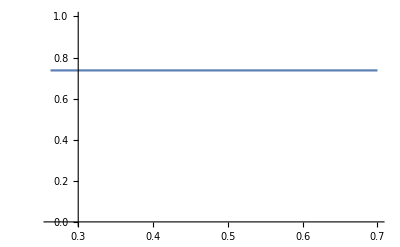

General::ivar: 0 is not a valid variable.

ReplaceAll::reps: {FindFit[{{3/256, InverseCDF[HistogramDistribution[$Failed, 256], 3/256]}, {1/64, InverseCDF[HistogramDistribution[$Failed, 256], 1/64]}, {5/256, InverseCDF[HistogramDistribution[$Failed, 256], 5/256]}, {3/128, InverseCDF[HistogramDistribution[$Failed, 256], 3/128]}, {7/256, InverseCDF[HistogramDistribution[$Failed, 256], 7/256]}, {1/32, InverseCDF[HistogramDistribution[$Failed, 256], 1/32]}, {9/256, InverseCDF[HistogramDistribution[$Failed, 256], 9/256]}, « 37 », {47/256, InverseCDF[HistogramDistribution[$Failed, 256], 47/256]}, {3/16, InverseCDF[HistogramDistribution[$Failed, 256], 3/16]}, {49/256, InverseCDF[HistogramDistribution[$Failed, 256], 49/256]}, {25/128, InverseCDF[HistogramDistribution[$Failed, 256], 25/128]}, {51/256, InverseCDF[HistogramDistribution[$Failed, 256], 51/256]}, {13/64, InverseCDF[HistogramDistribution[$Failed, 256], 13/64]}, « 14 »}, 0.4  + ⅇ^c, « 1 », {0}, Method → "Automatic"]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0 is not a valid variable.

ReplaceAll::reps: {FindFit[{{3/256, InverseCDF[HistogramDistribution[$Failed, 256], 3/256]}, {1/64, InverseCDF[HistogramDistribution[$Failed, 256], 1/64]}, {5/256, InverseCDF[HistogramDistribution[$Failed, 256], 5/256]}, {3/128, InverseCDF[HistogramDistribution[$Failed, 256], 3/128]}, {7/256, InverseCDF[HistogramDistribution[$Failed, 256], 7/256]}, {1/32, InverseCDF[HistogramDistribution[$Failed, 256], 1/32]}, {9/256, InverseCDF[HistogramDistribution[$Failed, 256], 9/256]}, « 37 », {47/256, InverseCDF[HistogramDistribution[$Failed, 256], 47/256]}, {3/16, InverseCDF[HistogramDistribution[$Failed, 256], 3/16]}, {49/256, InverseCDF[HistogramDistribution[$Failed, 256], 49/256]}, {25/128, InverseCDF[HistogramDistribution[$Failed, 256], 25/128]}, {51/256, InverseCDF[HistogramDistribution[$Failed, 256], 51/256]}, {13/64, InverseCDF[HistogramDistribution[$Failed, 256], 13/64]}, « 14 »}, 0.4  + ⅇ^c, « 1 », {0}, Method → "Automatic"]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 5.50614×10^-6 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[{{3/256, InverseCDF[HistogramDistribution[$Failed, 256], 3/256]}, {1/64, InverseCDF[HistogramDistribution[$Failed, 256], 1/64]}, {5/256, InverseCDF[HistogramDistribution[$Failed, 256], 5/256]}, {3/128, InverseCDF[HistogramDistribution[$Failed, 256], 3/128]}, {7/256, InverseCDF[HistogramDistribution[$Failed, 256], 7/256]}, {1/32, InverseCDF[HistogramDistribution[$Failed, 256], 1/32]}, {9/256, InverseCDF[HistogramDistribution[$Failed, 256], 9/256]}, « 37 », {47/256, InverseCDF[HistogramDistribution[$Failed, 256], 47/256]}, {3/16, InverseCDF[HistogramDistribution[$Failed, 256], 3/16]}, {49/256, InverseCDF[HistogramDistribution[$Failed, 256], 49/256]}, {25/128, InverseCDF[HistogramDistribution[$Failed, 256], 25/128]}, {51/256, InverseCDF[HistogramDistribution[$Failed, 256], 51/256]}, {13/64, InverseCDF[HistogramDistribution[$Failed, 256], 13/64]}, « 14 »}, « 3 », Method → "Automatic"]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics-

```mathematica
69.0/256;
finalModel=Piecewise[{{modelBalls[x], x<0.263}, {modelTip[x], x>0.7}, {0.7373731292608454, x≥ 0.26}}]

Plot[finalModel,{x,0,1},PlotRange->{0,1}]
Plot[modelBalls[x],{x,0,0.26953125}]
```

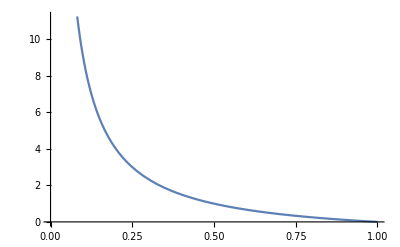

3.

```mathematica
Plot[(1-x)/x,{x,0,1}]
Limit[(1-x)/x,x-> 0.25]
```